## First the code

```mathematica
SymbolHighlight[s_,e_]:=Block[{conv,elim={e[[1]],e[[2]]}},
conv=SymbolToSets[s];
conv=Map[Select[#,!MemberQ[elim,#]&]&,conv];
conv=Select[conv,#≠{}&];
conv=Sort[Map[Sort,conv]];
SetsToSymbol[conv]
]
```

```mathematica
MixSymbols[set1_,set2_]:=Block[{result=Sort[DeleteDuplicates[Join[set1,set2]],CompareSymbols]},
Map[
Style[#,
If[MemberQ[set1,#],
If[MemberQ[set2,#],
Darker[Green]
,
Darker[Red]
]
,
Orange
]
]&
,
result]
]
```

```mathematica
InspectAllEdges[g_]:=Block[{min=Null},
min=Monitor[   Table[
With[{del=FindFullFormula1234[EdgeContract[g,e]],
del2=FindFullFormula1234[EdgeDelete[g,e]]},
e<->
With[{left=Map[SymbolHighlight[#,e]&,Select[del2,SymbolLevel[#]≤5&]],
right=Map[SymbolHighlight[#,e]&,Select[del,SymbolLevel[#]<=5&]]},
Multicolumn[MixSymbols[left,right],4]
]
],{e,EdgeList[g]}],e       ];
min
]
```

```mathematica
EdgeList[plantri8]//Length
```

45

```mathematica
Column[InspectAllEdges[plantri8]]
```

12<->13<->v1ax247bx359hx68efg | v14ax258fx39bhx67eg | v19x247bx35ahx68efg | v29bx146ax357hx8efg
v13ax259fx467bx8egh | v14ax259fx37bhx68eg | v24ax137gx568fx9beh | v29bx1467x35ahx8efg
v13ax259fx47bhx68eg | v14ax259fx37ghx68be | v24ax137gx569fx8beh | v3fgx1467x258ax9beh
v13ax259x47bhx68efg | v14ax259x37bhx68efg | v24ax167gx359fx8beh | v35ax1467x28fgx9beh
v13ax59hx247bx68efg | v14ax27bx359hx68efg | v24ax168gx359fx7beh | v4bhx137gx258ax69ef
v13gx259fx467bx8aeh | v14ax28fgx357hx69be | v24bx137gx569fx8aeh | v46fx137gx258ax9beh
v13gx259fx47bhx68ae | v14ax28fgx359hx67be | v24bx137gx58ahx69ef | v8bex146ax259fx37gh
v139x25ax47bhx68efg | v14ax29bx357hx68efg | v24bx167gx359fx8aeh | v8egx146ax259fx37bh
v139x5ahx247bx68efg | vefgx1467x258ax39bh | v24bx168ax359fx7egh | v9bex146ax258fx37gh
v14ax257x39bhx68efg | v147x25ax39bhx68efg | v25ax1467x39bhx8efg | v9bex146ax28fgx357h
v14ax258fx37ghx69be | v147x29bx35ahx68efg | v259x146ax37bhx8efg | v9bex1467x28fgx35ah
12<->7<->v1adx24bx359hx68efg | v13gx258ax4bdhx69ef | v14ax3bhx68egx259df | v24bx168gx359fxadeh
v13ax24bx59dhx68efg | v13gx258fx4adhx69be | v14ax3ghx68bex259df | v25x14adx39bhx68efg
v13ax4bhx259dx68efg | v13gx259fx4adhx68be | v14ax35hx29bdx68efg | v259x3bhx14adx68efg
v13ax4bhx68egx259df | v13gx259fx4bdhx68ae | v14x25adx39bhx68efg | v29bx35hx14adx68efg
v13ax46bx8eghx259df | v13gx4ahx68bex259df | v14x29bdx35ahx68efg | v3bhx8egx146ax259df
v13gx24adx568fx9beh | v13gx4bhx68aex259df | v146x258ax39bhxdefg | v3bx146ax8eghx259df
v13gx24adx569fx8beh | v13gx46ax258fx9bdeh | v146x3fgx258ax9bdeh | v3ghx8bex146ax259df
v13gx24ax568fx9bdeh | v13gx46ax8behx259df | v146x35ax28fgx9bdeh | v3gx146ax258fx9bdeh
v13gx24bdx569fx8aeh | v13gx46bx8aehx259df | v19dx24bx35ahx68efg | v3gx146ax8behx259df
v13gx24bdx58ahx69ef | v13gx46fx258ax9bdeh | v2bx14adx359hx68efg | v35x146ax28fgx9bdeh
v13gx24dfx568ax9beh | v139x24bx5adhx68efg | v24bx168ax359fxdegh | 
v13gx24dfx58ahx69be | v139x4bhx25adx68efg | v24bx168ax359hxdefg | 
v13gx24fx568ax9bdeh | v14ax3bhx259dx68efg | v24bx168gx35ahx9def | 
12<->15<->v13ax247bx59dhx68eg | v24ax568x137gx9bdeh | v259x14adx37ghx68be | v359x168ax24bdx7egh
v13ax259dx467bx8egh | v24x137gx568ax9bdeh | v28gx14adx357hx69be | v359x168ax247bxdegh
v13ax259dx47bhx68eg | v258x137gx4adhx69be | v28gx14adx359hx67be | v359x168gx24adx7beh
vdegx1467x258ax39bh | v258x14adx37ghx69be | v28gx146ax357hx9bde | v359x168gx247bxadeh
v13gx259dx467bx8aeh | v258x14adx39bhx67eg | v28gx1467x35ahx9bde | v46x137gx258ax9bdeh
v13gx259dx47bhx68ae | v258x146ax37ghx9bde | v28gx35ax1467x9bdeh | v69ex137gx258ax4bdh
v139x247bx5adhx68eg | v258x37gx146ax9bdeh | v28gx357x146ax9bdeh | v8bex146ax259dx37gh
v139x25adx47bhx68eg | v258x46ax137gx9bdeh | v29bx14adx357hx68eg | v8egx146ax259dx37bh
v14ax259dx37bhx68eg | v259x137gx4adhx68be | v3gx1467x258ax9bdeh | v8egx146ax29bdx357h
v14ax259dx37ghx68be | v259x137gx4bdhx68ae | v359x167gx24adx8beh | v8egx1467x25adx39bh
v14ax29bdx357hx68eg | v259x14adx37bhx68eg | v359x167gx24bdx8aeh | v8egx1467x29bdx35ah
12<->17<->v1adx359x247bx68efg | v14ax37gx68bex259df | v35ax168gx247bx9def | v46bx8aex137gx259df
v13ax47bx259dx68efg | v147x35ax29bdx68efg | v359x14adx28fgx67be | v46fx137gx258ax9bde
v13ax47bx68egx259df | v147x39bx25adx68efg | v359x168ax247bxdefg | v58ax137gx24bdx69ef
v13ax59dx247bx68efg | v19dx35ax247bx68efg | v37bx8egx146ax259df | v58ax137gx24dfx69be
v13ax8egx467bx259df | v24ax137gx568fx9bde | v37gx8bex146ax259df | v8aex137gx24bdx569f
v13gx47bx68aex259df | v257x39bx14adx68efg | v39bx14adx258fx67eg | v8aex167gx24bdx359f
v13gx8aex467bx259df | v259x37bx14adx68efg | v39bx1467x25adx8efg | v8bex137gx24adx569f
v139x47bx25adx68efg | v27bx359x14adx68efg | v39bx1467x258axdefg | v8bex167gx24adx359f
v139x5adx247bx68efg | v29bx357x14adx68efg | v4ax137gx68bex259df | v9bex137gx24adx568f
v14ax357x29bdx68efg | v3fgx1467x258ax9bde | v4bdx137gx258ax69ef | v9bex137gx24dfx568a
v14ax37bx259dx68efg | v35ax1467x28fgx9bde | v4bx137gx68aex259df | 
v14ax37bx68egx259df | v35ax1467x29bdx8efg | v46ax8bex137gx259df | 
12<->6<->v13ax247bx59dhx8efg | v14ax357x28fgx9bdeh | v18gx24adx359fx7beh | v4fx137gx258ax9bdeh
v13ax259dx47bhx8efg | v14ax37bx8eghx259df | v18gx247bx35ahx9def | v58ax137gx24dfx9beh
v13ax47bx8eghx259df | v14ax37gx258fx9bdeh | v18gx247bx359fxadeh | v8aex137gx259fx4bdh
v13ax8egx47bhx259df | v14ax37gx8behx259df | v24ax58fx137gx9bdeh | v8bex137gx259fx4adh
v13gx47bx8aehx259df | v14ax8bex37ghx259df | v24fx58ax137gx9bdeh | v8bex14adx259fx37gh
v13gx8aex47bhx259df | v14ax8egx37bhx259df | v259x14adx37bhx8efg | v8egx14adx259fx37bh
v139x247bx5adhx8efg | v147x258ax39bhxdefg | v29bx14adx357hx8efg | v9bex137gx24dfx58ah
v139x25adx47bhx8efg | v147x3fgx258ax9bdeh | v4ahx8bex137gx259df | v9bex137gx258fx4adh
v14ax258fx37ghx9bde | v147x35ax28fgx9bdeh | v4ax137gx258fx9bdeh | v9bex14adx258fx37gh
v14ax259dx37bhx8efg | v18ax24bdx359fx7egh | v4ax137gx8behx259df | v9bex14adx28fgx357h
v14ax28fgx357hx9bde | v18ax247bx359fxdegh | v4bhx8aex137gx259df | v9efx137gx258ax4bdh
v14ax29bdx357hx8efg | v18ax247bx359hxdefg | v4bx137gx8aehx259df | 
13<->6<->v13gx9efx47bhx258ac | v14ax29bcx357hx8efg | v4bhx9efx137gx258ac | v8aex13cgx259fx47bh
v139xefgx47bhx258ac | vefgx139cx247bx58ah | v4fx137gx9behx258ac | v8bex14acx259fx37gh
v14ax258fx37ghx9bce | vefgx139cx258ax47bh | v47bx13acx259fx8egh | v8egx13acx259fx47bh
v14ax258fx39bcx7egh | vefgx18acx247bx359h | v47bx13cgx259fx8aeh | v8egx14acx259fx37bh
v14ax259cx37bhx8efg | v147xefgx39bhx258ac | v5ahx139cx247bx8efg | v9bex14acx258fx37gh
v14ax259fx37bhx8ceg | v147x28fgx35acx9beh | v58fx137gx24acx9beh | v9bex14acx28fgx357h
v14ax259fx37ghx8bce | v147x3fgx9behx258ac | v59fx13acx247bx8egh | v9efx13cgx247bx58ah
v14ax28bcx359fx7egh | v25ax139cx47bhx8efg | v59fx13cgx247bx8aeh | v9efx13cgx258ax47bh
v14ax28cgx359fx7beh | v259x13acx47bhx8efg | v59fx137gx24acx8beh | v9efx137gx24bcx58ah
v14ax28fgx357hx9bce | v259x14acx37bhx8efg | v59fx137gx24bcx8aeh | v9efx18cgx247bx35ah
v14ax28fgx359cx7beh | v29bx14acx357hx8efg | v59hx13acx247bx8efg | 
13<->3<->v1acx259fx467bx8egh | v147x9bhx25acx68efg | v259x7bhx14acx68efg | v59fx168ax24bcx7egh
v1acx259fx47bhx68eg | v147x9bhx6efgx258ac | v27bx59hx14acx68efg | v59fx168gx24acx7beh
v1acx259x47bhx68efg | vfgx1467x9behx258ac | v29bx57hx14acx68efg | v59hx14acx28fgx67be
v1acx59hx247bx68efg | v17gx24acx568fx9beh | v5acx1467x28fgx9beh | v59hx18acx247bx6efg
v1ax259cx47bhx68efg | v17gx4bhx69efx258ac | v5ahx1467x28fgx9bce | v7bhx14acx259fx68eg
v1cgx259fx467bx8aeh | v17gx46fx9behx258ac | v5ahx1467x29bcx8efg | v7bhx146ax259fx8ceg
v1cgx259fx47bhx68ae | v19cx25ax47bhx68efg | v5ahx18cgx247bx69ef | v7ghx14acx259fx68be
v1gx47bhx69efx258ac | v19cx5ahx247bx68efg | v59fx146ax28bcx7egh | v7ghx146ax259fx8bce
v14ax57hx29bcx68efg | v19x25acx47bhx68efg | v59fx146ax28cgx7beh | v9bhx14acx258fx67eg
v14ax7bhx259cx68efg | v19x47bhx6efgx258ac | v59fx167gx24acx8beh | v9bhxefgx1467x258ac
v147x5ahx29bcx68efg | v257x9bhx14acx68efg | v59fx167gx24bcx8aeh | v9bhx1467x25acx8efg
13<->8<->vaehx13cgx247bx569f | vefgx146ax29bcx357h | v25ax13cgx47bhx69ef | v46fx137gx25acx9beh
vaehx13cgx259fx467b | vefgx1467x25acx39bh | v25ax139cx47bhx6efg | v5ahx13cgx247bx69ef
vaehx137gx24bcx569f | vefgx1467x29bcx35ah | v25fx14acx37ghx69be | v5ahx137gx24bcx69ef
vaehx167gx24bcx359f | veghx13acx247bx569f | v25fx14acx39bhx67eg | v5ahx139cx247bx6efg
vbcex146ax259fx37gh | veghx13acx259fx467b | v25fx146ax37ghx9bce | v56fx137gx24acx9beh
vbehx137gx24acx569f | v2fgx14acx357hx69be | v25fx146ax39bcx7egh | v59hx13acx247bx6efg
vbehx167gx24acx359f | v2fgx14acx359hx67be | v259x13acx47bhx6efg | v6aex13cgx259fx47bh
vcegx146ax259fx37bh | v2fgx146ax357hx9bce | v259x14acx37bhx6efg | v6bex14acx259fx37gh
v14ax259cx37bhx6efg | v2fgx146ax359cx7beh | v29bx14acx357hx6efg | v6egx13acx259fx47bh
v14ax29bcx357hx6efg | v2fgx1467x35acx9beh | v3fgx1467x25acx9beh | v6egx14acx259fx37bh
vefgx146ax259cx37bh | v2fgx1467x35ahx9bce | v4bhx137gx25acx69ef | 
13<->7<->v1acx24bx359hx68efg | veghx146ax258fx39bc | v24bx13cgx569fx8aeh | v3bhx14acx259fx68eg
vbehx146ax28cgx359f | veghx146ax28bcx359f | v24bx13cgx58ahx69ef | v3bhx146ax259fx8ceg
vbehx146ax28fgx359c | veghx168ax24bcx359f | v24bx139cx58ahx6efg | v3ghx14acx259fx68be
vbehx168gx24acx359f | v14x25acx39bhx68efg | v24bx18acx359hx6efg | v3ghx146ax259fx8bce
v13ax4bhx259cx68efg | v14x29bcx35ahx68efg | v24bx18cgx35ahx69ef | v4bhx13acx259fx68eg
v13gx24acx568fx9beh | v14x39bhx6efgx258ac | v24bx5ahx139cx68efg | v4bhx13cgx258ax69ef
v13gx4bhx69efx258ac | v146xefgx39bhx258ac | v24bx59hx13acx68efg | v4bhx13cgx259fx68ae
v13gx46fx9behx258ac | v146x28fgx35acx9beh | v25ax4bhx139cx68efg | v4bhx139cx258ax6efg
v139x4bhx25acx68efg | v146x3fgx9behx258ac | v25x14acx39bhx68efg | v46bx13acx259fx8egh
v139x4bhx6efgx258ac | v19cx24bx35ahx68efg | v259x3bhx14acx68efg | v46bx13cgx259fx8aeh
v14ax3bhx259cx68efg | v2bx14acx359hx68efg | v259x4bhx13acx68efg | 
v14ax35hx29bcx68efg | v24bx13acx569fx8egh | v29bx35hx14acx68efg | 
7<->8<->vbehx13cgx24adx569f | v16gx24bcx35ahx9def | v3bhx14adx259cx6efg | v4bhx6egx13acx259df
vbehx146ax2dfgx359c | v16gx24bcx359fxadeh | v3bhx6egx14acx259df | v46axbehx13cgx259df
v13gx25acx4bdhx69ef | v16gx24dfx35acx9beh | v3cgxbehx146ax259df | v46bxaehx13cgx259df
v13gx46fx25acx9bdeh | v16gx24dfx35ahx9bce | v3ghxbcex146ax259df | v46bxeghx13acx259df
v13gx56fx24acx9bdeh | v16gx24fx35acx9bdeh | v3ghx6bex14acx259df | v6bex13cgx259fx4adh
veghx13acx24bdx569f | v16gx35fx24acx9bdeh | v35hx14acx29bdx6efg | v6bex14acx2dfgx359h
veghx146ax25dfx39bc | v24bx13acx59dhx6efg | v35hx14adx29bcx6efg | v6egx13acx259fx4bdh
v146x2fgx35acx9bdeh | v24bx139cx5adhx6efg | v4ahx6bex13cgx259df | v6egx14acx25dfx39bh
v146x25acx39bhxdefg | v3bcxeghx146ax259df | v4bhx13acx259dx6efg | 
v146x3fgx25acx9bdeh | v3bhxcegx146ax259df | v4bhx139cx25adx6efg | 
v16gx24acx359fxbdeh | v3bhx14acx259dx6efg | v4bhx6aex13cgx259df | 
7<->9<->v1acx35hx24bdx68efg | v13x4bdhx6efgx258ac | v25dx4bhx13acx68efg | v35hx168ax24bcxdefg
v1adx35hx24bcx68efg | v14cx3bhx25adx68efg | v25x13acx4bdhx68efg | v35hx18acx24bdx6efg
vbehx13cgx24adx568f | v14dx3bhx25acx68efg | v3bhx14acx25dfx68eg | v4bhx13acx25dfx68eg
vbehx13cgx24dfx568a | v14dx3bhx6efgx258ac | v3bhx14adx258cx6efg | v4bhx13cgx25dfx68ae
vbehx168gx24dfx35ac | v146x28fgx35acxbdeh | v3bhx146ax25dfx8ceg | v46bx13acx25dfx8egh
v13cx24bx5adhx68efg | v146x3bhxdefgx258ac | v3bhx146ax258cxdefg | v46bx13cgx25dfx8aeh
v13cx4bhx25adx68efg | v146x3fgxbdehx258ac | v3ghx14acx25dfx68be | v5hx13acx24bdx68efg
v13gx24acx568fxbdeh | v2bcx35hx14adx68efg | v3ghx146ax25dfx8bce | v6bex13cgx24dfx58ah
v13gx46fxbdehx258ac | v2bdx35hx14acx68efg | v35hx14acx2dfgx68be | v6bex13cgx258fx4adh
v13gx6efx4bdhx258ac | v24bx5dhx13acx68efg | v35hx14adx28bcx6efg | v6bex18cgx24dfx35ah
v13x24bcx5adhx68efg | v25cx3bhx14adx68efg | v35hx146ax2dfgx8bce | 
v13x25acx4bdhx68efg | v25dx3bhx14acx68efg | v35hx146ax28bcxdefg | 
7<->10<->v13cx24bx59dhx68efg | v14dx3bhx259cx68efg | v146x3bhx8cegx259df | v35hx168gx24bcx9def
v13cx4bhx259dx68efg | v14dx35hx29bcx68efg | v146x3cgx258fx9bdeh | v35hx168gx24dfx9bce
v13cx4bhx68egx259df | v146x2dfgx359cx8beh | v146x3cgx8behx259df | v35hx18cgx24bdx69ef
v13cx46bx8eghx259df | v146x2dfgx359hx8bce | v146x3fgx258cx9bdeh | v35hx18cgx24dfx69be
v13gx24cx568fx9bdeh | v146x25dfx39bcx8egh | v146x3ghx8bcex259df | v4bhx68ex13cgx259df
v13gx258cx4bdhx69ef | v146x25dfx39bhx8ceg | v146x35cx28fgx9bdeh | v4hx13cgx68bex259df
v13gx46fx258cx9bdeh | v146x258cx39bhxdefg | v146x35fx28cgx9bdeh | v46bx8ehx13cgx259df
v13x24bcx59dhx68efg | v146x258fx39bcxdegh | v19cx35hx24bdx68efg | v46x13cgx258fx9bdeh
v13x259cx4bdhx68efg | v146x28bcx359fxdegh | v19dx35hx24bcx68efg | v46x13cgx8behx259df
v14cx3bhx259dx68efg | v146x28bcx359hxdefg | v24bx5dhx139cx68efg | v5hx139cx24bdx68efg
v14cx3bhx68egx259df | v146x28cgx359fxbdeh | v24x13cgx568fx9bdeh | 
v14cx3ghx68bex259df | v146x28fgx359cxbdeh | v25dx4bhx139cx68efg | 
v14cx35hx29bdx68efg | v146x3bcx8eghx259df | v25x139cx4bdhx68efg | 
7<->15<->v13gx568x24acx9bdeh | v24x168gx35acx9bdeh | v35hx14adx29bcx68eg | v46x13gx258acx9bdeh
v13gx69ex4bdhx258ac | v3bhx14acx259dx68eg | v35x146ax28cgx9bdeh | v6egx139cx24bdx58ah
v139x6egx4bdhx258ac | v3bhx14adx259cx68eg | v35x168gx24acx9bdeh | v6egx139cx258ax4bdh
v14dx6egx39bhx258ac | v3bhx146ax259dx8ceg | v4bhx13acx259dx68eg | v6egx14adx258cx39bh
v146xdegx39bhx258ac | v3ghx14acx259dx68be | v4bhx13cgx259dx68ae | v6egx14adx28bcx359h
v146x28gx35acx9bdeh | v3ghx146ax259dx8bce | v4bhx139cx25adx68eg | v6egx18acx24bdx359h
v24bx13acx59dhx68eg | v3gx146ax258cx9bdeh | v46bx13acx259dx8egh | 
v24bx139cx5adhx68eg | v3gx146x258acx9bdeh | v46bx13cgx259dx8aeh | 
v24x13cgx568ax9bdeh | v35hx14acx29bdx68eg | v46x13cgx258ax9bdeh | 
15<->10<->v13cx247bx59dhx68eg | v24cx568x137gx9bdeh | v25dx1467x39bhx8ceg | v5dhx139cx247bx68eg
v13cx259dx467bx8egh | v24dx167gx359cx8beh | v258x13cgx467bx9deh | v568x13cgx247bx9deh
v13cx259dx47bhx68eg | v24dx167gx359hx8bce | v258x139cx4bdhx67eg | v568x137gx24bcx9deh
vdegx1467x258cx39bh | v24dx168gx357hx9bce | v258x139cx467bxdegh | v568x139cx24bdx7egh
v14cx259dx37bhx68eg | v24dx168gx359cx7beh | v258x1467x39bcxdegh | v568x139cx247bxdegh
v14cx259dx37ghx68be | v24dx18cgx357hx69be | v258x3cgx1467x9bdeh | v68ex13cgx247bx59dh
v14cx29bdx357hx68eg | v24dx18cgx359hx67be | v258x467x13cgx9bdeh | v68ex13cgx259dx47bh
v14dx259cx37bhx68eg | v247x568x13cgx9bdeh | v28gx35cx1467x9bdeh | v68ex137gx24bcx59dh
v14dx29bcx357hx68eg | v25dx139cx467bx8egh | v3gx1467x258cx9bdeh | v68ex137gx259cx4bdh
v146x259dx37bhx8ceg | v25dx139cx47bhx68eg | v35x1467x28cgx9bdeh | v69ex137gx258cx4bdh
v146x259dx37ghx8bce | v25dx1467x39bcx8egh | v46x137gx258cx9bdeh | v8ehx13cgx259dx467b
15<->11<->v14dx69ex37ghx258ac | v29cx14adx357hx68eg | v39x1467xdeghx258ac | v68ex14acx259dx37gh
v146x9dex37ghx258ac | v29dx14acx357hx68eg | v4dhx69ex137gx258ac | v68ex14adx259cx37gh
v24dx139cx568ax7egh | v29dx146ax357hx8ceg | v46x137gx9dehx258ac | v69ex137gx258cx4adh
v24dx139cx58ahx67eg | v29dx1467x35acx8egh | v467x13acx259dx8egh | v69ex14adx258cx37gh
v24dx167gx359cx8aeh | v29dx1467x35ahx8ceg | v467x13cgx259dx8aeh | v69ex14adx28cgx357h
v24dx167gx359hx8ace | v3ghx9dex1467x258ac | v47hx13acx259dx68eg | v69ex18cgx24adx357h
v24dx168ax359cx7egh | v3gx1467x9dehx258ac | v47hx13cgx259dx68ae | v8cex146ax259dx37gh
v24dx18acx359hx67eg | v37hx14acx259dx68eg | v47hx139cx25adx68eg | v9dex146ax258cx37gh
v247x13acx59dhx68eg | v37hx14adx259cx68eg | v568x137gx24acx9deh | v9dex146ax28cgx357h
v247x139cx5adhx68eg | v37hx146ax259dx8ceg | v68ex137gx24acx59dh | v9dex1467x28cgx35ah
v28gx1467x35acx9deh | v39hxdegx1467x258ac | v68ex137gx259cx4adh | v9dex168gx24acx357h
15<->1<->v247x68gx35acx9bdeh | v357x68gx24acx9bdeh | v4acx29bdx357hx68eg | v467xdegx39bhx258ac
v28gx467x35acx9bdeh | v37gx568x24acx9bdeh | v4adx259cx37bhx68eg | v68gx24acx357hx9bde
v3acx247bx59dhx68eg | v37gx69ex4bdhx258ac | v4adx29bcx357hx68eg | v68gx24adx357hx9bce
v3acx259dx467bx8egh | v39cx247bx5adhx68eg | v4dx37ghx69bex258ac | v68gx24adx359cx7beh
v3acx259dx47bhx68eg | v39cx25adx47bhx68eg | v4dx39bhx67egx258ac | v68gx247bx35acx9deh
v3cgx259dx467bx8aeh | v39x4bdhx67egx258ac | v46ax259dx37bhx8ceg | v68gx247bx359cxadeh
v3cgx259dx47bhx68ae | v39x467bxdeghx258ac | v46ax259dx37ghx8bce | 
v3gx467bx9dehx258ac | v4acx259dx37bhx68eg | v46x37ghx9bdex258ac | 
v3gx467x258acx9bdeh | v4acx259dx37ghx68be | v46x37gx258acx9bdeh | 
15<->17<->vdegx139cx247bx568a | v359x14adx28cgx67be | v4bdx69ex137gx258ac | v59dx137gx24acx68be
vdegx139cx258ax467b | v359x167gx24adx8bce | v4dx137gx69bex258ac | v59dx137gx24bcx68ae
vdegx1467x258ax39bc | v359x167gx24bdx8ace | v46bx9dex137gx258ac | v8aex13cgx259dx467b
vdegx168ax247bx359c | v359x18acx24bdx67eg | v46x137gx9bdex258ac | v8egx13acx259dx467b
v13gx9dex467bx258ac | v359x18cgx24adx67be | v47bx13acx259dx68eg | v8egx139cx25adx467b
v139xdegx467bx258ac | v37bx14acx259dx68eg | v47bx13cgx259dx68ae | v8egx1467x25adx39bc
v28gx1467x35acx9bde | v37bx14adx259cx68eg | v47bx139cx25adx68eg | v8egx1467x29bdx35ac
v3gx1467x9bdex258ac | v37bx146ax259dx8ceg | v5adx139cx247bx68eg | v9dex13cgx247bx568a
v357x14acx29bdx68eg | v37gx14acx259dx68be | v568x137gx24acx9bde | v9dex13cgx258ax467b
v357x14adx29bcx68eg | v37gx146ax259dx8bce | v59dx13acx247bx68eg | v9dex137gx24bcx568a
v359x14adx28bcx67eg | v39bxdegx1467x258ac | v59dx13cgx247bx68ae | v9dex168gx247bx35ac
17<->1<->vadx247bx359cx68efg | v357x4acx29bdx68efg | v37gx24bdx58acx69ef | v39cx5adx247bx68efg
v257x4adx39bcx68efg | v357x4adx29bcx68efg | v37gx24dfx568ax9bce | v39x467bxdefgx258ac
v27bx4adx359cx68efg | v37bx4acx259dx68efg | v37gx24dfx58acx69be | v4adx258fx39bcx67eg
v3acx47bx259dx68efg | v37bx4acx68egx259df | v37gx4acx68bex259df | v4adx28bcx359fx67eg
v3acx47bx68egx259df | v37bx4adx259cx68efg | v37gx4bcx68aex259df | v4adx28cgx359fx67be
v3acx59dx247bx68efg | v37bx46ax8cegx259df | v37gx4bdx69efx258ac | v4adx28fgx359cx67be
v3acx8egx467bx259df | v37gx24acx568fx9bde | v37gx4dfx69bex258ac | v467x28fgx35acx9bde
v3ax467bx8cegx259df | v37gx24acx59dfx68be | v37gx46ax8bcex259df | v47x25adx39bcx68efg
v3cgx47bx68aex259df | v37gx24adx568fx9bce | v37gx46bx8acex259df | v47x29bdx35acx68efg
v3cgx8aex467bx259df | v37gx24adx569fx8bce | v37gx46bx9defx258ac | v9dx247bx35acx68efg
v3fgx467x9bdex258ac | v37gx24bcx568ax9def | v37gx46fx9bdex258ac | 
v3gx467bx8acex259df | v37gx24bcx59dfx68ae | v39bx467xdefgx258ac | 
v3gx467bx9defx258ac | v37gx24bdx569fx8ace | v39cx47bx25adx68efg | 
17<->2<->v1adx47bx359cx68efg | v37gx14acx59dfx68be | v4bdx18acx359fx67eg | v5adx1467x39bcx8efg
v147x5adx39bcx68efg | v37gx146ax59dfx8bce | v46fx137gx58acx9bde | v57x14adx39bcx68efg
v147x9bdx35acx68efg | v39bx1467x58acxdefg | v47bx13acx59dfx68eg | v58ax13cgx467bx9def
v19dx47bx35acx68efg | v4acx137gx568fx9bde | v47bx13cgx568ax9def | v58ax139cx467bxdefg
v3fgx1467x58acx9bde | v4adx137gx568fx9bce | v47bx13cgx59dfx68ae | v58ax1467x39bcxdefg
v357x9bcx14adx68efg | v4adx137gx569fx8bce | v47bx139cx568axdefg | v59dx13acx467bx8efg
v357x9bdx14acx68efg | v4adx167gx359fx8bce | v47bx168ax359cxdefg | v7bx14adx359cx68efg
v37bx14acx59dfx68eg | v4adx18cgx359fx67be | v47bx168gx35acx9def | v8aex13cgx467bx59df
v37bx146ax59dfx8ceg | v4bdx137gx569fx8ace | v47bx5adx139cx68efg | v8egx13acx467bx59df
v37bx59cx14adx68efg | v4bdx137gx58acx69ef | v47bx59dx13acx68efg | v8fgx1467x35acx9bde
v37bx59dx14acx68efg | v4bdx167gx359fx8ace | v5adx139cx467bx8efg | v9bdx1467x35acx8efg
17<->6<->v13ax47bx8cegx259df | v37bx14adx259cx8efg | v47bx13cgx258ax9def | v7bex14adx28cgx359f
v13gx47bx8acex259df | v37bx8egx14acx259df | v47bx139cx25adx8efg | v7bex14adx28fgx359c
v13gx47bx9defx258ac | v37gx8bex14acx259df | v47bx139cx258axdefg | v7bex18cgx24adx359f
v139x47bxdefgx258ac | v4acx8bex137gx259df | v47bx8aex13cgx259df | v7egx14adx258fx39bc
v14ax37bx8cegx259df | v4ax137gx8bcex259df | v47bx8egx13acx259df | v7egx14adx28bcx359f
v14ax37gx8bcex259df | v4bcx8aex137gx259df | v5adx139cx247bx8efg | v7egx18acx24bdx359f
v147x28fgx35acx9bde | v4bdx9efx137gx258ac | v58ax13cgx247bx9def | v8aex13cgx247bx59df
v147x3fgx9bdex258ac | v4bx137gx8acex259df | v58ax137gx24bcx9def | v8aex137gx24bcx59df
v147x39bxdefgx258ac | v4bx137gx9defx258ac | v58ax137gx24dfx9bce | v8bex137gx24acx59df
v357x14acx29bdx8efg | v4dfx9bex137gx258ac | v58ax139cx247bxdefg | v8egx13acx247bx59df
v357x14adx29bcx8efg | v4fx137gx9bdex258ac | v58fx137gx24acx9bde | v9bex137gx24dfx58ac
v37bx14acx259dx8efg | v47bx13acx259dx8efg | v59dx13acx247bx8efg | 
6<->2<->v14ax37bhx59dfx8ceg | v47bx13cgx58ahx9def | v58fx137gx4adhx9bce | v8aex13cgx47bhx59df
v14ax37ghx59dfx8bce | v47bx13cgx59dfx8aeh | v58fx14acx37ghx9bde | v8bex14acx37ghx59df
v147x3fgx58acx9bdeh | v47bx139cx5adhx8efg | v58fx14adx37ghx9bce | v8egx13acx47bhx59df
v147x39bhx58acxdefg | v47bx139cx58ahxdefg | v58fx14adx39bcx7egh | v8egx14acx37bhx59df
v147x8fgx35acx9bdeh | v47bx18acx359fxdegh | v59cx14adx37bhx8efg | v8fgx14acx357hx9bde
v357x8fgx14acx9bdeh | v47bx18acx359hxdefg | v59dx13acx47bhx8efg | v8fgx14adx357hx9bce
v37gx58fx14acx9bdeh | v47bx18cgx35ahx9def | v59dx14acx37bhx8efg | v8fgx14adx359cx7beh
v4acx58fx137gx9bdeh | v47bx18cgx359fxadeh | v59fx137gx4adhx8bce | v9bcx14adx357hx8efg
v4fx137gx58acx9bdeh | v5adx139cx47bhx8efg | v59fx137gx4bdhx8ace | v9bdx14acx357hx8efg
v47bx13acx59dfx8egh | v58ax13cgx47bhx9def | v59fx14adx37bhx8ceg | v9efx137gx4bdhx58ac
v47bx13acx59dhx8efg | v58ax139cx47bhxdefg | v59fx14adx37ghx8bce | 
6<->3<->v1acx247bx59dhx8efg | vfgx147x258acx9bdeh | v17gx4bcx8aehx259df | v59fx14adx28bcx7egh
v1acx259dx47bhx8efg | v17gx24acx59dfx8beh | v17gx4bhx8acex259df | v59fx14adx28cgx7beh
v1acx47bx8eghx259df | v17gx24bcx58ahx9def | v17gx4bhx9defx258ac | v59fx18acx24bdx7egh
v1acx8egx47bhx259df | v17gx24bcx59dfx8aeh | v17gx4dfx9behx258ac | v59fx18acx247bxdegh
v1ax47bhx8cegx259df | v17gx24dfx58acx9beh | v17gx58fx24acx9bdeh | v59fx18cgx24adx7beh
v1cgx47bx8aehx259df | v17gx24dfx58ahx9bce | v17gx9efx4bdhx258ac | v59fx18cgx247bxadeh
v1cgx8aex47bhx259df | v17gx24fx58acx9bdeh | v19cx247bx5adhx8efg | v7bhx14acx259dx8efg
v1gx47bhx8acex259df | v17gx258fx4adhx9bce | v19cx25adx47bhx8efg | v7bhx14adx259cx8efg
v1gx47bhx9defx258ac | v17gx259fx4adhx8bce | v19x47bhxdefgx258ac | v7bhx8egx14acx259df
v14ax7bhx8cegx259df | v17gx259fx4bdhx8ace | v4fx17gx258acx9bdeh | v7bx14acx8eghx259df
v14ax7ghx8bcex259df | v17gx4acx258fx9bdeh | v57hx14acx29bdx8efg | v7ghx8bex14acx259df
v147x5acx28fgx9bdeh | v17gx4acx8behx259df | v57hx14adx29bcx8efg | v7gx14acx258fx9bdeh
v147x9bhxdefgx258ac | v17gx4ahx8bcex259df | v57x14acx28fgx9bdeh | v7gx14acx8behx259df
3<->2<->v1acx467bx59dfx8egh | v17gx4acx568fx9bdeh | v57x14acx68fgx9bdeh | v59fx18cgx467bxadeh
v1acx47bhx59dfx68eg | v17gx4bdhx58acx69ef | v57x14acx9bdhx68efg | v7bhx14acx59dfx68eg
v1acx47bx59dhx68efg | v17gx46fx58acx9bdeh | v59cx14adx68fgx7beh | v7bhx146ax59dfx8ceg
v1acx59dx47bhx68efg | v19cx47bx5adhx68efg | v59cx168ax47bhxdefg | v7bx14acx59dhx68efg
v1adx59cx47bhx68efg | v19cx5adx47bhx68efg | v59cx7bhx14adx68efg | v7ghx14acx59dfx68be
v1cgx467bx59dfx8aeh | v19dx5acx47bhx68efg | v59dx7bhx14acx68efg | v7ghx146ax59dfx8bce
v1cgx47bhx59dfx68ae | v5acx1467x8efgx9bdh | v59fx167gx4adhx8bce | v7gx14acx568fx9bdeh
v147x5acx68fgx9bdeh | v5acx168gx47bhx9def | v59fx167gx4bdhx8ace | v9bcx14adx568fx7egh
v147x5acx9bdhx68efg | v5acx8fgx1467x9bdeh | v59fx18acx4bdhx67eg | v9bcx1467x5adhx8efg
v147x9bcx5adhx68efg | v57hx9bcx14adx68efg | v59fx18acx467bxdegh | v9bcx1467x58ahxdefg
vfgx1467x58acx9bdeh | v57hx9bdx14acx68efg | v59fx18cgx4adhx67be | v9bhx1467x58acxdefg
3<->14<->vacx168gx47bhx259df | v17gx46fx9bdhx258ac | v68bx7ghx14acx259df | v7ghx146ax28bcx59df
vahx18cgx467bx259df | v17gx69fx4bdhx258ac | v68gx7bhx14acx259df | v7ghx168ax24bcx59df
v1acx247bx59dhx68fg | v19cx247bx5adhx68fg | v7bhx14acx259dx68fg | v7ghx18acx24bdx569f
v1acx259dx47bhx68fg | v19cx25adx47bhx68fg | v7bhx14adx259cx68fg | v7ghx8bcx146ax259df
v1acx68gx47bhx259df | v4acx7bhx168gx259df | v7bhx14adx28cgx569f | v9bcx1467x2dfgx58ah
v1acx8ghx467bx259df | v4bcx7ghx168ax259df | v7bhx146ax28cgx59df | v9bcx1467x28fgx5adh
v1cgx68ax47bhx259df | v4dfx9bhx167gx258ac | v7bhx168gx24acx59df | v9bcx167gx24dfx58ah
v1cgx8ahx467bx259df | v46ax7bhx18cgx259df | v7bhx18cgx24adx569f | v9bcx167gx258fx4adh
vcgx168ax47bhx259df | v46bx7ghx18acx259df | v7bhx8cgx146ax259df | v9bhxdfgx1467x258ac
vfgx1467x9bdhx258ac | v5acx1467x28fgx9bdh | v7ghx14acx29bdx568f | v9bhx1467x2dfgx58ac
vghx18acx467bx259df | v57hx14acx29bdx68fg | v7ghx14adx28bcx569f | v9bhx167gx24dfx58ac
v17gx24acx568fx9bdh | v57hx14adx29bcx68fg | v7ghx14adx29bcx568f | v9fx167gx4bdhx258ac
3<->4<->vacx167gx258fx9bdeh | v1acx67gx258fx9bdeh | v1cgx67bx8aehx259df | v17x29bcx5adhx68efg
vacx167gx8behx259df | v1acx67gx8behx259df | v1cgx7bhx68aex259df | v17x6efgx9bdhx258ac
vacx168gx7behx259df | v1acx68bx7eghx259df | v1dgx7bhx69efx258ac | v17x6fgx258acx9bdeh
vahx167gx8bcex259df | v1acx68gx7behx259df | vfgx167x258acx9bdeh | v19cx27bx5adhx68efg
vahx18cgx67bex259df | v1acx7bhx259dx68efg | vfx167gx258acx9bdeh | v19cx7bhx25adx68efg
v1acx257x68fgx9bdeh | v1acx7bhx68egx259df | v16ax7bhx8cegx259df | v19dx7bhx25acx68efg
v1acx257x9bdhx68efg | v1acx7ghx68bex259df | v16ax7ghx8bcex259df | v19dx7bhx6efgx258ac
v1acx258fx67egx9bdh | v1acx8bhx67egx259df | v16gx7bhx8acex259df | v6aex7bhx18cgx259df
v1acx259dx68fgx7beh | v1acx8ghx67bex259df | v16gx7bhx9defx258ac | v6egx7bhx18acx259df
v1acx27bx59dhx68efg | v1adx57hx29bcx68efg | v167x5acx28fgx9bdeh | v6fx17gx258acx9bdeh
v1acx27gx568fx9bdeh | v1adx7bhx259cx68efg | v167x9bhxdefgx258ac | v7bhxacex168gx259df
v1acx28fgx59dhx67be | vbcx167gx8aehx259df | v169x7bhxdefgx258ac | v7bhxcegx168ax259df
v1acx29bdx568fx7egh | vbcx168ax7eghx259df | v17gxbdhx69efx258ac | v7bhx168ax259cxdefg
v1acx567x28fgx9bdeh | vbhx167gx8acex259df | v17gx2acx568fx9bdeh | v7bhx168gx25acx9def
v1acx57hx29bdx68efg | vbhx167gx9defx258ac | v17x25acx68fgx9bdeh | v7bhx18acx259dx6efg
v1acx67bx8eghx259df | vbhx18acx67egx259df | v17x25acx9bdhx68efg | v7bhx18cgx25adx69ef
3<->8<->v1acxeghx467bx259df | v1cgxaehx467bx259df | vghx14acx67bex259df | v5ahx167gx24bcx9def
v1acx24bdx569fx7egh | v1cgx24adx569fx7beh | v17gx25acx4bdhx69ef | v5ahx167gx24dfx9bce
v1acx247bx569fxdegh | v1cgx247bx5adhx69ef | v17gx46fx25acx9bdeh | v5fx167gx24acx9bdeh
v1acx247bx59dhx6efg | v1cgx247bx569fxadeh | v17gx56fx24acx9bdeh | v57hx14acx29bdx6efg
v1acx259dx47bhx6efg | v1cgx25adx47bhx69ef | v19cx247bx5adhx6efg | v57hx14adx29bcx6efg
v1acx259fx4bdhx67eg | v1cgx259fx4adhx67be | v19cx25adx47bhx6efg | v6bex7ghx14acx259df
v1acx259fx467bxdegh | v1cgx259fx467bxadeh | v2fgx5acx1467x9bdeh | v6egx7bhx14acx259df
v1acx4bhx67egx259df | v1cgx4ahx67bex259df | v24fx5acx167gx9bdeh | v7bhxcegx146ax259df
v1acx46bx7eghx259df | v1cgx46ax7behx259df | v5acx1467x2dfgx9beh | v7bhx14acx259dx6efg
v1acx6egx47bhx259df | v1cgx6aex47bhx259df | v5acx167gx24dfx9beh | v7bhx14adx259cx6efg
vbcx146ax7eghx259df | vcgx146ax7behx259df | v5ahx1467x2dfgx9bce | v7ghxbcex146ax259df
vbhx14acx67egx259df | vfgx1467x25acx9bdeh | v5ahx1467x29bcxdefg | v9bhx1467x25acxdefg
8<->4<->vahx13cgx67bex259df | v1adx29bcx357hx6efg | v16ax3cgx7behx259df | v2fx167gx35acx9bdeh
v1acx2dfgx357hx69be | vbdhx137gx25acx69ef | v167x2fgx35acx9bdeh | v27bx13acx59dhx6efg
v1acx2dfgx359hx67be | vbhx13acx67egx259df | v167x25acx39bhxdefg | v27bx139cx5adhx6efg
v1acx25dfx37ghx69be | v16axbcex37ghx259df | v167x3fgx25acx9bdeh | v6aex7bhx13cgx259df
v1acx25dfx39bhx67eg | v16axcegx37bhx259df | v2acx137gx569fxbdeh | v6ax13cgx7behx259df
v1acx259dx37bhx6efg | v16ax2dfgx357hx9bce | v2acx167gx359fxbdeh | v6bx13acx7eghx259df
v1acx29bdx357hx6efg | v16ax2dfgx359cx7beh | v2acx35fx167gx9bdeh | v6egx7bhx13acx259df
v1acx3bhx67egx259df | v16ax25dfx37ghx9bce | v2acx56fx137gx9bdeh | v6fx137gx25acx9bdeh
v1acx3ghx67bex259df | v16ax25dfx39bcx7egh | v2bcx137gx5adhx69ef | v67bxaehx13cgx259df
v1acx6bex37ghx259df | v16ax259cx37bhxdefg | v2bcx137gx569fxadeh | v67bxeghx13acx259df
v1acx6egx37bhx259df | v16ax29bcx357hxdefg | v2bcx167gx35ahx9def | v7bhx13acx259dx6efg
v1adx259cx37bhx6efg | v16ax3bcx7eghx259df | v2bcx167gx359fxadeh | v7bhx139cx25adx6efg
8<->9<->vaehx13cgx25dfx467b | v2bcx14adx357hx6efg | v25fx13cgx4adhx67be | v56fx137gx24bcxadeh
vbcex146ax2dfgx357h | v2bcx146ax357hxdefg | v25fx13cgx467bxadeh | v6aex13cgx25dfx47bh
vbcex146ax25dfx37gh | v2bcx1467x35ahxdefg | v3bhx1467x25acxdefg | v6bex14acx2dfgx357h
vbcex1467x2dfgx35ah | v2bdx14acx357hx6efg | v3fgx1467x25acxbdeh | v6bex14acx25dfx37gh
vbcex167gx24dfx35ah | v2fgx1467x35acxbdeh | v46fx137gx25acxbdeh | v6efx13cgx247bx5adh
vbehx1467x2dfgx35ac | v25cx14adx37bhx6efg | v5dhx13acx247bx6efg | v6efx13cgx25adx47bh
vbehx167gx24dfx35ac | v25cx146ax37bhxdefg | v56fx13acx24bdx7egh | v6efx137gx24bcx5adh
vcegx146ax25dfx37bh | v25dx13acx47bhx6efg | v56fx13acx247bxdegh | v6efx137gx25acx4bdh
v13cx247bx5adhx6efg | v25dx14acx37bhx6efg | v56fx13cgx24adx7beh | v6egx13acx25dfx47bh
v13cx25adx47bhx6efg | v25fx13acx4bdhx67eg | v56fx13cgx247bxadeh | v6egx14acx25dfx37bh
veghx13acx25dfx467b | v25fx13acx467bxdegh | v56fx137gx24acxbdeh | 
9<->4<->v1acx2bdx357hx68efg | v13cx27bx5adhx68efg | v2acx137gx568fxbdeh | v2dfx168gx35acx7beh
v1acx25dfx37bhx68eg | v13cx7bhx25adx68efg | v2bcx137gx5adhx68ef | v2dfx18cgx35ahx67be
v1acx25dfx37ghx68be | v137xbdhx25acx68efg | v2bcx137gx568fxadeh | v25dx7bhx13acx68efg
v1acx25dx37bhx68efg | v137xbdhx6efgx258ac | v2bcx168ax357hxdefg | v257xbdhx13acx68efg
v1adx2bcx357hx68efg | v137x2bcx5adhx68efg | v2bdx13acx568fx7egh | v27bx5dhx13acx68efg
v1adx25cx37bhx68efg | v16ax25dfx37bhx8ceg | v2bdx18acx357hx6efg | v6efxbdhx137gx258ac
vbdhx13acx258fx67eg | v16ax25dfx37ghx8bce | v2bdx57hx13acx68efg | v6fx137gxbdehx258ac
vbdhx137gx25acx68ef | v16x37bhxdefgx258ac | v2dfx13cgx568ax7beh | v67bx13acx25dfx8egh
v1cx25adx37bhx68efg | v167x28fgx35acxbdeh | v2dfx13cgx58ahx67be | v67bx13cgx25dfx8aeh
v1dx25acx37bhx68efg | v167x3bhxdefgx258ac | v2dfx167gx35acx8beh | v7bhx13acx25dfx68eg
v1dx37bhx6efgx258ac | v167x3fgxbdehx258ac | v2dfx167gx35ahx8bce | v7bhx13cgx25dfx68ae
9<->16<->v13cx24adx568fx7beh | vdefx146ax28bcx357h | v2bdx14acx357hx68ef | v37hx14acx25dfx68be
v13cx24dfx568ax7beh | vdefx1467x28bcx35ah | v2dfx14acx357hx68be | v37hx146ax25dfx8bce
v13cx24dfx58ahx67be | vdefx168ax24bcx357h | v2dfx146ax357hx8bce | v5dhx13acx247bx68ef
v13cx247bx5adhx68ef | vdehx13acx247bx568f | v2dfx1467x35acx8beh | v6efx14adx258cx37bh
v13cx247bx568fxadeh | vdehx13acx258fx467b | v2dfx1467x35ahx8bce | v6efx14adx28bcx357h
v13cx25adx47bhx68ef | v137x24acx568fxbdeh | v25cx14adx37bhx68ef | v6efx18acx24bdx357h
v13cx25dfx467bx8aeh | v137x46fxbdehx258ac | v25dx13acx47bhx68ef | v68ex13acx25dfx47bh
v13cx25dfx47bhx68ae | v137x6efx4bdhx258ac | v25dx14acx37bhx68ef | v68ex14acx25dfx37bh
v13cx258fx4adhx67be | v14dx6efx37bhx258ac | v28fx1467x35acxbdeh | v8cex146ax25dfx37bh
v13cx258fx467bxadeh | v146xdefx37bhx258ac | v3bhxdefx1467x258ac | v8ehx13acx25dfx467b
vdefx146ax258cx37bh | v2bcx14adx357hx68ef | v3fx1467xbdehx258ac | 
9<->10<->v1cx24bdx357hx68efg | v13cx57hx24bdx68efg | v14dx25cx37bhx68efg | v35cx168gx24dfx7beh
v1dx24bcx357hx68efg | vdehx13cgx247bx568f | v146x25dfx37bhx8ceg | v35hx1467x2dfgx8bce
v13cx24bdx568fx7egh | vdehx13cgx258fx467b | v146x25dfx37ghx8bce | v35hx1467x28bcxdefg
v13cx247bx568fxdegh | vdehx137gx24bcx568f | v24cx137gx568fxbdeh | v35hx167gx24dfx8bce
v13cx25dfx467bx8egh | v137x25cx4bdhx68efg | v25cx137gx4bdhx68ef | v35hx18cgx24dfx67be
v13cx25dfx47bhx68eg | v137x5dhx24bcx68efg | v25dx13cgx47bhx68ef | v46fx137gx258cxbdeh
v13cx25dx47bhx68efg | v14cx2bdx357hx68efg | v3bhx1467x258cxdefg | v5dhx13cgx247bx68ef
v13cx257x4bdhx68efg | v14cx25dfx37bhx68eg | v3fgx1467x258cxbdeh | v5dhx137gx24bcx68ef
v13cx258fx4bdhx67eg | v14cx25dfx37ghx68be | v35cx1467x2dfgx8beh | v6efx137gx258cx4bdh
v13cx258fx467bxdegh | v14cx25dx37bhx68efg | v35cx1467x28fgxbdeh | v68ex13cgx25dfx47bh
v13cx5dhx247bx68efg | v14dx2bcx357hx68efg | v35cx167gx24dfx8beh | v8ehx13cgx25dfx467b
10<->16<->v13cx247bx568fx9deh | vdehx139cx258fx467b | v146x37hx8bcex259df | v3bcx8ehx1467x259df
v13cx247bx59dhx68ef | vdehx1467x258fx39bc | v146x8cex37bhx259df | v3bhx8cex1467x259df
v13cx247x568fx9bdeh | vdehx1467x28bcx359f | v168x24bcx357hx9def | v3cx1467x258fx9bdeh
v13cx258fx467bx9deh | v137x24cx568fx9bdeh | v168x24dfx357hx9bce | v3cx1467x8behx259df
v13cx259dx47bhx68ef | v137x258cx4bdhx69ef | v168x24dfx359cx7beh | v3fx1467x258cx9bdeh
v13cx467x258fx9bdeh | v137x46fx258cx9bdeh | v18cx24bdx357hx69ef | v3hx1467x8bcex259df
v13cx467x8behx259df | v14cx259dx37bhx68ef | v18cx24dfx357hx69be | v5dhx139cx247bx68ef
v13cx47hx68bex259df | v14cx29bdx357hx68ef | v18cx24dfx359hx67be | v68ex139cx25dfx47bh
v13cx68ex47bhx259df | v14cx37hx68bex259df | v25dx139cx47bhx68ef | v8cex1467x25dfx39bh
v13cx8ehx467bx259df | v14cx68ex37bhx259df | v28cx1467x359fxbdeh | v8ehx139cx25dfx467b
vdefx1467x258cx39bh | v14dx259cx37bhx68ef | v28cx35fx1467x9bdeh | v8ehx1467x25dfx39bc
vdehx139cx247bx568f | v14dx29bcx357hx68ef | v28fx35cx1467x9bdeh | 
10<->11<->v13cx247x59dhx68efg | v14dx29cx357hx68efg | v247x5dhx139cx68efg | v4dhx137gx258cx69ef
v13cx467x8eghx259df | v14dx37hx259cx68efg | v25dx47hx139cx68efg | v4dhx137gx259cx68ef
v13cx47hx259dx68efg | v146x37hx8cegx259df | v257x4dhx139cx68efg | v4dhx139cx258fx67eg
v13cx47hx68egx259df | v146x8cex37ghx259df | v28cx1467x359fxdegh | v46fx137gx258cx9deh
vdehx1467x28cgx359f | v19cx24dx357hx68efg | v28cx1467x359hxdefg | v467x8ehx13cgx259df
vdehx1467x28fgx359c | v19dx24cx357hx68efg | v3cgx8ehx1467x259df | v47hx68ex13cgx259df
v137x24cx59dhx68efg | v24cx137gx568fx9deh | v3cx1467x8eghx259df | v8cex1467x2dfgx359h
v137x4dhx259cx68efg | v24cx137gx59dhx68ef | v3fgx1467x258cx9deh | v8cex167gx24dfx359h
v14cx29dx357hx68efg | v24cx168gx357hx9def | v3ghx8cex1467x259df | v8ehx1467x2dfgx359c
v14cx37hx259dx68efg | v24dx139cx568fx7egh | v3hx1467x8cegx259df | v8ehx167gx24dfx359c
v14cx37hx68egx259df | v24dx18cgx357hx69ef | v35cx1467x28fgx9deh | 
v14cx68ex37ghx259df | v24dx57hx139cx68efg | v39hx1467x258cxdefg | 
11<->16<->v13cx467x8aehx259df | v28cx14adx357hx69ef | v3hx1467x9defx258ac | v47hx68ex13acx259df
v13cx47hx68aex259df | v28cx146ax357hx9def | v37hx14acx259dx68ef | v67ex139cx24dfx58ah
vdehx1467x28acx359f | v28cx1467x35ahx9def | v37hx14adx258cx69ef | v67ex139cx258fx4adh
v137x24acx568fx9deh | v28cx1467x359fxadeh | v37hx14adx259cx68ef | v67ex18acx24dfx359h
v137x4dhx69efx258ac | v28fx1467x35acx9deh | v37hx146ax258cx9def | v68ex14acx29dfx357h
v137x46fx9dehx258ac | v29cx14adx357hx68ef | v37hx68ex14acx259df | v7ehx139cx24adx568f
v14cx37hx68aex259df | v29dx14acx357hx68ef | v37hx8cex146ax259df | v7ehx139cx24dfx568a
v14dx37hx69efx258ac | v3acx8ehx1467x259df | v39fxdehx1467x258ac | v7ehx168ax24dfx359c
v146x37hx8acex259df | v3ahx8cex1467x259df | v39hxdefx1467x258ac | v8cex146ax29dfx357h
v146x37hx9defx258ac | v3cx1467x8aehx259df | v467x8ehx13acx259df | v8cex1467x29dfx35ah
v247x13acx59dhx68ef | v3fx1467x9dehx258ac | v47hx13acx259dx68ef | v8ehx1467x29dfx35ac
v247x139cx5adhx68ef | v3hx1467x8acex259df | v47hx139cx25adx68ef | 
11<->5<->v137x29cx4adhx68efg | v29cx137gx4adhx68ef | v37hx146ax29dfx8ceg | v4dhx137gx28acx69ef
v137x9dhx24acx68efg | v29cx14adx37ghx68ef | v37hx168gx24acx9def | v46fx137gx28acx9deh
v19cx37hx24adx68efg | v29cx37hx14adx68efg | v37hx18cgx24adx69ef | v467x13acx29dfx8egh
v19dx37hx24acx68efg | v29dx14acx37ghx68ef | v39cx1467x2dfgx8aeh | v467x13cgx29dfx8aeh
v2adx47hx139cx68efg | v29dx37hx14acx68efg | v39cx1467x28fgxadeh | v47hx13acx29dfx68eg
v247xadhx139cx68efg | v29dx47hx13acx68efg | v39cx167gx24dfx8aeh | v47hx13cgx29dfx68ae
v247x9dhx13acx68efg | v3acx1467x28fgx9deh | v39cx168ax24dfx7egh | v68ex14acx29dfx37gh
v27x139cx4adhx68efg | v3fgx1467x28acx9deh | v39hx1467x2dfgx8ace | v68fx137gx24acx9deh
v28cx137gx4adhx69ef | v37hx14acx29dfx68eg | v39hx1467x28acxdefg | v7hx139cx24adx68efg
v28cx14adx37ghx69ef | v37hx14adx28cgx69ef | v39hx167gx24dfx8ace | v8cex146ax29dfx37gh
v28cx146ax37ghx9def | v37hx146ax28cgx9def | v39hx18acx24dfx67eg | v9dhx137gx24acx68ef
11<->1<->v247x3acx59dhx68efg | v3ghx467x9defx258ac | v39cx258fx4adhx67eg | v467x28acx359fxdegh
v247x39cx5adhx68efg | v37gx24acx568fx9deh | v39cx47hx25adx68efg | v467x28acx359hxdefg
v257x39cx4adhx68efg | v37gx4dhx69efx258ac | v39cx57hx24adx68efg | v467x28cgx35ahx9def
v29cx4adx357hx68efg | v37gx46fx9dehx258ac | v39fx467xdeghx258ac | v467x28cgx359fxadeh
v29dx4acx357hx68efg | v37hx4acx259dx68efg | v39hx467xdefgx258ac | v467x28fgx35acx9deh
v3acx467x8eghx259df | v37hx4acx68egx259df | v4acx68ex37ghx259df | v467x28fgx359cxadeh
v3acx47hx259dx68efg | v37hx4adx259cx68efg | v4cx37ghx68aex259df | v467x29dfx35acx8egh
v3acx47hx68egx259df | v37hx46ax8cegx259df | v4dx37ghx69efx258ac | v467x29dfx35ahx8ceg
v3ahx467x8cegx259df | v37x24acx59dhx68efg | v46ax8cex37ghx259df | v9cx24adx357hx68efg
v3cgx467x8aehx259df | v37x259cx4adhx68efg | v46x37ghx8acex259df | v9dx24acx357hx68efg
v3cgx47hx68aex259df | v39cx24adx568fx7egh | v46x37ghx9defx258ac | 
v3fgx467x9dehx258ac | v39cx24dfx568ax7egh | v467x2dfgx359cx8aeh | 
v3ghx467x8acex259df | v39cx24dfx58ahx67eg | v467x2dfgx359hx8ace | 
1<->5<->v2adx39cx47bhx68efg | v3acx47hx29bdx68efg | v37x29bcx4adhx68efg | v46ax29dfx37ghx8bce
v247x3acx68fgx9bdeh | v3acx9dhx247bx68efg | v39cxadhx247bx68efg | v467x28acx39bhxdefg
v247x3acx9bdhx68efg | v3cgx29dfx467bx8aeh | v39cx2dfgx467bx8aeh | v68ax24bcx37ghx9def
v27bx39cx4adhx68efg | v3cgx29dfx47bhx68ae | v39cx2dfgx47bhx68ae | v68ax24dfx37ghx9bce
v29cx4adx37bhx68efg | v3fgx467x28acx9bdeh | v39cx24adx68fgx7beh | v68ax24dfx39bcx7egh
v29dx3acx47bhx68efg | v37gx28acx4bdhx69ef | v39cx247bx68fgxadeh | v8acx24bdx37ghx69ef
v29dx4acx37bhx68efg | v37gx46fx28acx9bdeh | v39cx28fgx4adhx67be | v8acx24dfx37ghx69be
v3acx247bx68fgx9deh | v37gx68fx24acx9bdeh | v39cx28fgx467bxadeh | v8acx24dfx39bhx67eg
v3acx28fgx467bx9deh | v37hx4acx29bdx68efg | v39cx7bhx24adx68efg | v9cx24adx37bhx68efg
v3acx29dfx467bx8egh | v37hx4adx29bcx68efg | v4acx29dfx37bhx68eg | v9dx24acx37bhx68efg
v3acx29dfx47bhx68eg | v37x24acx68fgx9bdeh | v4acx29dfx37ghx68be | 
v3acx467x28fgx9bdeh | v37x24acx9bdhx68efg | v46ax29dfx37bhx8ceg | 
1<->14<->v3acx247bx59dhx68fg | v37gx69fx4bdhx258ac | v4dfx67gx39bhx258ac | v68ax2dfgx359cx47bh
v3acx259dx47bhx68fg | v39cx247bx5adhx68fg | v46ax8bcx37ghx259df | v68ax24bcx37ghx59df
v3acx68gx47bhx259df | v39cx25adx47bhx68fg | v46ax8cgx37bhx259df | v68gx24acx37bhx59df
v3acx8ghx467bx259df | v39fx67gx4bdhx258ac | v46bx8acx37ghx259df | v68gx29dfx35acx47bh
v3ahx8cgx467bx259df | v4acx259dx37bhx68fg | v467xdfgx39bhx258ac | v8acx2dfgx359hx467b
v3cgx68ax47bhx259df | v4acx29bdx357hx68fg | v467x28fgx35acx9bdh | v8acx24bdx37ghx569f
v3cgx8ahx467bx259df | v4acx68bx37ghx259df | v67gx24dfx39bcx58ah | v8cgx24adx37bhx569f
v3fgx467x9bdhx258ac | v4acx68gx37bhx259df | v67gx24dfx39bhx58ac | v8cgx29dfx35ahx467b
v3ghx8acx467bx259df | v4adx259cx37bhx68fg | v67gx258fx39bcx4adh | 
v37gx24acx568fx9bdh | v4adx29bcx357hx68fg | v67gx28acx359fx4bdh | 
v37gx46fx9bdhx258ac | v4bcx68ax37ghx259df | v67gx28bcx359fx4adh | 
1<->2<->vadx359cx47bhx68efg | v37gx4bdhx58acx69ef | v4adx37bhx569fx8ceg | v47x35acx68fgx9bdeh
v3acx467bx59dfx8egh | v37gx46fx58acx9bdeh | v4adx37ghx568fx9bce | v47x35acx9bdhx68efg
v3acx47bhx59dfx68eg | v39cx47bx5adhx68efg | v4adx37ghx569fx8bce | v47x39bcx5adhx68efg
v3acx47bx59dhx68efg | v39cx5adx47bhx68efg | v4adx39bcx568fx7egh | v8acx359fx4bdhx67eg
v3acx59dx47bhx68efg | v4acx357hx68fgx9bde | v4adx57hx39bcx68efg | v8acx359fx467bxdegh
v3cgx467bx59dfx8aeh | v4acx37bhx59dfx68eg | v4adx59cx37bhx68efg | v8acx359hx467bxdefg
v3cgx47bhx59dfx68ae | v4acx37ghx568fx9bde | v4adx7bhx359cx68efg | v8cgx35ahx467bx9def
v3fgx467x58acx9bdeh | v4acx37ghx59dfx68be | v4adx9bcx357hx68efg | v8cgx359fx4adhx67be
v357x4acx68fgx9bdeh | v4acx59dx37bhx68efg | v46ax37bhx59dfx8ceg | v8cgx359fx467bxadeh
v357x4acx9bdhx68efg | v4acx9bdx357hx68efg | v46ax37ghx59dfx8bce | v9dx35acx47bhx68efg
v37bx4acx59dhx68efg | v4adx357hx68fgx9bce | v467x39bhx58acxdefg | 
v37gx4acx568fx9bdeh | v4adx359cx68fgx7beh | v467x8fgx35acx9bdeh | 
2<->14<->vdfgx139cx467bx58ah | v5adx139cx47bhx68fg | v8ahx13cgx467bx59df | v8ghx13acx467bx59df
vdfgx139cx47bhx568a | v59cx14adx37bhx68fg | v8bcx137gx4adhx569f | v9bcx137gx4adhx568f
vdfgx1467x39bcx58ah | v59dx13acx47bhx68fg | v8bcx14adx37ghx569f | v9bcx14adx357hx68fg
vdfgx1467x39bhx58ac | v59dx14acx37bhx68fg | v8bcx146ax37ghx59df | v9bcx14adx37ghx568f
vdfgx168ax359cx47bh | v68ax13cgx47bhx59df | v8bcx167gx359fx4adh | v9bdx14acx357hx68fg
vdfgx18acx359hx467b | v68bx14acx37ghx59df | v8cgx14adx37bhx569f | v9bdx14acx37ghx568f
v3fgx1467x58acx9bdh | v68gx13acx47bhx59df | v8cgx146ax37bhx59df | v9dfx13cgx467bx58ah
v4acx137gx568fx9bdh | v68gx14acx37bhx59df | v8fgx13acx467bx59dh | v9dfx13cgx47bhx568a
v46fx137gx58acx9bdh | v69fx137gx4bdhx58ac | v8fgx139cx467bx5adh | v9dfx168gx35acx47bh
v47bx13acx59dhx68fg | v8acx137gx4bdhx569f | v8fgx1467x35acx9bdh | v9dfx18cgx35ahx467b
v47bx139cx5adhx68fg | v8acx167gx359fx4bdh | v8fgx1467x39bcx5adh | 
14<->5<->vadhx139cx247bx68fg | v37hx14adx29bcx68fg | v69fx137gx28acx4bdh | v8ahx167gx24dfx39bc
vadhx139cx28fgx467b | v46fx137gx28acx9bdh | v69fx137gx28bcx4adh | v8bcx146ax29dfx37gh
vadhx1467x28fgx39bc | v68ax13cgx29dfx47bh | v69fx14adx28bcx37gh | v8cgx146ax29dfx37bh
vdfgx1467x28acx39bh | v68ax139cx2dfgx47bh | v69fx14adx28cgx37bh | v8ghx13acx29dfx467b
v2adx139cx47bhx68fg | v68bx14acx29dfx37gh | v69fx18acx24bdx37gh | v9dfx146ax28bcx37gh
v29cx14adx37bhx68fg | v68fx137gx24acx9bdh | v69fx18cgx24adx37bh | v9dfx146ax28cgx37bh
v29dx13acx47bhx68fg | v68fx137gx29bcx4adh | v8acx1467x2dfgx39bh | v9dfx168ax24bcx37gh
v29dx14acx37bhx68fg | v68fx14acx29bdx37gh | v8acx167gx24dfx39bh | v9dfx168gx24acx37bh
v3acx1467x28fgx9bdh | v68fx14adx29bcx37gh | v8ahx13cgx29dfx467b | v9dhx13acx247bx68fg
v3fgx1467x28acx9bdh | v68gx13acx29dfx47bh | v8ahx139cx2dfgx467b | v9dhx13acx28fgx467b
v37hx14acx29bdx68fg | v68gx14acx29dfx37bh | v8ahx1467x2dfgx39bc | 
14<->4<->vacx168gx37bhx259df | vbdhx137gx28acx569f | v3ahx67bx18cgx259df | v67bx18cgx29dfx35ah
vadhx137gx28bcx569f | vbdhx167gx28acx359f | v3cgx7bhx168ax259df | v67bx8ahx13cgx259df
vadhx137gx29bcx568f | vdfx167gx39bhx258ac | v3ghx67bx18acx259df | v67bx8ghx13acx259df
vadhx167gx258fx39bc | v16ax8bcx37ghx259df | v39fxbdhx167gx258ac | v68ax7bhx13cgx259df
vadhx167gx28bcx359f | v16ax8cgx37bhx259df | v6ax18cgx37bhx259df | v68gx7bhx13acx259df
v1acx259dx37bhx68fg | v167xdfgx39bhx258ac | v6bx18acx37ghx259df | v69fxbdhx137gx258ac
v1acx29bdx357hx68fg | v167x28fgx35acx9bdh | v6fx137gx9bdhx258ac | v7bhx13acx259dx68fg
v1acx68bx37ghx259df | v167x3fgx9bdhx258ac | v67bx13acx28fgx59dh | v7bhx13cgx29dfx568a
v1acx68gx37bhx259df | v2acx137gx568fx9bdh | v67bx13cgx29dfx58ah | v7bhx139cx2dfgx568a
v1adx259cx37bhx68fg | v27bx13acx59dhx68fg | v67bx139cx2dfgx58ah | v7bhx139cx25adx68fg
v1adx29bcx357hx68fg | v27bx139cx5adhx68fg | v67bx139cx28fgx5adh | v7bhx168ax2dfgx359c
vbcx168ax37ghx259df | v3acx7bhx168gx259df | v67bx18acx2dfgx359h | v7bhx168gx29dfx35ac
4<->5<->vadhx137gx28bcx69ef | v137x2acx68fgx9bdeh | v2acx68fx137gx9bdeh | v27bx9dhx13acx68efg
vadhx137gx29bcx68ef | v137x2acx9bdhx68efg | v2adx139cx68fgx7beh | v27x13acx68fgx9bdeh
vadhx139cx28fgx67be | v16ax29dfx37bhx8ceg | v2adx18cgx37bhx69ef | v27x13acx9bdhx68efg
v1acx29dfx37bhx68eg | v16ax29dfx37ghx8bce | v2adx7bhx139cx68efg | v29dx7bhx13acx68efg
v1acx29dfx37ghx68be | v167x28acx39bhxdefg | v2dfx167gx39bcx8aeh | v6fx137gx28acx9bdeh
v1acx29dx37bhx68efg | v167x3acx28fgx9bdeh | v2dfx167gx39bhx8ace | v67bx13acx29dfx8egh
v1acx37hx29bdx68efg | v167x3fgx28acx9bdeh | v2dfx168ax37ghx9bce | v67bx13cgx29dfx8aeh
v1adx29cx37bhx68efg | v19cx2adx37bhx68efg | v2dfx168ax39bcx7egh | v67x13acx28fgx9bdeh
v1adx37hx29bcx68efg | v19dx2acx37bhx68efg | v2dfx18acx37ghx69be | v7bhx13acx29dfx68eg
vbdhx137gx28acx69ef | v2acx137gx68efx9bdh | v2dfx18acx39bhx67eg | v7bhx13cgx29dfx68ae
v137xadhx29bcx68efg | v2acx168gx37bhx9def | v27bxadhx139cx68efg | v7hx13acx29bdx68efg
4<->16<->v1acx259dx37bhx68ef | v16ax8cex37bhx259df | v167x3acx258fx9bdeh | v2dfx18acx359hx67be
v1acx29bdx357hx68ef | v16x37bhx8acex259df | v167x3acx8behx259df | v27bx13acx59dhx68ef
v1acx37hx68bex259df | v16x37bhx9defx258ac | v167x3ahx8bcex259df | v27bx139cx5adhx68ef
v1acx68ex37bhx259df | v167xdefx39bhx258ac | v167x3bcx8aehx259df | v27x13acx568fx9bdeh
v1adx259cx37bhx68ef | v167x25dfx39bcx8aeh | v167x3bhx8acex259df | v3fx167x258acx9bdeh
v1adx29bcx357hx68ef | v167x25dfx39bhx8ace | v167x3bhx9defx258ac | v6fx137x258acx9bdeh
v1cx37bhx68aex259df | v167x258fx39bcxadeh | v167x35fx28acx9bdeh | v67bx8ehx13acx259df
v1dx37bhx69efx258ac | v167x28acx359fxbdeh | v167x39fxbdehx258ac | v67x13acx258fx9bdeh
v13cx67bx8aehx259df | v167x28bcx35ahx9def | v2dfx139cx568ax7beh | v67x13acx8behx259df
v13cx7bhx68aex259df | v167x28bcx359fxadeh | v2dfx139cx58ahx67be | v68ex7bhx13acx259df
v137xbdhx69efx258ac | v167x28fx35acx9bdeh | v2dfx168ax357hx9bce | v7bhx13acx259dx68ef
v137x2acx568fx9bdeh | v167x29dfx35acx8beh | v2dfx168ax359cx7beh | v7bhx139cx25adx68ef
v16ax37hx8bcex259df | v167x29dfx35ahx8bce | v2dfx18acx357hx69be | v7hx13acx68bex259df
16<->5<->vadhx139cx247bx68ef | v2dfx1467x39bhx8ace | v29dx13acx47bhx68ef | v37hx18acx24bdx69ef
v13cx29dfx467bx8aeh | v247x68fx13acx9bdeh | v29dx14acx37bhx68ef | v37hx18acx24dfx69be
v13cx29dfx47bhx68ae | v28cx14adx37bhx69ef | v3fx1467x28acx9bdeh | v68ex13acx29dfx47bh
vdefx1467x28acx39bh | v28cx146ax37bhx9def | v37hx14acx29bdx68ef | v68ex14acx29dfx37bh
v137x28acx4bdhx69ef | v28fx13acx467bx9deh | v37hx14acx29dfx68be | v68fx13acx247bx9deh
v137x46fx28acx9bdeh | v28fx139cx4adhx67be | v37hx14adx28bcx69ef | v68fx139cx24adx7beh
v137x68fx24acx9bdeh | v28fx139cx467bxadeh | v37hx14adx29bcx68ef | v68fx139cx247bxadeh
v2adx139cx47bhx68ef | v28fx1467x39bcxadeh | v37hx146ax28bcx9def | v8cex146ax29dfx37bh
v2dfx139cx467bx8aeh | v28fx3acx1467x9bdeh | v37hx146ax29dfx8bce | v8ehx13acx29dfx467b
v2dfx139cx47bhx68ae | v28fx467x13acx9bdeh | v37hx168ax24bcx9def | v9dhx13acx247bx68ef
v2dfx1467x39bcx8aeh | v29cx14adx37bhx68ef | v37hx168ax24dfx9bce |

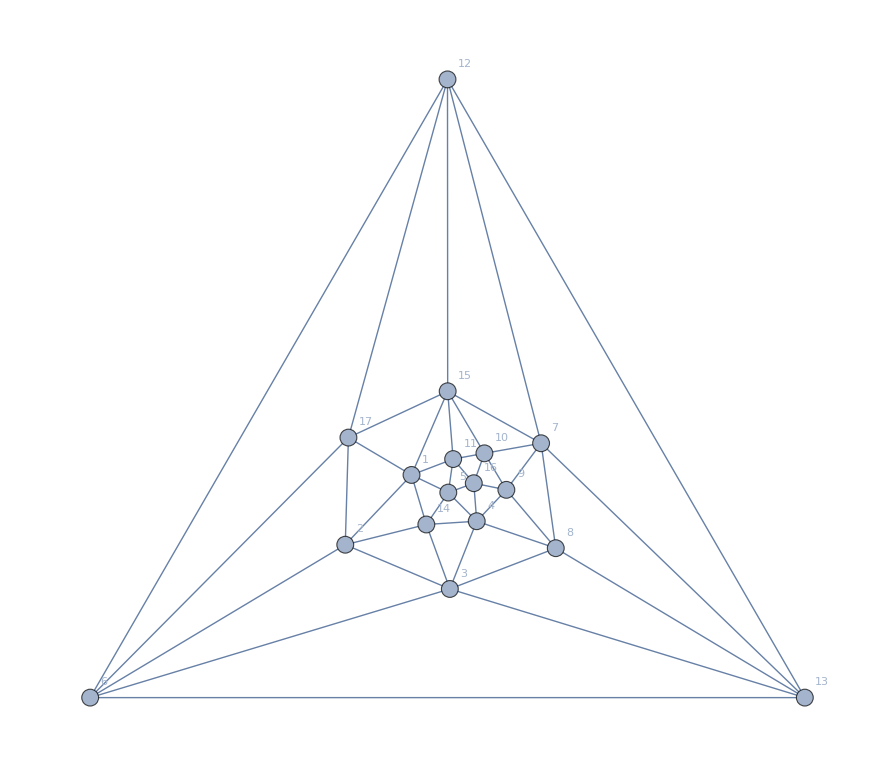

```mathematica
plantri8
```

```mathematica
Column[InspectAllEdges[VertexDelete[plantri8,14]]]
```

12<->13<->v1ax247bx359hx68fg | v14ax67bx28fgx359h | v24ax59fx168gx37bh | v29bx58fx146ax37gh
v1ax28fgx359hx467b | v14ax67gx258fx39bh | v24ax7bhx168gx359f | v29bx8fgx146ax357h
v13ax259x47bhx68fg | v14ax68bx259fx37gh | v24ax8bhx137gx569f | v29bx8fgx1467x35ah
v13ax59hx247bx68fg | v14ax68gx259fx37bh | v24ax8bhx167gx359f | v29fx35ax168gx47bh
v13ax59hx28fgx467b | v14ax69bx258fx37gh | v24ax9bhx137gx568f | v3ax168gx259fx47bh
v13ax68gx259fx47bh | v14ax69bx28fgx357h | v24bx39fx167gx58ah | v3fgx9bhx1467x258a
v13ax8ghx259fx467b | v147x25ax39bhx68fg | v24bx59fx168ax37gh | v3gx168ax259fx47bh
v13gx29fx467bx58ah | v147x29bx35ahx68fg | v24bx69fx137gx58ah | v35ax9bhx1467x28fg
v13gx29fx47bhx568a | vfgx1467x258ax39bh | v24bx7ghx168ax359f | v39bx4ahx167gx258f
v13gx68ax259fx47bh | v17gx24ax39bhx568f | v24bx8ahx137gx569f | v39bx5ahx1467x28fg
v13gx8ahx259fx467b | v18ax2fgx359hx467b | v24bx8ahx167gx359f | v39fx4bhx167gx258a
v139x2fgx467bx58ah | v18ax24bx37ghx569f | v24fx39bx167gx58ah | v4ax167gx258fx39bh
v139x2fgx47bhx568a | v18ax3ghx259fx467b | v24fx58ax167gx39bh | v4ax168gx259fx37bh
v139x25ax47bhx68fg | v18ax46bx259fx37gh | v25ax39fx168gx47bh | v4bhx69fx137gx258a
v139x5ahx247bx68fg | v18gx24ax37bhx569f | v25ax8fgx1467x39bh | v4bx168ax259fx37gh
v139x5ahx28fgx467b | v18gx29fx35ahx467b | v259x3fgx168ax47bh | v4fx167gx258ax39bh
v14ax257x39bhx68fg | v18gx3ahx259fx467b | v259x8fgx146ax37bh | v46fx9bhx137gx258a
v14ax259x37bhx68fg | v18gx46ax259fx37bh | v28ax4bhx137gx569f | v5ax1467x28fgx39bh
v14ax27bx359hx68fg | v19x247bx35ahx68fg | v28ax4bhx167gx359f | v59x146ax28fgx37bh
v14ax27gx39bhx568f | v19x28fgx35ahx467b | v28bx4ahx137gx569f | v8bx146ax259fx37gh
v14ax28bx37ghx569f | v2ax168gx359fx47bh | v28bx4ahx167gx359f | v8gx146ax259fx37bh
v14ax28gx37bhx569f | v2fgx359x168ax47bh | v28bx59fx146ax37gh | v9bx146ax258fx37gh
v14ax29bx357hx68fg | v2fgx39bx1467x58ah | v28gx59fx146ax37bh | v9bx146ax28fgx357h
v14ax29bx37ghx568f | v2fgx58ax1467x39bh | v29bx3fgx1467x58ah | v9bx1467x28fgx35ah
v14ax567x28fgx39bh | v2gx168ax359fx47bh | v29bx4ahx137gx568f | 
v14ax569x28fgx37bh | v24ax58fx167gx39bh | v29bx46fx137gx58ah | 
12<->7<->v1adx24bx359hx68fg | v13gx69bx258fx4adh | v16gx28bx359fx4adh | v25x14adx39bhx68fg
v1gx24adx39bhx568f | v13gx69fx24bdx58ah | v16gx39bx24dfx58ah | v259x3bhx14adx68fg
v1gx24dfx39bhx568a | v13gx69fx258ax4bdh | v16gx39bx258fx4adh | v28bx3ghx14adx569f
v13ax24bx59dhx68fg | v13gx8ahx24bdx569f | v16gx39fx258ax4bdh | v28bx3ghx146ax59df
v13ax4bhx259dx68fg | v13gx8bhx24adx569f | v16gx4dfx258ax39bh | v28gx3bhx14adx569f
v13ax4bhx68gx259df | v13gx9bhx24adx568f | v16gx58ax24dfx39bh | v28gx3bhx146ax59df
v13ax46bx28fgx59dh | v13gx9bhx24dfx568a | v18ax3ghx24bdx569f | v29bx3ghx14adx568f
v13ax46bx8ghx259df | v139x24bx5adhx68fg | v18ax3ghx46bx259df | v29bx35hx14adx68fg
v13gx24ax568fx9bdh | v139x4bhx2dfgx568a | v18ax46bx2dfgx359h | v3ax4bhx168gx259df
v13gx24fx568ax9bdh | v139x4bhx25adx68fg | v18gx3ahx46bx259df | v3bx146ax28fgx59dh
v13gx28ax4bdhx569f | v139x46bx2dfgx58ah | v18gx3bhx24adx569f | v3bx168gx259fx4adh
v13gx28bx4adhx569f | v139x46bx28fgx5adh | v18gx3bhx46ax259df | v3bx4ahx168gx259df
v13gx29bx4adhx568f | v14ax3bhx259dx68fg | v18gx46bx29dfx35ah | v3bx8ghx146ax259df
v13gx29fx4bdhx568a | v14ax3bhx68gx259df | v19dx24bx35ahx68fg | v3gx146ax258fx9bdh
v13gx4ahx29bdx568f | v14ax3ghx29bdx568f | v2bx14adx359hx68fg | v3gx168ax259fx4bdh
v13gx4ahx68bx259df | v14ax3ghx68bx259df | v2bx168gx359fx4adh | v3gx4bhx168ax259df
v13gx4bhx29dfx568a | v14ax35hx29bdx68fg | v2gx14adx39bhx568f | v3gx8bhx146ax259df
v13gx4bhx68ax259df | v14x2dfgx39bhx568a | v2gx168ax359fx4bdh | v35ax4bhx168gx29df
v13gx46ax258fx9bdh | v14x25adx39bhx68fg | v24ax3bhx168gx59df | v35x146ax28fgx9bdh
v13gx46ax8bhx259df | v14x29bdx35ahx68fg | v24bxadhx168gx359f | v359x4bhx168ax2dfg
v13gx46bx29dfx58ah | v146xdfgx258ax39bh | v24bxdfgx168ax359h | v4ax3bhx168gx259df
v13gx46bx8ahx259df | v146x3fgx258ax9bdh | v24bxdghx168ax359f | v4bx168ax2dfgx359h
v13gx46fx258ax9bdh | v146x35ax28fgx9bdh | v24bx3ahx168gx59df | v4bx168gx29dfx35ah
v13gx46fx29bdx58ah | v146x39bx2dfgx58ah | v24bx3fgx168ax59dh | v4bx3ahx168gx259df
v13gx68ax259fx4bdh | v146x39bx28fgx5adh | v24bx3ghx168ax59df | v4bx3ghx168ax259df
v13gx68bx259fx4adh | v146x58ax2dfgx39bh | v24bx39fx168gx5adh | v8bx3ghx146ax259df
v13gx69bx24dfx58ah | v16gx28ax359fx4bdh | v24bx9dfx168gx35ah | v8gx3bhx146ax259df
12<->15<->v1adx28gx359hx467b | v19dx28gx35ahx467b | v27bx359x168gx4adh | v3gx1467x29bdx58ah
v13ax28gx467bx59dh | v2adx359x168gx47bh | v27gx359x168ax4bdh | v3gx168ax247bx59dh
v13ax68gx247bx59dh | v2dgx359x168ax47bh | v28ax359x167gx4bdh | v3gx168ax259dx47bh
v13ax68gx259dx47bh | v2dgx39bx1467x58ah | v28ax569x137gx4bdh | v359xadhx168gx247b
v13ax8ghx259dx467b | v2dgx58ax1467x39bh | v28bx359x167gx4adh | v359xdghx168ax247b
vdgx1467x258ax39bh | v24ax568x137gx9bdh | v28bx569x137gx4adh | v359x7bhx168gx24ad
v13gx29dx467bx58ah | v24ax59dx168gx37bh | v28bx569x14adx37gh | v359x7ghx168ax24bd
v13gx29dx47bhx568a | v24bx59dx168ax37gh | v28bx59dx146ax37gh | v359x8ahx167gx24bd
v13gx68ax259dx47bh | v24dx39bx167gx58ah | v28gx35ax1467x9bdh | v359x8bhx167gx24ad
v13gx8ahx259dx467b | v24dx58ax167gx39bh | v28gx357x146ax9bdh | v39x167gx24bdx58ah
v139x2dgx467bx58ah | v24x137gx568ax9bdh | v28gx37bx146ax59dh | v39x167gx258ax4bdh
v139x2dgx47bhx568a | v258x37gx146ax9bdh | v28gx39bx1467x5adh | v39x168gx247bx5adh
v139x28gx467bx5adh | v258x39bx167gx4adh | v28gx5adx1467x39bh | v39x168gx25adx47bh
v139x68gx247bx5adh | v258x4adx167gx39bh | v28gx567x14adx39bh | v4ax168gx259dx37bh
v139x68gx25adx47bh | v258x46ax137gx9bdh | v28gx569x14adx37bh | v4bx168ax259dx37gh
v14ax568x29bdx37gh | v258x67gx14adx39bh | v28gx59dx146ax37bh | v4dx167gx258ax39bh
v14ax68bx259dx37gh | v258x69bx137gx4adh | v28gx67bx14adx359h | v46x137gx258ax9bdh
v14ax68gx259dx37bh | v258x69bx14adx37gh | v28gx69bx14adx357h | v58x146ax29bdx37gh
v14ax68gx29bdx357h | v258x9bdx146ax37gh | v28gx9bdx146ax357h | v58x167gx24adx39bh
v18ax2dgx359hx467b | v259x37bx168gx4adh | v28gx9bdx1467x35ah | v59x168ax24bdx37gh
v18ax3ghx259dx467b | v259x37gx168ax4bdh | v29bx568x137gx4adh | v59x168gx24adx37bh
v18ax46bx259dx37gh | v259x4adx168gx37bh | v29bx568x14adx37gh | v69x137gx258ax4bdh
v18ax569x24bdx37gh | v259x4bdx168ax37gh | v29bx68gx14adx357h | v8bx146ax259dx37gh
v18gx29dx35ahx467b | v259x68ax137gx4bdh | v29dx35ax168gx47bh | v8gx146ax259dx37bh
v18gx3ahx259dx467b | v259x68bx137gx4adh | v29x137gx4bdhx568a | v8gx146ax29bdx357h
v18gx46ax259dx37bh | v259x68bx14adx37gh | v3ax168gx259dx47bh | v8gx1467x25adx39bh
v18gx569x24adx37bh | v259x68gx14adx37bh | v3gx1467x258ax9bdh | v8gx1467x29bdx35ah
12<->17<->v1adx359x247bx68fg | v18ax37gx46bx259df | v3ax47bx168gx259df | v4ax37bx168gx259df
v1adx359x28fgx467b | v18gx35ax29dfx467b | v3fgx58ax1467x29bd | v4ax68bx137gx259df
v13ax47bx259dx68fg | v18gx37bx24adx569f | v3fgx9bdx1467x258a | v4bdx69fx137gx258a
v13ax47bx68gx259df | v18gx37bx46ax259df | v3gx168ax247bx59df | v4bx137gx29dfx568a
v13ax59dx247bx68fg | v19dx35ax247bx68fg | v3gx18ax467bx259df | v4bx37gx168ax259df
v13ax59dx28fgx467b | v19dx35ax28fgx467b | v3gx47bx168ax259df | v4bx68ax137gx259df
v13gx47bx29dfx568a | v24ax37bx168gx59df | v35ax47bx168gx29df | v46bx58ax137gx29df
v13gx47bx68ax259df | v24ax9bdx137gx568f | v35ax8fgx1467x29bd | v46fx58ax137gx29bd
v13gx58ax29dfx467b | v24bx37gx168ax59df | v35ax9bdx1467x28fg | v46fx9bdx137gx258a
v139x47bx2dfgx568a | v257x39bx14adx68fg | v35ax9dfx168gx247b | v58ax69bx137gx24df
v139x47bx25adx68fg | v259x37bx14adx68fg | v359xdfgx168ax247b | v58ax69fx137gx24bd
v139x5adx247bx68fg | v27bx359x14adx68fg | v359x47bx168ax2dfg | v8ax13gx467bx259df
v139x5adx28fgx467b | v27gx39bx14adx568f | v359x67bx14adx28fg | v8ax137gx24bdx569f
v139x58ax2dfgx467b | v28ax4bdx137gx569f | v39bxdfgx1467x258a | v8ax167gx24bdx359f
v14ax357x29bdx68fg | v28ax4bdx167gx359f | v39bx4adx167gx258f | v8ax46bx137gx259df
v14ax37bx259dx68fg | v28bx37gx14adx569f | v39bx4dfx167gx258a | v8bx137gx24adx569f
v14ax37bx68gx259df | v28bx37gx146ax59df | v39bx5adx1467x28fg | v8bx167gx24adx359f
v14ax37gx29bdx568f | v28bx4adx137gx569f | v39bx567x14adx28fg | v8bx37gx146ax259df
v14ax37gx68bx259df | v28bx4adx167gx359f | v39bx58ax1467x2dfg | v8bx46ax137gx259df
v147x35ax29bdx68fg | v28gx37bx14adx569f | v39bx58ax167gx24df | v8gx13ax467bx259df
v147x39bx2dfgx568a | v28gx37bx146ax59df | v39bx58fx167gx24ad | v8gx37bx146ax259df
v147x39bx25adx68fg | v29bx357x14adx68fg | v39bx67gx14adx258f | v9bx137gx24adx568f
v17gx39bx24adx568f | v29bx37gx14adx568f | v39bx8fgx1467x25ad | v9bx137gx24dfx568a
v17gx39bx24dfx568a | v29bx4adx137gx568f | v39fx4bdx167gx258a | 
v18ax359x2dfgx467b | v3ax168gx247bx59df | v39fx58ax167gx24bd | 
v18ax37gx24bdx569f | v3ax18gx467bx259df | v4ax137gx29bdx568f | 
12<->6<->v13ax47bx28fgx59dh | v147x35ax28fgx9bdh | v18gxadhx247bx359f | v3ax18gx47bhx259df
v13ax47bx8ghx259df | v147x39bx2dfgx58ah | v18gx2adx359fx47bh | v3gx18ax47bhx259df
v13ax8fgx247bx59dh | v147x39bx28fgx5adh | v18gx24ax37bhx59df | v4ax137gx258fx9bdh
v13ax8fgx259dx47bh | v147x58ax2dfgx39bh | v18gx27bx359fx4adh | v4ax18gx37bhx259df
v13gx47bx29dfx58ah | v17gx28ax359fx4bdh | v18gx3ahx247bx59df | v4ax8bhx137gx259df
v13gx47bx8ahx259df | v17gx28bx359fx4adh | v18gx3ahx47bx259df | v4bhx58ax137gx29df
v13gx58ax29dfx47bh | v17gx39bx24dfx58ah | v18gx35ax29dfx47bh | v4bx137gx29dfx58ah
v139x47bx2dfgx58ah | v17gx39bx258fx4adh | v18gx37bx259fx4adh | v4bx18ax37ghx259df
v139x47bx28fgx5adh | v17gx39fx258ax4bdh | v18gx37bx4ahx259df | v4bx8ahx137gx259df
v139x58ax2dfgx47bh | v17gx4dfx258ax39bh | v18gx39fx247bx5adh | v4fx137gx258ax9bdh
v139x8fgx247bx5adh | v17gx58ax24dfx39bh | v18gx39fx25adx47bh | v58ax9bhx137gx24df
v139x8fgx25adx47bh | v18axdfgx247bx359h | v18gx4adx259fx37bh | v59x14adx28fgx37bh
v14ax28bx37ghx59df | v18axdghx247bx359f | v18gx47bx29dfx35ah | v8ax13gx47bhx259df
v14ax28gx37bhx59df | v18ax2dgx359fx47bh | v18gx59fx24adx37bh | v8ax137gx259fx4bdh
v14ax357x28fgx9bdh | v18ax24bx37ghx59df | v18gx7bhx24adx359f | v8ax4bhx137gx259df
v14ax37bx28fgx59dh | v18ax27gx359fx4bdh | v18gx9dfx247bx35ah | v8bx137gx259fx4adh
v14ax37bx8ghx259df | v18ax3fgx247bx59dh | v24ax58fx137gx9bdh | v8bx14adx259fx37gh
v14ax37gx258fx9bdh | v18ax3fgx259dx47bh | v24fx58ax137gx9bdh | v8bx14ax37ghx259df
v14ax37gx8bhx259df | v18ax3ghx247bx59df | v259x8fgx14adx37bh | v8bx4ahx137gx259df
v14ax58fx29bdx37gh | v18ax3ghx47bx259df | v28ax59fx137gx4bdh | v8gx13ax47bhx259df
v14ax59dx28fgx37bh | v18ax359x2dfgx47bh | v28bx59fx137gx4adh | v8gx14adx259fx37bh
v14ax8fgx259dx37bh | v18ax37gx259fx4bdh | v28bx59fx14adx37gh | v8gx14ax37bhx259df
v14ax8fgx29bdx357h | v18ax37gx4bhx259df | v28gx59fx14adx37bh | v9bx137gx24dfx58ah
v14ax9bdx258fx37gh | v18ax4bdx259fx37gh | v29bx58fx137gx4adh | v9bx137gx258fx4adh
v14ax9bdx28fgx357h | v18ax47bx2dfgx359h | v29bx58fx14adx37gh | v9bx14adx258fx37gh
v147xdfgx258ax39bh | v18ax59fx24bdx37gh | v29bx8fgx14adx357h | v9bx14adx28fgx357h
v147x3fgx258ax9bdh | v18ax7ghx24bdx359f | v29fx58ax137gx4bdh | v9fx137gx258ax4bdh
13<->6<->v1ax28cgx359fx47bh | vfgx139cx247bx58ah | v25ax8fgx139cx47bh | v47bx8ahx13cgx259f
v1ax28fgx359cx47bh | vfgx139cx258ax47bh | v259x8fgx13acx47bh | v47bx8ghx13acx259f
v1gx28acx359fx47bh | vfgx139x47bhx258ac | v259x8fgx14acx37bh | v5ahx8fgx139cx247b
v1gx39fx47bhx258ac | vfgx147x39bhx258ac | v28ax59fx13cgx47bh | v5ax139cx28fgx47bh
v13ax59fx28cgx47bh | vfgx18acx247bx359h | v28bx59fx14acx37gh | v58fx9bhx137gx24ac
v13gx59fx28acx47bh | v17gx24fx39bcx58ah | v28gx59fx13acx47bh | v59fx8ahx13cgx247b
v14ax57hx28fgx39bc | v17gx24fx39bhx58ac | v28gx59fx14acx37bh | v59fx8ahx137gx24bc
v14ax58fx29bcx37gh | v17gx39fx4bhx258ac | v29bx58fx14acx37gh | v59fx8bhx137gx24ac
v14ax59cx28fgx37bh | v17gx4ahx258fx39bc | v29bx8fgx14acx357h | v59fx8ghx13acx247b
v14ax59fx28bcx37gh | v17gx4ahx28bcx359f | v29fx47bx13cgx58ah | v59hx8fgx13acx247b
v14ax59fx28cgx37bh | v17gx4bhx28acx359f | v29fx47bx18cgx35ah | v59x13acx28fgx47bh
v14ax7bhx28cgx359f | v18ax2fgx359cx47bh | v29fx58ax13cgx47bh | v59x14acx28fgx37bh
v14ax7bhx28fgx359c | v18ax3cgx259fx47bh | v3ahx47bx18cgx259f | v8ax13cgx259fx47bh
v14ax7ghx258fx39bc | v18ax4bcx259fx37gh | v3ahx59fx18cgx247b | v8bx14acx259fx37gh
v14ax7ghx28bcx359f | v18ax59fx24bcx37gh | v3ghx47bx18acx259f | v8gx13acx259fx47bh
v14ax8bcx259fx37gh | v18gx29fx35acx47bh | v3ghx59fx18acx247b | v8gx14acx259fx37bh
v14ax8cgx259fx37bh | v18gx3acx259fx47bh | v4ahx58fx137gx29bc | v9bx14acx258fx37gh
v14ax8fgx259cx37bh | v18gx4acx259fx37bh | v4ahx59fx137gx28bc | v9bx14acx28fgx357h
v14ax8fgx29bcx357h | v18gx59fx24acx37bh | v4ax18cgx259fx37bh | v9fx13cgx247bx58ah
v14ax9bcx258fx37gh | v19x28fgx35acx47bh | v4bhx59fx137gx28ac | v9fx13cgx258ax47bh
v14ax9bcx28fgx357h | v19x3fgx47bhx258ac | v4bx18acx259fx37gh | v9fx13gx47bhx258ac
v147x2fgx39bcx58ah | v2fgx47bx139cx58ah | v4fx137gx29bcx58ah | v9fx137gx24bcx58ah
v147x2fgx39bhx58ac | v2fgx47bx18acx359h | v4fx17gx39bhx258ac | v9fx18cgx247bx35ah
v147x3fgx9bhx258ac | v2fgx58ax139cx47bh | v4fx9bhx137gx258ac | v9fx4bhx137gx258ac
v147x5ahx28fgx39bc | v24ax59fx18cgx37bh | v47bx5ahx139cx28fg | 
v147x9bhx28fgx35ac | v24bx59fx18acx37gh | v47bx59hx13acx28fg | 
13<->3<->vacx168gx259fx47bh | vfgx1467x29bcx58ah | v2fgx9bcx1467x58ah | v5ahx8fgx1467x29bc
vahx18cgx247bx569f | vfgx168ax259cx47bh | v2fgx9bhx1467x58ac | v5ahx9bcx1467x28fg
vahx18cgx259fx467b | vfgx169x47bhx258ac | v24ax7bhx18cgx569f | v567x9bhx14acx28fg
v1acx259x47bhx68fg | vfgx9bhx1467x258ac | v24bx7ghx18acx569f | v58fx9bhx167gx24ac
v1acx59hx247bx68fg | v16ax59fx28cgx47bh | v24fx9bcx167gx58ah | v59fx7bhx146ax28cg
v1acx59hx28fgx467b | v16gx59fx28acx47bh | v24fx9bhx167gx58ac | v59fx7bhx168gx24ac
v1acx68gx259fx47bh | vghx18acx247bx569f | v257x9bhx14acx68fg | v59fx7ghx146ax28bc
v1acx8ghx259fx467b | vghx18acx259fx467b | v259x7bhx14acx68fg | v59fx7ghx168ax24bc
v1ax259cx47bhx68fg | v17gx4ahx28bcx569f | v27bx59hx14acx68fg | v59fx8ahx167gx24bc
v1ax28cgx47bhx569f | v17gx4ahx29bcx568f | v27gx9bhx14acx568f | v59fx8bhx167gx24ac
v1cgx29fx467bx58ah | v17gx4bhx28acx569f | v29bx57hx14acx68fg | v59hx6fgx18acx247b
v1cgx29fx47bhx568a | v17gx4bhx69fx258ac | v29bx7ghx14acx568f | v59hx67bx14acx28fg
v1cgx68ax259fx47bh | v17gx46fx9bhx258ac | v29fx5acx168gx47bh | v67gx9bhx14acx258f
v1cgx8ahx259fx467b | v17gx9bhx24acx568f | v29fx5ahx18cgx467b | v68bx7ghx14acx259f
v1gx28acx47bhx569f | v19cx2fgx467bx58ah | v4acx7bhx168gx259f | v68gx7bhx14acx259f
v1gx69fx47bhx258ac | v19cx2fgx47bhx568a | v4acx9bhx167gx258f | v7bhx8cgx146ax259f
vcgx168ax259fx47bh | v19cx25ax47bhx68fg | v4ahx59fx167gx28bc | v7ghx8bcx146ax259f
v14ax57hx29bcx68fg | v19cx5ahx247bx68fg | v4ahx9bcx167gx258f | v8fgx9bhx1467x25ac
v14ax7bhx259cx68fg | v19cx5ahx28fgx467b | v4bcx7ghx168ax259f | v9fx16gx47bhx258ac
v14ax7bhx28cgx569f | v19x25acx47bhx68fg | v4bhx59fx167gx28ac | v9fx167gx24bcx58ah
v14ax7ghx28bcx569f | v19x6fgx47bhx258ac | v4fx9bhx167gx258ac | v9fx168gx25acx47bh
v14ax7ghx29bcx568f | v2acx59fx168gx47bh | v46ax7bhx18cgx259f | v9fx4bhx167gx258ac
v147x5ahx29bcx68fg | v2cgx59fx168ax47bh | v46bx7ghx18acx259f | 
v147x6fgx9bhx258ac | v2fgx59cx168ax47bh | v5acx9bhx1467x28fg | 
v147x9bhx25acx68fg | v2fgx59hx18acx467b | v5ahx69fx18cgx247b | 
13<->8<->vahx13cgx247bx569f | vfgx1467x29bcx35ah | v2fgx569x13acx47bh | v29bx6fgx14acx357h
vahx13cgx259fx467b | v16ax2fgx359cx47bh | v2fgx569x14acx37bh | v29fx5ahx13cgx467b
vahx137gx24bcx569f | v16ax3cgx259fx47bh | v2fgx57hx146ax39bc | v29fx56ax13cgx47bh
vahx167gx24bcx359f | v16ax4bcx259fx37gh | v2fgx59cx146ax37bh | v3fgx5ahx1467x29bc
v1acx2fgx359hx467b | v16ax59fx24bcx37gh | v2fgx59hx13acx467b | v3fgx9bhx1467x25ac
v1acx24bx37ghx569f | v16gx29fx35acx47bh | v2fgx67bx14acx359h | v39fx4bhx167gx25ac
v1acx3ghx259fx467b | v16gx3acx259fx47bh | v2fgx69bx14acx357h | v39fx5ahx167gx24bc
v1acx46bx259fx37gh | v16gx4acx259fx37bh | v2fgx7bhx146ax359c | v4ahx56fx137gx29bc
v1ax24bcx37ghx569f | v16gx59fx24acx37bh | v2fgx9bcx146ax357h | v4bhx69fx137gx25ac
vbcx146ax259fx37gh | vghx13acx247bx569f | v2fgx9bcx1467x35ah | v4fx167gx25acx39bh
vbhx137gx24acx569f | vghx13acx259fx467b | v2fgx9bhx1467x35ac | v46fx5ahx137gx29bc
vbhx167gx24acx359f | v169x2fgx35acx47bh | v2gx13acx47bhx569f | v46fx9bhx137gx25ac
v1cgx24ax37bhx569f | v19cx2fgx35ahx467b | v2gx14acx37bhx569f | v5ahx6fgx139cx247b
v1cgx29fx35ahx467b | v2acx4bhx137gx569f | v24fx5acx167gx39bh | v5ahx69fx13cgx247b
v1cgx3ahx259fx467b | v2acx4bhx167gx359f | v24fx5ahx167gx39bc | v5ahx69fx137gx24bc
v1cgx46ax259fx37bh | v2ax13cgx47bhx569f | v25ax6fgx139cx47bh | v5fx146ax29bcx37gh
v1gx24acx37bhx569f | v2bcx4ahx137gx569f | v25ax69fx13cgx47bh | v5fx167gx24acx39bh
vcgx146ax259fx37bh | v2bcx4ahx167gx359f | v25fx4acx167gx39bh | v56fx9bhx137gx24ac
v14ax2bcx37ghx569f | v2bcx59fx146ax37gh | v25fx4ahx167gx39bc | v59hx6fgx13acx247b
v14ax2cgx37bhx569f | v2bx14acx37ghx569f | v25fx67gx14acx39bh | v6ax13cgx259fx47bh
v14ax56fx29bcx37gh | v2cgx59fx146ax37bh | v25fx69bx14acx37gh | v6bx14acx259fx37gh
v14ax6fgx259cx37bh | v2fgx5acx1467x39bh | v25fx7ghx146ax39bc | v6gx13acx259fx47bh
v14ax6fgx29bcx357h | v2fgx5ahx139cx467b | v25fx9bcx146ax37gh | v6gx14acx259fx37bh
vfgx146ax259cx37bh | v2fgx5ahx1467x39bc | v259x6fgx13acx47bh | 
vfgx146ax29bcx357h | v2fgx56ax139cx47bh | v259x6fgx14acx37bh | 
vfgx1467x25acx39bh | v2fgx567x14acx39bh | v29bx56fx14acx37gh | 
13<->7<->v1acx24bx359hx68fg | v146x3fgx9bhx258ac | v24ax3bhx18cgx569f | v3bhx46ax18cgx259f
vbhx146ax28cgx359f | v146x5ahx28fgx39bc | v24bx3ahx18cgx569f | v3bhx59fx146ax28cg
vbhx146ax28fgx359c | v146x9bhx28fgx35ac | v24bx3ghx18acx569f | v3bhx59fx168gx24ac
vbhx168gx24acx359f | vfgx146x39bhx258ac | v24bx5ahx139cx68fg | v3bhx68gx14acx259f
v1gx24acx39bhx568f | v16ax4bhx28cgx359f | v24bx59hx13acx68fg | v3bhx8cgx146ax259f
v1gx46fx39bhx258ac | v16ax4bhx28fgx359c | v24bx6fgx139cx58ah | v3cgx4bhx168ax259f
v13ax4bhx259cx68fg | v16gx24fx39bcx58ah | v24bx6fgx18acx359h | v3fgx4bhx168ax259c
v13ax4bhx28cgx569f | v16gx24fx39bhx58ac | v24bx69fx13cgx58ah | v3ghx4bcx168ax259f
v13gx4ahx28bcx569f | v16gx39fx4bhx258ac | v24bx69fx18cgx35ah | v3ghx46bx18acx259f
v13gx4ahx29bcx568f | v16gx4ahx258fx39bc | v24bx8ahx13cgx569f | v3ghx59fx146ax28bc
v13gx4bhx28acx569f | v16gx4ahx28bcx359f | v24bx8ghx13acx569f | v3ghx59fx168ax24bc
v13gx4bhx69fx258ac | v16gx4bhx28acx359f | v25ax4bhx139cx68fg | v3ghx68bx14acx259f
v13gx46fx9bhx258ac | vghx146ax258fx39bc | v25x14acx39bhx68fg | v3ghx8bcx146ax259f
v13gx9bhx24acx568f | vghx146ax28bcx359f | v259x3bhx14acx68fg | v39fx4bhx168gx25ac
v139x4bhx25acx68fg | vghx168ax24bcx359f | v259x4bhx13acx68fg | v4bhx56ax139cx28fg
v139x4bhx6fgx258ac | v169x3fgx4bhx258ac | v28ax4bhx13cgx569f | v4bhx569x13acx28fg
v14ax3bhx259cx68fg | v169x4bhx28fgx35ac | v28gx4bhx13acx569f | v4bhx6fgx139cx258a
v14ax3bhx28cgx569f | v19cx24bx35ahx68fg | v29bx3ghx14acx568f | v4bhx68ax13cgx259f
v14ax3ghx28bcx569f | v2acx4bhx168gx359f | v29bx35hx14acx68fg | v4bhx68gx13acx259f
v14ax3ghx29bcx568f | v2bx14acx359hx68fg | v29fx4bhx13cgx568a | v4bhx69fx13cgx258a
v14ax35hx29bcx68fg | v2cgx4bhx168ax359f | v29fx4bhx168gx35ac | v4fx16gx39bhx258ac
v14x25acx39bhx68fg | v2fgx4bhx139cx568a | v29fx46bx13cgx58ah | v46bx5ahx139cx28fg
v14x29bcx35ahx68fg | v2fgx4bhx168ax359c | v29fx46bx18cgx35ah | v46bx59hx13acx28fg
v14x6fgx39bhx258ac | v2fgx46bx139cx58ah | v3acx4bhx168gx259f | v46bx8ahx13cgx259f
v146x2fgx39bcx58ah | v2fgx46bx18acx359h | v3ahx46bx18cgx259f | v46bx8ghx13acx259f
v146x2fgx39bhx58ac | v2gx14acx39bhx568f | v3bhx4acx168gx259f | v5hx146ax28fgx39bc
7<->8<->vahx46bx13cgx259df | v146x5ahx2dfgx39bc | v16gx4acx25dfx39bh | v24bx6fgx139cx5adh
v1acx3ghx24bdx569f | v16ax3cgx4bhx259df | v16gx4ahx25dfx39bc | v3bhx6fgx14acx259d
v1acx3ghx46bx259df | v16ax3ghx24bcx59df | v16gx4bcx29dfx35ah | v3bhx6fgx14adx259c
v1acx46bx2dfgx359h | v16ax3ghx4bcx259df | v16gx4bhx29dfx35ac | v3ghx56fx14acx29bd
vbcx3ghx146ax259df | v16ax4bhx2dfgx359c | v16gx4dfx25acx39bh | v3ghx56fx14adx29bc
vbhx13cgx24adx569f | v16gxadhx24bcx359f | v16gx4dfx29bcx35ah | v35hx6fgx14acx29bd
vbhx146ax2dfgx359c | v16gxbdhx24acx359f | v16gx5acx24dfx39bh | v35hx6fgx14adx29bc
vbhx3cgx146ax259df | v16gx2acx359fx4bdh | v16gx5ahx24dfx39bc | v4bhx56ax13cgx29df
vbhx46ax13cgx259df | v16gx2bcx359fx4adh | v16gx5dfx24acx39bh | v4bhx56ax139cx2dfg
v1cgx3ahx46bx259df | v16gx24fx35acx9bdh | v16gx9bcx24dfx35ah | v4bhx6fgx13acx259d
v1cgx3bhx24adx569f | v16gx24fx39bcx5adh | v16gx9bhx24dfx35ac | v4bhx6fgx139cx25ad
v1cgx3bhx46ax259df | v16gx25fx39bcx4adh | v16gx9dfx24bcx35ah | v46bx5ahx13cgx29df
v1cgx46bx29dfx35ah | v16gx29fx35acx4bdh | vghx13acx24bdx569f | v46bx5ahx139cx2dfg
vcgx3bhx146ax259df | v16gx3acx259fx4bdh | vghx146ax25dfx39bc | v5hx146ax2dfgx39bc
v13gx2acx4bdhx569f | v16gx3acx4bhx259df | vghx3bcx146ax259df | v56x14acx2dfgx39bh
v13gx2bcx4adhx569f | v16gx3ahx24bcx59df | vghx46bx13acx259df | v6ax4bhx13cgx259df
v13gx46fx25acx9bdh | v16gx3ahx4bcx259df | v2bcx3ghx14adx569f | v6bx13cgx259fx4adh
v13gx56fx24acx9bdh | v16gx3bcx259fx4adh | v2bcx3ghx146ax59df | v6bx14acx2dfgx359h
v13gx56fx29bcx4adh | v16gx3bcx4ahx259df | v2bx13cgx4adhx569f | v6bx3ghx14acx259df
v13gx69fx25acx4bdh | v16gx3bhx24acx59df | v2cgx3bhx14adx569f | v6bx4ahx13cgx259df
v146xdfgx25acx39bh | v16gx3bhx4acx259df | v2cgx3bhx146ax59df | v6gx13acx259fx4bdh
v146x2fgx35acx9bdh | v16gx35fx24acx9bdh | v2fgx46bx13acx59dh | v6gx14acx25dfx39bh
v146x2fgx39bcx5adh | v16gx35fx29bcx4adh | v2fgx46bx139cx5adh | v6gx3bhx14acx259df
v146x3fgx25acx9bdh | v16gx39fx24bcx5adh | v2gx13acx4bdhx569f | v6gx4bhx13acx259df
v146x5acx2dfgx39bh | v16gx39fx25acx4bdh | v24bx6fgx13acx59dh | 
7<->9<->v1acx35hx24bdx68fg | v146xbdhx28fgx35ac | v25cx3bhx14adx68fg | v3ghx5dfx146ax28bc
v1adx35hx24bcx68fg | v146x3bcx2dfgx58ah | v25dx3bhx14acx68fg | v3ghx5dfx168ax24bc
vbhx13cgx24adx568f | v146x3bcx28fgx5adh | v25dx4bhx13acx68fg | v3ghx56fx14adx28bc
vbhx13cgx24dfx568a | v146x3bhxdfgx258ac | v25x13acx4bdhx68fg | v3ghx56fx18acx24bd
vbhx168gx24dfx35ac | v146x3bhx2dfgx58ac | v3acx4bhx168gx25df | v3ghx68bx14acx25df
v1cgx3bhx24adx568f | v146x3fgxbdhx258ac | v3ahx46bx18cgx25df | v3ghx8bcx146ax25df
v1cgx3bhx24dfx568a | v16gx3bcx24dfx58ah | v3bhxdfgx146ax258c | v35cx4bhx168ax2dfg
v1dgx3bhx24acx568f | v16gx3bcx258fx4adh | v3bhx4acx168gx25df | v35hxdfgx146ax28bc
v1dgx3bhx46fx258ac | v16gx3bhx24dfx58ac | v3bhx4dfx168gx25ac | v35hxdfgx168ax24bc
v13cx24bx5adhx68fg | v16gx3bhx4dfx258ac | v3bhx46ax18cgx25df | v35hx4bcx168ax2dfg
v13cx4bhx2dfgx568a | v16gx35fx28acx4bdh | v3bhx46fx18cgx25ad | v35hx46bx18acx2dfg
v13cx4bhx25adx68fg | v16gx35fx28bcx4adh | v3bhx5acx168gx24df | v35hx6fgx14adx28bc
v13cx46bx2dfgx58ah | v16x28fgx35acx4bdh | v3bhx5dfx146ax28cg | v35hx6fgx18acx24bd
v13cx46bx28fgx5adh | v16x3fgx4bdhx258ac | v3bhx5dfx168gx24ac | v35hx68bx14acx2dfg
v13gxbdhx24acx568f | v2bcx3ghx14adx568f | v3bhx56ax18cgx24df | v35hx8bcx146ax2dfg
v13gx2bcx4adhx568f | v2bcx35hx14adx68fg | v3bhx56fx14adx28cg | v4bhx68ax13cgx25df
v13gx46fxbdhx258ac | v2bdx3ghx14acx568f | v3bhx56fx18cgx24ad | v4bhx68gx13acx25df
v13gx56fx28acx4bdh | v2bdx35hx14acx68fg | v3bhx568x14acx2dfg | v46bx5dhx13acx28fg
v13gx56fx28bcx4adh | v2bx13cgx4adhx568f | v3bhx58cx146ax2dfg | v46bx8ahx13cgx25df
v13x24bcx5adhx68fg | v2cgx3bhx14adx568f | v3bhx6fgx14adx258c | v46bx8ghx13acx25df
v13x25acx4bdhx68fg | v2dfx4bhx13cgx568a | v3bhx68gx14acx25df | v5hx13acx24bdx68fg
v13x6fgx4bdhx258ac | v2dfx4bhx168gx35ac | v3bhx8cgx146ax25df | v56x13acx28fgx4bdh
v14cx3bhx2dfgx568a | v2dfx46bx13cgx58ah | v3cgx4bhx168ax25df | v6bx13cgx24dfx58ah
v14cx3bhx25adx68fg | v2dfx46bx18cgx35ah | v3fx16gx4bdhx258ac | v6bx13cgx258fx4adh
v14dx3bhx25acx68fg | v2dgx3bhx14acx568f | v3ghx4bcx168ax25df | v6bx18cgx24dfx35ah
v14dx3bhx6fgx258ac | v24bx5dhx13acx68fg | v3ghx46bx18acx25df | v6fx13gx4bdhx258ac
7<->10<->v13cx24bx59dhx68fg | v146xdfgx28bcx359h | v16gx4dhx28bcx359f | v35hx4dfx168gx29bc
v13cx4bhx259dx68fg | v146xdghx258fx39bc | v16gx58cx24dfx39bh | v35hx46bx18cgx29df
v13cx4bhx68gx259df | v146xdghx28bcx359f | v16gx58hx24dfx39bc | v35hx46fx18cgx29bd
v13cx46bx28fgx59dh | v146x3bcx28fgx59dh | v16x28cgx359fx4bdh | v35hx69bx18cgx24df
v13cx46bx8ghx259df | v146x3bcx8ghx259df | v16x28fgx359cx4bdh | v35hx69fx18cgx24bd
v13gx24cx568fx9bdh | v146x3bhx28cgx59df | v168x3cgx4bhx259df | v35hx9bcx168gx24df
v13gx28cx4bdhx569f | v146x3bhx8cgx259df | v168x3ghx24bcx59df | v35hx9dfx168gx24bc
v13gx4dhx28bcx569f | v146x3cgx258fx9bdh | v168x3ghx4bcx259df | v4bhx568x13cgx29df
v13gx4dhx29bcx568f | v146x3cgx8bhx259df | v168x4bhx2dfgx359c | v4bhx568x139cx2dfg
v13gx46fx258cx9bdh | v146x3fgx258cx9bdh | v18cx3ghx24bdx569f | v4cx3bhx168gx259df
v13gx69fx258cx4bdh | v146x3fgx28bcx59dh | v18cx3ghx46bx259df | v4hx13cgx29bdx568f
v13x24bcx59dhx68fg | v146x3ghx28bcx59df | v18cx46bx2dfgx359h | v4hx168gx25dfx39bc
v13x259cx4bdhx68fg | v146x3ghx8bcx259df | v19cx35hx24bdx68fg | v4hx3bcx168gx259df
v13x28cgx4bdhx569f | v146x35cx28fgx9bdh | v19dx35hx24bcx68fg | v4hx68bx13cgx259df
v14cx3bhx259dx68fg | v146x35fx28cgx9bdh | v24bx5dhx139cx68fg | v46bx5dhx139cx28fg
v14cx3bhx68gx259df | v146x5dfx28cgx39bh | v24cx3bhx168gx59df | v46bx58hx13cgx29df
v14cx3ghx29bdx568f | v146x5dhx28fgx39bc | v24dx3bhx18cgx569f | v46bx58hx139cx2dfg
v14cx3ghx68bx259df | v146x58cx2dfgx39bh | v24x13cgx568fx9bdh | v46x13cgx258fx9bdh
v14cx35hx29bdx68fg | v146x58hx2dfgx39bc | v25dx4bhx139cx68fg | v46x18cgx25dfx39bh
v14dx3bhx259cx68fg | v146x8bcx2dfgx359h | v25x139cx4bdhx68fg | v46x3bhx18cgx259df
v14dx3bhx28cgx569f | v146x8bhx2dfgx359c | v3cx4bhx168gx259df | v46x8bhx13cgx259df
v14dx3ghx28bcx569f | v146x8cgx25dfx39bh | v3hx168gx24bcx59df | v5hx139cx24bdx68fg
v14dx3ghx29bcx568f | v146x8ghx25dfx39bc | v3hx18cgx24bdx569f | v5hx168gx24dfx39bc
v14dx35hx29bcx68fg | v16gx28cx359fx4bdh | v3hx4bcx168gx259df | v56x139cx28fgx4bdh
v146xbdhx28cgx359f | v16gx39fx258cx4bdh | v3hx46bx18cgx259df | v56x18cgx24dfx39bh
v146xbdhx28fgx359c | v16gx4dfx258cx39bh | v35cx4bhx168gx29df | v68x4bhx13cgx259df
v146xdfgx258cx39bh | v16gx4dhx258fx39bc | v35hx4bcx168gx29df | v8hx46bx13cgx259df
7<->15<->vdgx146x39bhx258ac | v24x13cgx568ax9bdh | v3ghx4bcx168ax259d | v4bhx68ax13cgx259d
v13gx568x24acx9bdh | v24x168gx35acx9bdh | v3ghx46bx18acx259d | v4bhx68gx13acx259d
v13gx568x29bcx4adh | v24x168gx39bcx5adh | v3ghx568x14acx29bd | v4bhx68gx139cx25ad
v13gx569x28acx4bdh | v25x168gx39bcx4adh | v3ghx568x14adx29bc | v4dx16gx39bhx258ac
v13gx569x28bcx4adh | v28gx46bx13acx59dh | v3ghx569x14adx28bc | v46bx8ahx13cgx259d
v146x2dgx39bcx58ah | v28gx46bx139cx5adh | v3ghx569x18acx24bd | v46bx8ghx13acx259d
v146x2dgx39bhx58ac | v29dx4bhx13cgx568a | v3ghx59dx146ax28bc | v46x1dgx39bhx258ac
v146x28gx35acx9bdh | v29dx4bhx168gx35ac | v3ghx59dx168ax24bc | v46x13cgx258ax9bdh
v146x28gx39bcx5adh | v29dx46bx13cgx58ah | v3ghx68bx14acx259d | v46x13cgx29bdx58ah
v16gx24dx39bcx58ah | v29dx46bx18cgx35ah | v3ghx8bcx146ax259d | v46x13gx9bdhx258ac
v16gx24dx39bhx58ac | v3acx4bhx168gx259d | v3gx146ax258cx9bdh | v46x18cgx25adx39bh
v16gx258x39bcx4adh | v3ahx46bx18cgx259d | v3gx146ax28bcx59dh | v46x18cgx29bdx35ah
v16gx359x28acx4bdh | v3bhx4acx168gx259d | v3gx146x9bdhx258ac | v56x14adx28cgx39bh
v16gx359x28bcx4adh | v3bhx46ax18cgx259d | v3gx168ax24bcx59dh | v56x18cgx24adx39bh
v2dgx4bhx139cx568a | v3bhx569x14adx28cg | v3gx168ax259cx4bdh | v6gx139cx24bdx58ah
v2dgx4bhx168ax359c | v3bhx569x18cgx24ad | v3gx169x4bdhx258ac | v6gx139cx258ax4bdh
v2dgx46bx139cx58ah | v3bhx59dx146ax28cg | v35hx68gx14acx29bd | v6gx139x4bdhx258ac
v2dgx46bx18acx359h | v3bhx59dx168gx24ac | v35hx68gx14adx29bc | v6gx14adx258cx39bh
v2gx139cx4bdhx568a | v3bhx68gx14acx259d | v35x146ax28cgx9bdh | v6gx14adx28bcx359h
v2gx168ax359cx4bdh | v3bhx68gx14adx259c | v35x168gx24acx9bdh | v6gx14dx39bhx258ac
v24bx68gx13acx59dh | v3bhx8cgx146ax259d | v35x168gx29bcx4adh | v6gx18acx24bdx359h
v24bx68gx139cx5adh | v3cgx4bhx168ax259d | v39x16gx4bdhx258ac | v69x13gx4bdhx258ac
15<->10<->v13cx28gx467bx59dh | v19dx568x24bcx37gh | v25dx8cgx1467x39bh | v35x1467x28cgx9bdh
v13cx68gx247bx59dh | v2dgx568x139cx47bh | v25dx8ghx139cx467b | v359x4dhx167gx28bc
v13cx68gx259dx47bh | v2dgx58cx1467x39bh | v25dx8ghx1467x39bc | v39x167gx258cx4bdh
v13cx8ghx259dx467b | v2dgx58hx139cx467b | v258xdghx139cx467b | v4cx168gx259dx37bh
vdgx1467x258cx39bh | v2dgx58hx1467x39bc | v258xdghx1467x39bc | v4dhx568x137gx29bc
v14cx568x29bdx37gh | v2dx168gx359cx47bh | v258x3cgx1467x9bdh | v4dhx569x137gx28bc
v14cx68bx259dx37gh | v2dx18cgx359hx467b | v258x39cx167gx4bdh | v4dx167gx258cx39bh
v14cx68gx259dx37bh | v24cx568x137gx9bdh | v258x4dhx167gx39bc | v4dx167gx28bcx359h
v14cx68gx29bdx357h | v24cx59dx168gx37bh | v258x467x13cgx9bdh | v4dx168gx259cx37bh
v14dx568x29bcx37gh | v24dx567x18cgx39bh | v258x67gx139cx4bdh | v4dx168gx29bcx357h
v14dx569x28bcx37gh | v24dx569x18cgx37bh | v258x9dhx13cgx467b | v46x137gx258cx9bdh
v14dx569x28cgx37bh | v24dx57hx168gx39bc | v27gx568x139cx4bdh | v46x137gx28bcx59dh
v14dx68gx259cx37bh | v24dx58cx167gx39bh | v28cx359x167gx4bdh | v46x18cgx259dx37bh
v14dx68gx29bcx357h | v24dx58hx167gx39bc | v28cx569x137gx4bdh | v46x18cgx29bdx357h
v146x59dx28bcx37gh | v24dx59cx168gx37bh | v28gx35cx1467x9bdh | v47hx568x13cgx29bd
v146x59dx28cgx37bh | v24dx67bx18cgx359h | v28gx5dhx139cx467b | v5dhx68gx139cx247b
v146x8bcx259dx37gh | v24dx69bx18cgx357h | v28gx5dhx1467x39bc | v5dx1467x28cgx39bh
v146x8cgx259dx37bh | v24dx7bhx168gx359c | v28x13cgx467bx59dh | v568xdghx139cx247b
v168x2dgx359cx47bh | v24dx8bcx167gx359h | v28x167gx359cx4bdh | v568x7ghx139cx24bd
v168x3cgx259dx47bh | v24dx8bhx167gx359c | v29cx568x137gx4bdh | v568x9dhx13cgx247b
v168x4bcx259dx37gh | v24dx9bcx168gx357h | v29dx35cx168gx47bh | v568x9dhx137gx24bc
v168x59dx24bcx37gh | v247x568x13cgx9bdh | v29dx35hx18cgx467b | v68x13cgx247bx59dh
v18cx2dgx359hx467b | v25dx39cx168gx47bh | v29dx568x13cgx47bh | v68x13cgx259dx47bh
v18cx3ghx259dx467b | v25dx39hx18cgx467b | v29dx58hx13cgx467b | v68x137gx24bcx59dh
v18cx46bx259dx37gh | v25dx467x18cgx39bh | v3cx168gx259dx47bh | v68x137gx259cx4bdh
v18cx569x24bdx37gh | v25dx47hx168gx39bc | v3gx1467x258cx9bdh | v69x137gx258cx4bdh
v19cx568x24bdx37gh | v25dx68gx139cx47bh | v3hx18cgx259dx467b | v8hx13cgx259dx467b
15<->11<->vdgx39hx1467x258ac | v28cx569x137gx4adh | v3ahx467x18cgx259d | v46x19dx37ghx258ac
v14cx29dx37ghx568a | v28cx569x14adx37gh | v3cgx47hx168ax259d | v46x9dhx137gx258ac
v146x29dx37ghx58ac | v28cx59dx146ax37gh | v3ghx467x18acx259d | v467x8ahx13cgx259d
v169x24dx37ghx58ac | v28gx39cx1467x5adh | v3gx9dhx1467x258ac | v467x8ghx13acx259d
v19cx24dx37ghx568a | v28gx467x13acx59dh | v359x4dhx167gx28ac | v47hx68ax13cgx259d
v2dgx39cx1467x58ah | v28gx467x139cx5adh | v37hx4acx168gx259d | v47hx68gx13acx259d
v2dgx39hx1467x58ac | v28gx9dhx1467x35ac | v37hx46ax18cgx259d | v47hx68gx139cx25ad
v2dgx467x139cx58ah | v28x167gx359cx4adh | v37hx569x14adx28cg | v568x9dhx137gx24ac
v2dgx467x18acx359h | v29cx568x137gx4adh | v37hx569x18cgx24ad | v68x137gx24acx59dh
v2dgx47hx139cx568a | v29cx568x14adx37gh | v37hx59dx146ax28cg | v68x137gx259cx4adh
v2dgx47hx168ax359c | v29cx68gx14adx357h | v37hx59dx168gx24ac | v68x14acx259dx37gh
v24cx59dx168ax37gh | v29dx3cgx1467x58ah | v37hx68gx14acx259d | v68x14adx259cx37gh
v24dx39cx167gx58ah | v29dx3ghx1467x58ac | v37hx68gx14adx259c | v69x137gx258cx4adh
v24dx39hx167gx58ac | v29dx4acx168gx357h | v37hx8cgx146ax259d | v69x14adx258cx37gh
v24dx569x18acx37gh | v29dx46ax18cgx357h | v39xdghx1467x258ac | v69x14adx28cgx357h
v24dx59cx168ax37gh | v29dx467x13cgx58ah | v39x1467x28cgx5adh | v69x14dx37ghx258ac
v24dx67gx139cx58ah | v29dx467x18cgx35ah | v39x167gx258cx4adh | v69x18cgx24adx357h
v24dx67gx18acx359h | v29dx47hx13cgx568a | v39x4dhx167gx258ac | v69x4dhx137gx258ac
v24dx7ghx139cx568a | v29dx47hx168gx35ac | v4cx168ax259dx37gh | v8cx146ax259dx37gh
v24dx7ghx168ax359c | v29dx568x14acx37gh | v4dhx569x137gx28ac | v9dx146ax258cx37gh
v24dx8acx167gx359h | v29dx58cx146ax37gh | v4dx167gx28acx359h | v9dx146ax28cgx357h
v24dx8ahx167gx359c | v29dx68gx14acx357h | v4dx168ax259cx37gh | v9dx146x37ghx258ac
v247x68gx13acx59dh | v29dx8cgx146ax357h | v4dx169x37ghx258ac | v9dx1467x28cgx35ah
v247x68gx139cx5adh | v29dx8cgx1467x35ah | v4dx39hx167gx258ac | v9dx168gx24acx357h
v258x39cx167gx4adh | v29dx8ghx1467x35ac | v46x137gx28acx59dh | v9dx3ghx1467x258ac
v28cx359x167gx4adh | v3acx47hx168gx259d | v46x18acx259dx37gh | 
15<->1<->vdgx28acx359hx467b | v29dx68gx35acx47bh | v39cx68gx25adx47bh | v46x37gx9bdhx258ac
vdgx39hx467bx258ac | v29dx8cgx35ahx467b | v39xdghx467bx258ac | v46x9bdx37ghx258ac
vdgx467x39bhx258ac | v3acx68gx247bx59dh | v39x28cgx467bx5adh | v47hx68gx25adx39bc
v2adx68gx359cx47bh | v3acx68gx259dx47bh | v39x67gx4bdhx258ac | v47hx68gx29bdx35ac
v2dgx39cx467bx58ah | v3acx8ghx259dx467b | v4acx568x29bdx37gh | v569x8acx24bdx37gh
v2dgx39cx47bhx568a | v3ahx8cgx259dx467b | v4acx68bx259dx37gh | v569x8cgx24adx37bh
v2dgx467x39bcx58ah | v3cgx68ax259dx47bh | v4acx68gx259dx37bh | v57hx68gx24adx39bc
v2dgx467x39bhx58ac | v3cgx8ahx259dx467b | v4acx68gx29bdx357h | v59cx68gx24adx37bh
v2dgx68ax359cx47bh | v3ghx8acx259dx467b | v4adx568x29bcx37gh | v59dx68ax24bcx37gh
v2dgx8acx359hx467b | v3gx28acx467bx59dh | v4adx569x28bcx37gh | v59dx68gx24acx37bh
v24dx67gx39bcx58ah | v3gx467x9bdhx258ac | v4adx569x28cgx37bh | v68gxadhx247bx359c
v24dx67gx39bhx58ac | v3gx9dhx467bx258ac | v4adx68gx259cx37bh | v68gx7bhx24adx359c
v247x68gx35acx9bdh | v357x68gx24acx9bdh | v4adx68gx29bcx357h | v68gx9bcx24adx357h
v247x68gx39bcx5adh | v357x68gx29bcx4adh | v4bcx68ax259dx37gh | v68gx9bdx24acx357h
v257x68gx39bcx4adh | v359x67gx28acx4bdh | v4dx29bcx37ghx568a | v68gx9dhx247bx35ac
v258x67gx39bcx4adh | v359x67gx28bcx4adh | v4dx67gx39bhx258ac | v69x24bdx37ghx58ac
v27bx68gx359cx4adh | v37bx68gx24acx59dh | v4dx69bx37ghx258ac | v69x37gx4bdhx258ac
v28gx3acx467bx59dh | v37bx68gx259cx4adh | v46ax59dx28bcx37gh | v69x4bdx37ghx258ac
v28gx39cx467bx5adh | v37gx568x24acx9bdh | v46ax59dx28cgx37bh | v9dx24bcx37ghx568a
v28gx467x35acx9bdh | v37gx568x29bcx4adh | v46ax8bcx259dx37gh | v9dx28cgx35ahx467b
v28gx467x39bcx5adh | v37gx569x28acx4bdh | v46ax8cgx259dx37bh | v9dx3ghx467bx258ac
v29dx3cgx467bx58ah | v37gx569x28bcx4adh | v46bx8acx259dx37gh | v9dx46bx37ghx258ac
v29dx3cgx47bhx568a | v39cx68gx247bx5adh | v46x29bdx37ghx58ac | 
15<->17<->v1adx359x28cgx467b | v29dx47bx13cgx568a | v37bx59dx146ax28cg | v46ax59dx137gx28bc
v1dgx359x28acx467b | v29dx47bx168gx35ac | v37bx59dx168gx24ac | v46bx59dx137gx28ac
v13ax59dx28cgx467b | v29dx58ax13cgx467b | v37bx68gx14acx259d | v46x9bdx137gx258ac
vdgx139cx247bx568a | v3acx47bx168gx259d | v37bx68gx14adx259c | v47bx68ax13cgx259d
vdgx139cx258ax467b | v3acx59dx168gx247b | v37bx8cgx146ax259d | v47bx68gx13acx259d
vdgx139x467bx258ac | v3ax18cgx259dx467b | v37gx4bcx168ax259d | v47bx68gx139cx25ad
vdgx1467x258ax39bc | v3cgx47bx168ax259d | v37gx46bx18acx259d | v5adx68gx139cx247b
vdgx168ax247bx359c | v3cgx59dx168ax247b | v37gx568x14acx29bd | v568x9bdx137gx24ac
vdgx39bx1467x258ac | v3gx1467x29bdx58ac | v37gx568x14adx29bc | v58x167gx24adx39bc
v13gx59dx28acx467b | v3gx18acx259dx467b | v37gx569x14adx28bc | v59dx68ax13cgx247b
v2adx359x18cgx467b | v3gx19dx467bx258ac | v37gx569x18acx24bd | v59dx68ax137gx24bc
v2dgx359x18acx467b | v3gx9bdx1467x258ac | v37gx59dx146ax28bc | v59dx68bx137gx24ac
v2dgx39bx1467x58ac | v357x68gx14acx29bd | v37gx59dx168ax24bc | v59dx68gx13acx247b
v2dgx47bx139cx568a | v357x68gx14adx29bc | v37gx68bx14acx259d | v69x4bdx137gx258ac
v2dgx47bx168ax359c | v359x4adx167gx28bc | v37gx8bcx146ax259d | v8ax13cgx259dx467b
v2dgx58ax139cx467b | v359x4bdx167gx28ac | v39x1dgx467bx258ac | v8gx13acx259dx467b
v2dgx58ax1467x39bc | v359x67bx14adx28cg | v39x167gx24bdx58ac | v8gx139cx25adx467b
v24dx39bx167gx58ac | v359x67bx18cgx24ad | v39x18cgx25adx467b | v8gx1467x25adx39bc
v24dx58ax167gx39bc | v359x67gx14adx28bc | v39x4bdx167gx258ac | v8gx1467x29bdx35ac
v258x4adx167gx39bc | v359x67gx18acx24bd | v4adx568x137gx29bc | v9dx13cgx247bx568a
v28ax59dx13cgx467b | v359x8acx167gx24bd | v4adx569x137gx28bc | v9dx13cgx258ax467b
v28gx5adx139cx467b | v359x8bcx167gx24ad | v4bdx569x137gx28ac | v9dx13gx467bx258ac
v28gx5adx1467x39bc | v37bx4acx168gx259d | v4dx137gx29bcx568a | v9dx137gx24bcx568a
v28gx59dx13acx467b | v37bx46ax18cgx259d | v4dx167gx258ax39bc | v9dx168gx247bx35ac
v28gx9bdx1467x35ac | v37bx569x14adx28cg | v4dx39bx167gx258ac | v9dx46bx137gx258ac
v29dx35ax18cgx467b | v37bx569x18cgx24ad | v4dx69bx137gx258ac | 
17<->1<->vadx247bx359cx68fg | v359x8acx2dfgx467b | v37gx46fx29bdx58ac | v4adx67bx28cgx359f
vadx28cgx359fx467b | v37bx4acx259dx68fg | v37gx46fx9bdx258ac | v4adx67bx28fgx359c
vadx28fgx359cx467b | v37bx4acx68gx259df | v37gx68ax24bcx59df | v4adx67gx258fx39bc
vdgx28acx359fx467b | v37bx4adx259cx68fg | v37gx68bx24acx59df | v4adx67gx28bcx359f
vdgx39fx467bx258ac | v37bx4adx28cgx569f | v37gx69bx24dfx58ac | v4bdx67gx28acx359f
v257x4adx39bcx68fg | v37bx46ax28cgx59df | v37gx69fx24bdx58ac | v467x5adx28fgx39bc
v27bx4adx359cx68fg | v37bx46ax8cgx259df | v37gx8acx24bdx569f | v467x58ax2dfgx39bc
v27gx4adx39bcx568f | v37bx68gx24acx59df | v37gx8bcx24adx569f | v467x9bdx28fgx35ac
v3acx47bx259dx68fg | v37bx8cgx24adx569f | v37gx9bcx24adx568f | v47bx68ax2dfgx359c
v3acx47bx68gx259df | v37gx4acx29bdx568f | v37gx9bcx24dfx568a | v47bx68gx29dfx35ac
v3acx59dx247bx68fg | v37gx4acx68bx259df | v37gx9bdx24acx568f | v47x2dfgx39bcx568a
v3acx59dx28fgx467b | v37gx4adx28bcx569f | v37gx9dfx24bcx568a | v47x25adx39bcx68fg
v3ax28cgx467bx59df | v37gx4adx29bcx568f | v39bx4dfx67gx258ac | v47x29bdx35acx68fg
v3ax8cgx467bx259df | v37gx4bcx29dfx568a | v39bx467xdfgx258ac | v58ax67gx24dfx39bc
v3cgx47bx29dfx568a | v37gx4bcx68ax259df | v39bx467x2dfgx58ac | v7gx24adx39bcx568f
v3cgx47bx68ax259df | v37gx4bdx28acx569f | v39bx67gx24dfx58ac | v7gx24dfx39bcx568a
v3cgx58ax29dfx467b | v37gx4bdx69fx258ac | v39cx47bx2dfgx568a | v8ax2dfgx359cx467b
v3fgx467x9bdx258ac | v37gx4dfx29bcx568a | v39cx47bx25adx68fg | v8ax3cgx467bx259df
v3gx28acx467bx59df | v37gx4dfx69bx258ac | v39cx5adx247bx68fg | v8gx29dfx35acx467b
v3gx29dfx467bx58ac | v37gx46ax28bcx59df | v39cx5adx28fgx467b | v8gx3acx467bx259df
v3gx8acx467bx259df | v37gx46ax8bcx259df | v39cx58ax2dfgx467b | v9dx247bx35acx68fg
v3gx9dfx467bx258ac | v37gx46bx28acx59df | v39fx4bdx67gx258ac | v9dx28fgx35acx467b
v35ax8cgx29dfx467b | v37gx46bx29dfx58ac | v39xdfgx467bx258ac | v9dx3fgx467bx258ac
v357x4acx29bdx68fg | v37gx46bx8acx259df | v39x2dfgx467bx58ac | 
v357x4adx29bcx68fg | v37gx46bx9dfx258ac | v4adx567x28fgx39bc | 
17<->2<->vadx18cgx359fx467b | v37bx4adx18cgx569f | v39fx5adx18cgx467b | v47bx68gx13acx59df
v1adx47bx359cx68fg | v37bx46ax18cgx59df | v4acx9bdx137gx568f | v47bx9dfx13cgx568a
vdgx18acx359fx467b | v37bx59cx14adx68fg | v4adx58fx167gx39bc | v47bx9dfx168gx35ac
v147x5adx39bcx68fg | v37bx59dx14acx68fg | v4adx67bx18cgx359f | v5adx8fgx139cx467b
v147x9bdx35acx68fg | v37bx68gx14acx59df | v4adx8bcx137gx569f | v5adx8fgx1467x39bc
v17gx4adx39bcx568f | v37bx8cgx14adx569f | v4adx8bcx167gx359f | v57x14adx39bcx68fg
v19dx47bx35acx68fg | v37bx8cgx146ax59df | v4adx9bcx137gx568f | v58axdfgx139cx467b
v3acx47bx168gx59df | v37gx4bcx168ax59df | v4bdx67gx18acx359f | v58axdfgx1467x39bc
v3ax18cgx467bx59df | v37gx4bdx18acx569f | v4bdx69fx137gx58ac | v58ax9dfx13cgx467b
v3cgx47bx168ax59df | v37gx46bx18acx59df | v4bdx8acx137gx569f | v59dx8fgx13acx467b
v3fgx59dx18acx467b | v37gx68bx14acx59df | v4bdx8acx167gx359f | v7bx14adx359cx68fg
v3fgx9bdx1467x58ac | v37gx8bcx14adx569f | v4dfx58ax167gx39bc | v7gx14adx39bcx568f
v3gx18acx467bx59df | v37gx8bcx146ax59df | v46fx9bdx137gx58ac | v8ax13cgx467bx59df
v35ax9dfx18cgx467b | v37gx9bcx14adx568f | v47bxdfgx139cx568a | v8fgx9bdx1467x35ac
v357x9bcx14adx68fg | v37gx9bdx14acx568f | v47bxdfgx168ax359c | v8gx13acx467bx59df
v357x9bdx14acx68fg | v39bxdfgx1467x58ac | v47bx5adx139cx68fg | 
v359xdfgx18acx467b | v39bx4dfx167gx58ac | v47bx59dx13acx68fg | 
v37bx4acx168gx59df | v39fx4bdx167gx58ac | v47bx68ax13cgx59df | 
17<->6<->v1adx47bx28cgx359f | v17gx4bdx28acx359f | v37gx58fx14acx29bd | v5adx8fgx139cx247b
v1adx47bx28fgx359c | v17gx58ax24dfx39bc | v37gx58fx14adx29bc | v57x14adx28fgx39bc
v1dgx39fx47bx258ac | v18ax3cgx47bx259df | v37gx59fx14adx28bc | v58axdfgx139cx247b
v1dgx47bx28acx359f | v18ax37gx24bcx59df | v37gx59fx18acx24bd | v58ax9bcx137gx24df
v13ax47bx28cgx59df | v18ax37gx4bcx259df | v39fx47bx18cgx25ad | v58ax9dfx13cgx247b
v13ax47bx8cgx259df | v18ax47bx2dfgx359c | v4adx58fx137gx29bc | v58ax9dfx137gx24bc
v13gx47bx28acx59df | v18gx3acx47bx259df | v4adx59fx137gx28bc | v58fx9bdx137gx24ac
v13gx47bx29dfx58ac | v18gx37bx24acx59df | v4ax137gx28bcx59df | v59dx8fgx13acx247b
v13gx47bx8acx259df | v18gx37bx4acx259df | v4ax37bx18cgx259df | v7bx14adx28cgx359f
v13gx47bx9dfx258ac | v18gx47bx29dfx35ac | v4ax8bcx137gx259df | v7bx14adx28fgx359c
v139x47bxdfgx258ac | v19dx3fgx47bx258ac | v4bcx58ax137gx29df | v7bx18cgx24adx359f
v139x47bx2dfgx58ac | v19dx47bx28fgx35ac | v4bdx59fx137gx28ac | v7gx14adx258fx39bc
v14ax37bx28cgx59df | v2adx47bx18cgx359f | v4bx137gx28acx59df | v7gx14adx28bcx359f
v14ax37bx8cgx259df | v2dgx47bx18acx359f | v4bx137gx29dfx58ac | v7gx18acx24bdx359f
v14ax37gx28bcx59df | v28ax47bx13cgx59df | v4bx37gx18acx259df | v8ax13cgx247bx59df
v14ax37gx8bcx259df | v28gx47bx13acx59df | v4bx8acx137gx259df | v8ax137gx24bcx59df
v147x3fgx9bdx258ac | v3ax47bx18cgx259df | v4bx9dfx137gx258ac | v8ax4bcx137gx259df
v147x39bxdfgx258ac | v3fgx47bx18acx259d | v4dfx58ax137gx29bc | v8ax47bx13cgx259df
v147x39bx2dfgx58ac | v3gx47bx18acx259df | v4fx9bdx137gx258ac | v8bx137gx24acx59df
v147x5adx28fgx39bc | v35ax47bx18cgx29df | v47bxdfgx139cx258a | v8bx37gx14acx259df
v147x58ax2dfgx39bc | v357x8fgx14acx29bd | v47bx5adx139cx28fg | v8bx4acx137gx259df
v147x9bdx28fgx35ac | v357x8fgx14adx29bc | v47bx58ax13cgx29df | v8gx13acx247bx59df
v17gx39bx24dfx58ac | v359x47bx18acx2dfg | v47bx58ax139cx2dfg | v8gx37bx14acx259df
v17gx39bx4dfx258ac | v37bx59fx14adx28cg | v47bx59dx13acx28fg | v8gx47bx13acx259df
v17gx39fx4bdx258ac | v37bx59fx18cgx24ad | v47bx8fgx13acx259d | v9bx137gx24dfx58ac
v17gx4adx258fx39bc | v37bx8fgx14acx259d | v47bx8fgx139cx25ad | v9bx4dfx137gx258ac
v17gx4adx28bcx359f | v37bx8fgx14adx259c | v47bx9dfx13cgx258a | v9fx4bdx137gx258ac
6<->2<->v1adx8fgx359cx47bh | v18gx4acx37bhx59df | v47bxadhx18cgx359f | v59cx8fgx14adx37bh
v14ax8bcx37ghx59df | v18gx9dfx35acx47bh | v47bxdfgx139cx58ah | v59dx8fgx13acx47bh
v14ax8cgx37bhx59df | v19dx8fgx35acx47bh | v47bxdfgx18acx359h | v59dx8fgx14acx37bh
v147xdfgx39bcx58ah | v3ahx47bx18cgx59df | v47bxdghx18acx359f | v59fx8acx137gx4bdh
v147xdfgx39bhx58ac | v3fgx47bx18acx59dh | v47bx8ahx13cgx59df | v59fx8bcx137gx4adh
v147x3fgx58acx9bdh | v3ghx47bx18acx59df | v47bx8fgx13acx59dh | v59fx8bcx14adx37gh
v147x8fgx35acx9bdh | v357x8fgx14acx9bdh | v47bx8fgx139cx5adh | v59fx8cgx14adx37bh
v147x8fgx39bcx5adh | v37bx59fx18cgx4adh | v47bx8ghx13acx59df | v7bhx8fgx14adx359c
v17gx39fx4bdhx58ac | v37bx8fgx14acx59dh | v47bx9dfx13cgx58ah | v7bx18cgx359fx4adh
v17gx4dfx39bcx58ah | v37gx58fx14acx9bdh | v47bx9dfx18cgx35ah | v7gx18acx359fx4bdh
v17gx4dfx39bhx58ac | v37gx59fx18acx4bdh | v5adx8fgx139cx47bh | v8ax13cgx47bhx59df
v17gx58fx39bcx4adh | v39fx47bx18cgx5adh | v57hx8fgx14adx39bc | v8bx14acx37ghx59df
v17gx8acx359fx4bdh | v4acx58fx137gx9bdh | v58axdfgx139cx47bh | v8fgx9bcx14adx357h
v17gx8bcx359fx4adh | v4adx59fx18cgx37bh | v58ax9dfx13cgx47bh | v8fgx9bdx14acx357h
v18axdfgx359cx47bh | v4ax18cgx37bhx59df | v58fx7ghx14adx39bc | v8gx13acx47bhx59df
v18ax3cgx47bhx59df | v4bdx59fx18acx37gh | v58fx9bcx137gx4adh | v8gx14acx37bhx59df
v18ax4bcx37ghx59df | v4bx18acx37ghx59df | v58fx9bcx14adx37gh | v9fx137gx4bdhx58ac
v18gx3acx47bhx59df | v4fx137gx58acx9bdh | v58fx9bdx14acx37gh | 
6<->3<->vacx18gx47bhx259df | vfgx18acx247bx59dh | v17gx9bhx24dfx58ac | v58fx7ghx14adx29bc
vahx47bx18cgx259df | vfgx18acx259dx47bh | v17gx9dfx24bcx58ah | v59fxadhx18cgx247b
vax18cgx47bhx259df | vfgx19dx47bhx258ac | v18ax4bcx7ghx259df | v59fxdghx18acx247b
v1acx47bx28fgx59dh | vghx47bx18acx259df | v18ax59cx2dfgx47bh | v59fx7bhx14adx28cg
v1acx47bx8ghx259df | vgx18acx47bhx259df | v18ax7ghx24bcx59df | v59fx7bhx18cgx24ad
v1acx8fgx247bx59dh | v17gx24fx58acx9bdh | v18gx4acx7bhx259df | v59fx7ghx14adx28bc
v1acx8fgx259dx47bh | v17gx29fx4bdhx58ac | v18gx5acx29dfx47bh | v59fx7ghx18acx24bd
v1adx59fx28cgx47bh | v17gx4acx258fx9bdh | v18gx7bhx24acx59df | v59x18acx2dfgx47bh
v1ax28cgx47bhx59df | v17gx4acx8bhx259df | v19cx47bx2dfgx58ah | v7bhx8fgx14acx259d
v1ax8cgx47bhx259df | v17gx4ahx28bcx59df | v19cx47bx28fgx5adh | v7bhx8fgx14adx259c
v1cgx47bx29dfx58ah | v17gx4ahx8bcx259df | v19cx58ax2dfgx47bh | v7bx14acx28fgx59dh
v1cgx47bx8ahx259df | v17gx4bcx29dfx58ah | v19cx8fgx247bx5adh | v7bx18cgx259fx4adh
v1cgx58ax29dfx47bh | v17gx4bcx8ahx259df | v19cx8fgx25adx47bh | v7bx4ahx18cgx259df
v1dgx59fx28acx47bh | v17gx4bhx28acx59df | v19xdfgx47bhx258ac | v7bx8ghx14acx259df
v1gx28acx47bhx59df | v17gx4bhx29dfx58ac | v19x2dfgx47bhx58ac | v7gx14acx258fx9bdh
v1gx29dfx47bhx58ac | v17gx4bhx8acx259df | v2adx59fx18cgx47bh | v7gx18acx259fx4bdh
v1gx8acx47bhx259df | v17gx4bhx9dfx258ac | v2dgx59fx18acx47bh | v7gx4bhx18acx259df
v1gx9dfx47bhx258ac | v17gx4dfx29bcx58ah | v27bx59fx18cgx4adh | v7gx8bhx14acx259df
vcgx18ax47bhx259df | v17gx4dfx9bhx258ac | v27gx59fx18acx4bdh | v8ax1cgx47bhx259df
v14ax7bhx28cgx59df | v17gx58fx24acx9bdh | v4ax7bhx18cgx259df | v8bx7ghx14acx259df
v14ax7bhx8cgx259df | v17gx58fx29bcx4adh | v4bx7ghx18acx259df | v8gx1acx47bhx259df
v14ax7ghx28bcx59df | v17gx59fx28acx4bdh | v4fx17gx9bdhx258ac | v8gx7bhx14acx259df
v14ax7ghx8bcx259df | v17gx59fx28bcx4adh | v47bx5ahx18cgx29df | v9fx1dgx47bhx258ac
v147x5acx28fgx9bdh | v17gx8acx259fx4bdh | v47bx59hx18acx2dfg | v9fx17gx4bdhx258ac
v147x9bcx2dfgx58ah | v17gx8ahx24bcx59df | v5ax18cgx29dfx47bh | v9fx18cgx247bx5adh
v147x9bcx28fgx5adh | v17gx8bcx259fx4adh | v57hx8fgx14acx29bd | v9fx18cgx25adx47bh
v147x9bhxdfgx258ac | v17gx8bhx24acx59df | v57hx8fgx14adx29bc | 
v147x9bhx2dfgx58ac | v17gx9bcx24dfx58ah | v57x14acx28fgx9bdh | 
vfgx147x9bdhx258ac | v17gx9bcx258fx4adh | v58fx7ghx14acx29bd | 
3<->2<->vacx168gx47bhx59df | v17gx4acx568fx9bdh | v46ax7bhx18cgx59df | v59hxdfgx18acx467b
vahx18cgx467bx59df | v17gx46fx58acx9bdh | v46bx7ghx18acx59df | v68bx7ghx14acx59df
v1acx47bx59dhx68fg | v17gx69fx4bdhx58ac | v5acx8fgx1467x9bdh | v68gx7bhx14acx59df
v1acx59dx47bhx68fg | v17gx8acx4bdhx569f | v5acx9dfx168gx47bh | v7bhx8cgx14adx569f
v1acx68gx47bhx59df | v17gx8bcx4adhx569f | v5ahx9dfx18cgx467b | v7bhx8cgx146ax59df
v1acx8fgx467bx59dh | v17gx9bcx4adhx568f | v57hx9bcx14adx68fg | v7bx14acx59dhx68fg
v1acx8ghx467bx59df | v19cxdfgx467bx58ah | v57hx9bdx14acx68fg | v7bx18cgx4adhx569f
v1adx59cx47bhx68fg | v19cxdfgx47bhx568a | v57x14acx68fgx9bdh | v7ghx8bcx14adx569f
v1cgx68ax47bhx59df | v19cx47bx5adhx68fg | v58fx9bcx167gx4adh | v7ghx8bcx146ax59df
v1cgx8ahx467bx59df | v19cx5adx47bhx68fg | v59cxdfgx168ax47bh | v7ghx9bcx14adx568f
v1cgx9dfx467bx58ah | v19cx8fgx467bx5adh | v59cx7bhx14adx68fg | v7ghx9bdx14acx568f
v1cgx9dfx47bhx568a | v19dx5acx47bhx68fg | v59dx7bhx14acx68fg | v7gx14acx568fx9bdh
vcgx168ax47bhx59df | v4acx7bhx168gx59df | v59fxadhx18cgx467b | v7gx18acx4bdhx569f
v147x5acx68fgx9bdh | v4adx7bhx18cgx569f | v59fxdghx18acx467b | v8fgx9bcx1467x5adh
v147x9bcx5adhx68fg | v4bcx7ghx168ax59df | v59fx67bx18cgx4adh | v9bcxdfgx1467x58ah
vfgx1467x58acx9bdh | v4bdx7ghx18acx569f | v59fx67gx18acx4bdh | v9bhxdfgx1467x58ac
vfgx18acx467bx59dh | v4dfx9bcx167gx58ah | v59fx8acx167gx4bdh | v9fx167gx4bdhx58ac
vghx18acx467bx59df | v4dfx9bhx167gx58ac | v59fx8bcx167gx4adh | v9fx18cgx467bx5adh
3<->4<->vacx167gx258fx9bdh | vbcx7ghx168ax259df | vghx67bx18acx259df | v2bcx7ghx168ax59df
vacx7bhx168gx259df | vbcx8ahx167gx259df | v167x5acx28fgx9bdh | v2bdx7ghx18acx569f
vacx8bhx167gx259df | vbhx167gx28acx59df | v167x9bcx2dfgx58ah | v2cgx7bhx168ax59df
vahx167gx28bcx59df | vbhx167gx29dfx58ac | v167x9bcx28fgx5adh | v2dfx9bcx167gx58ah
vahx67bx18cgx259df | vbhx67gx18acx259df | v167x9bhxdfgx258ac | v2dfx9bhx167gx58ac
vahx8bcx167gx259df | vbhx8acx167gx259df | v167x9bhx2dfgx58ac | v2dgx7bhx18acx569f
v1acx257x68fgx9bdh | vbhx9dfx167gx258ac | v169x7bhxdfgx258ac | v5acx7bhx168gx29df
v1acx27bx59dhx68fg | v1cgx67bx29dfx58ah | v169x7bhx2dfgx58ac | v5ahx67bx18cgx29df
v1acx27gx568fx9bdh | v1cgx67bx8ahx259df | v17gxadhx28bcx569f | v56ax7bhx18cgx29df
v1acx567x28fgx9bdh | v1cgx68ax7bhx259df | v17gxadhx29bcx568f | v569x7bhx18acx2dfg
v1acx57hx29bdx68fg | v1cgx7bhx29dfx568a | v17gxbdhx28acx569f | v59cx7bhx168ax2dfg
v1acx67bx28fgx59dh | v1dgx69fx7bhx258ac | v17gx2acx568fx9bdh | v59fxadhx167gx28bc
v1acx67bx8ghx259df | v1dgx7bhx28acx569f | v17gx69fxbdhx258ac | v59fxbdhx167gx28ac
v1acx67gx258fx9bdh | vcgx7bhx168ax259df | v17x25acx68fgx9bdh | v59hx67bx18acx2dfg
v1acx67gx8bhx259df | vdfx9bhx167gx258ac | v17x29bcx5adhx68fg | v6ax7bhx18cgx259df
v1acx68bx7ghx259df | vfgx167x9bdhx258ac | v17x6fgx9bdhx258ac | v6bx7ghx18acx259df
v1acx68gx7bhx259df | vfx167gx9bdhx258ac | v19cx27bx5adhx68fg | v6fgx7bhx18acx259d
v1acx7bhx259dx68fg | v16ax7bhx28cgx59df | v19cx67bx2dfgx58ah | v6fx17gx9bdhx258ac
v1acx7ghx29bdx568f | v16ax7bhx8cgx259df | v19cx67bx28fgx5adh | v6gx7bhx18acx259df
v1adx57hx29bcx68fg | v16ax7ghx28bcx59df | v19cx7bhx2dfgx568a | v69fx7bhx18cgx25ad
v1adx7bhx259cx68fg | v16ax7ghx8bcx259df | v19cx7bhx25adx68fg | v7bhxdfgx168ax259c
v1adx7bhx28cgx569f | v16gx7bhx28acx59df | v19dx6fgx7bhx258ac | v7bhx9dfx168gx25ac
v1adx7ghx28bcx569f | v16gx7bhx29dfx58ac | v19dx7bhx25acx68fg | v9bcxadhx167gx258f
v1adx7ghx29bcx568f | v16gx7bhx8acx259df | v2acx7bhx168gx59df | v9fxbdhx167gx258ac
vbcx167gx29dfx58ah | v16gx7bhx9dfx258ac | v2adx7bhx18cgx569f | 
3<->8<->vacx16gx47bhx259df | v1cgxadhx247bx569f | v169x5acx2dfgx47bh | v4dfx5ahx167gx29bc
vacx167gx259fx4bdh | v1cgxadhx259fx467b | v17gx2acx4bdhx569f | v4dfx9bhx167gx25ac
vacx4bhx167gx259df | v1cgx2adx47bhx569f | v17gx2bcx4adhx569f | v5acx9bhx1467x2dfg
vahx1cgx467bx259df | v1cgx27bx4adhx569f | v17gx46fx25acx9bdh | v5acx9bhx167gx24df
vahx167gx24bcx59df | v1cgx29fx467bx5adh | v17gx56fx24acx9bdh | v5ahxdfgx1467x29bc
vahx4bcx167gx259df | v1cgx4ahx67bx259df | v17gx56fx29bcx4adh | v5ahx9bcx1467x2dfg
v1acxdghx247bx569f | v1cgx46ax7bhx259df | v17gx69fx25acx4bdh | v5ahx9bcx167gx24df
v1acxdghx259fx467b | v1cgx5ahx29dfx467b | v19cx2fgx467bx5adh | v5ahx9dfx167gx24bc
v1acx2dgx47bhx569f | v1cgx56ax29dfx47bh | v19cx5ahx2dfgx467b | v5fx167gx24acx9bdh
v1acx2fgx467bx59dh | v1cgx67bx259fx4adh | v19cx56ax2dfgx47bh | v5fx167gx29bcx4adh
v1acx27gx4bdhx569f | v1cgx69fx247bx5adh | v19cx6fgx247bx5adh | v56fx7ghx14acx29bd
v1acx4bhx67gx259df | v1cgx69fx25adx47bh | v19cx6fgx25adx47bh | v56fx7ghx14adx29bc
v1acx46bx7ghx259df | v1cgx7bhx24adx569f | v2acx59fx167gx4bdh | v57hx6fgx14acx29bd
v1acx569x2dfgx47bh | vcgx16ax47bhx259df | v2bcx59fx167gx4adh | v57hx6fgx14adx29bc
v1acx59hx2dfgx467b | vcgx7bhx146ax259df | v2bcx7ghx14adx569f | v6ax1cgx47bhx259df
v1acx6fgx247bx59dh | vfgx1467x25acx9bdh | v2bcx7ghx146ax59df | v6bx7ghx14acx259df
v1acx6fgx259dx47bh | vfgx1467x29bcx5adh | v2cgx7bhx14adx569f | v6fgx7bhx14acx259d
v1acx67gx259fx4bdh | v16ax4bcx7ghx259df | v2cgx7bhx146ax59df | v6fgx7bhx14adx259c
v1acx7ghx24bdx569f | v16ax59cx2dfgx47bh | v2fgx5acx1467x9bdh | v6gx1acx47bhx259df
vbcx167gx259fx4adh | v16ax7ghx24bcx59df | v2fgx9bcx1467x5adh | v6gx7bhx14acx259df
vbcx4ahx167gx259df | v16gx4acx7bhx259df | v24fx5acx167gx9bdh | v9bhxdfgx1467x25ac
vbcx7ghx146ax259df | v16gx5acx29dfx47bh | v25fx9bcx167gx4adh | v9fx167gx25acx4bdh
vbhx167gx24acx59df | v16gx7bhx24acx59df | v29fx5acx167gx4bdh | 
vbhx4acx167gx259df | vghx1acx467bx259df | v4bcx5ahx167gx29df | 
vbhx67gx14acx259df | vghx67bx14acx259df | v4bhx5acx167gx29df | 
8<->4<->vacx16gx37bhx259df | vbcx167gx29dfx35ah | v16gx3acx7bhx259df | v2fx167gx35acx9bdh
vacx167gx25dfx39bh | vbcx3ahx167gx259df | v16gx7bhx29dfx35ac | v2fx167gx39bcx5adh
vacx3bhx167gx259df | vbhx167gx29dfx35ac | vghx67bx13acx259df | v25fxadhx167gx39bc
vahx167gx25dfx39bc | vbhx3acx167gx259df | v167xdfgx25acx39bh | v27bx6fgx13acx59dh
vahx3bcx167gx259df | vbhx67gx13acx259df | v167x2fgx35acx9bdh | v27bx6fgx139cx5adh
vahx67bx13cgx259df | v1cgx2adx37bhx569f | v167x2fgx39bcx5adh | v39fxbdhx167gx25ac
v1acx2bdx37ghx569f | v1cgx3ahx67bx259df | v167x3fgx25acx9bdh | v5ahx67bx13cgx29df
v1acx2dgx37bhx569f | v1cgx67bx29dfx35ah | v167x5acx2dfgx39bh | v5ahx67bx139cx2dfg
v1acx3bhx67gx259df | v1dgx2acx37bhx569f | v167x5ahx2dfgx39bc | v56ax7bhx13cgx29df
v1acx3ghx67bx259df | vcgx16ax37bhx259df | v2acxbdhx137gx569f | v56ax7bhx139cx2dfg
v1acx56fx29bdx37gh | vdfx167gx25acx39bh | v2acxbdhx167gx359f | v56fxadhx137gx29bc
v1acx567x2dfgx39bh | v16axdfgx259cx37bh | v2acx3bhx167gx59df | v6ax1cgx37bhx259df
v1acx569x2dfgx37bh | v16axdfgx29bcx357h | v2acx35fx167gx9bdh | v6ax7bhx13cgx259df
v1acx6fgx259dx37bh | v16ax2bcx37ghx59df | v2acx5dfx167gx39bh | v6bx1acx37ghx259df
v1acx6fgx29bdx357h | v16ax2cgx37bhx59df | v2acx56fx137gx9bdh | v6bx7ghx13acx259df
v1acx67bx2dfgx359h | v16ax3bcx7ghx259df | v2bcxadhx137gx569f | v6fgx7bhx13acx259d
v1acx67gx25dfx39bh | v16ax3cgx7bhx259df | v2bcxadhx167gx359f | v6fgx7bhx139cx25ad
v1acx69bx2dfgx357h | v16ax5dfx29bcx37gh | v2bcx3ahx167gx59df | v6fx137gx25acx9bdh
v1acx69bx25dfx37gh | v16ax57hx2dfgx39bc | v2bcx39fx167gx5adh | v6fx137gx29bcx5adh
v1adx2bcx37ghx569f | v16ax59cx2dfgx37bh | v2bcx69fx137gx5adh | v6gx1acx37bhx259df
v1adx2cgx37bhx569f | v16ax7bhx2dfgx359c | v2bcx9dfx167gx35ah | v6gx7bhx13acx259df
v1adx56fx29bcx37gh | v16ax7ghx25dfx39bc | v2dfx5acx167gx39bh | v69fxbdhx137gx25ac
v1adx6fgx259cx37bh | v16ax9bcx2dfgx357h | v2dfx5ahx167gx39bc | 
v1adx6fgx29bcx357h | v16ax9bcx25dfx37gh | v2fgx67bx13acx59dh | 
vbcx16ax37ghx259df | v16gx2acx37bhx59df | v2fgx67bx139cx5adh | 
8<->9<->vahx13cgx25dfx467b | v16ax4bcx25dfx37gh | v2dfx56ax13cgx47bh | v3fgxbdhx1467x25ac
v1acx3ghx25dfx467b | v16ax5dfx24bcx37gh | v2dgx56fx13acx47bh | v3fx167gx25acx4bdh
v1acx35hx2dfgx467b | v16gx2dfx35acx47bh | v2dgx56fx14acx37bh | v46fxbdhx137gx25ac
v1acx46bx25dfx37gh | v16gx3acx25dfx47bh | v2fgxbdhx1467x35ac | v5cx146ax2dfgx37bh
v1acx56fx24bdx37gh | v16gx4acx25dfx37bh | v2fgx3bcx1467x5adh | v5dhx6fgx13acx247b
v1adx56fx24bcx37gh | v16gx5dfx24acx37bh | v2fgx5dhx13acx467b | v5hx13acx2dfgx467b
vbcx146ax2dfgx357h | vghx13acx25dfx467b | v2fx13cgx467bx5adh | v56fxadhx13cgx247b
vbcx146ax25dfx37gh | v16x2dfgx35acx47bh | v2fx167gx35acx4bdh | v56fxadhx137gx24bc
vbcx1467x2dfgx35ah | v2acx35fx167gx4bdh | v25cxdfgx146ax37bh | v56fxbdhx137gx24ac
vbcx167gx24dfx35ah | v2acx56fx137gx4bdh | v25cx6fgx14adx37bh | v56fxdghx13acx247b
vbhx1467x2dfgx35ac | v2adx56fx13cgx47bh | v25dx6fgx13acx47bh | v56fx7bhx13cgx24ad
vbhx167gx24dfx35ac | v2bcxdfgx146ax357h | v25dx6fgx14acx37bh | v56fx7ghx13acx24bd
v1cgx2dfx35ahx467b | v2bcxdfgx1467x35ah | v25fxadhx13cgx467b | v56x13acx2dfgx47bh
v1cgx3ahx25dfx467b | v2bcx3fgx1467x5adh | v25fxdghx13acx467b | v56x14acx2dfgx37bh
v1cgx46ax25dfx37bh | v2bcx35fx167gx4adh | v25fx3acx167gx4bdh | v6ax13cgx25dfx47bh
v1cgx56fx24adx37bh | v2bcx4dfx167gx35ah | v25fx3bcx167gx4adh | v6bx14acx2dfgx357h
v1cx2dfgx35ahx467b | v2bcx46fx137gx5adh | v25fx67bx13cgx4adh | v6bx14acx25dfx37gh
v1dgx56fx24acx37bh | v2bcx5dfx146ax37gh | v25fx67gx13acx4bdh | v6fx13cgx247bx5adh
vcgx146ax25dfx37bh | v2bcx56fx137gx4adh | v27bx56fx13cgx4adh | v6fx13cgx25adx47bh
v13cx2fgx467bx5adh | v2bcx56fx14adx37gh | v27gx56fx13acx4bdh | v6fx137gx24bcx5adh
v13cx5ahx2dfgx467b | v2bcx6fgx14adx357h | v3bcx5ahx1467x2dfg | v6fx137gx25acx4bdh
v13cx56ax2dfgx47bh | v2bdx56fx14acx37gh | v3bcx5ahx167gx24df | v6gx13acx25dfx47bh
v13cx6fgx247bx5adh | v2bdx6fgx14acx357h | v3bhxdfgx1467x25ac | v6gx14acx25dfx37bh
v13cx6fgx25adx47bh | v2cgx5dfx146ax37bh | v3bhx4dfx167gx25ac | 
v16ax3cgx25dfx47bh | v2cgx56fx14adx37bh | v3bhx5acx1467x2dfg | 
v16ax35cx2dfgx47bh | v2dfx5ahx13cgx467b | v3bhx5acx167gx24df | 
9<->4<->vacx168gx25dfx37bh | vdfx168gx25acx37bh | v2bdx56fx18acx37gh | v3ghx67bx18acx25df
v1acx2bdx357hx68fg | vdfx3bhx167gx258ac | v2bdx57hx13acx68fg | v35cx7bhx168ax2dfg
v1acx2bdx37ghx568f | v137xbdhx25acx68fg | v2bdx6fgx18acx357h | v35fxadhx167gx28bc
v1acx25dx37bhx68fg | v137x2bcx5adhx68fg | v2bdx7ghx13acx568f | v35fxbdhx167gx28ac
v1acx68bx25dfx37gh | v137x6fgxbdhx258ac | v2dfx3bcx167gx58ah | v35hx67bx18acx2dfg
v1acx68gx25dfx37bh | v16ax5dfx28bcx37gh | v2dfx3bhx167gx58ac | v5dhx67bx13acx28fg
v1adx2bcx357hx68fg | v16ax5dfx28cgx37bh | v2dfx5acx168gx37bh | v56fxadhx137gx28bc
v1adx2bcx37ghx568f | v16ax8bcx25dfx37gh | v2dfx56ax18cgx37bh | v56fxbdhx137gx28ac
v1adx25cx37bhx68fg | v16ax8cgx25dfx37bh | v2dfx67bx13cgx58ah | v567xbdhx13acx28fg
v1adx56fx28bcx37gh | v16gx2dfx37bhx58ac | v2dfx67bx18cgx35ah | v6ax18cgx25dfx37bh
v1adx56fx28cgx37bh | v16xdfgx37bhx258ac | v2dfx7bhx13cgx568a | v6bx18acx2dfgx357h
vbcx168ax2dfgx357h | v16x2dfgx37bhx58ac | v2dfx7bhx168gx35ac | v6bx18acx25dfx37gh
vbcx168ax25dfx37gh | v167xbdhx28fgx35ac | v2dfx8bcx167gx35ah | v6fxbdhx137gx258ac
v1cgx2dfx37bhx568a | v167x3bcx2dfgx58ah | v2dfx8bhx167gx35ac | v6fx1dgx37bhx258ac
v1cx2dfgx37bhx568a | v167x3bcx28fgx5adh | v25dx7bhx13acx68fg | v6fx137gx28bcx5adh
v1cx25adx37bhx68fg | v167x3bhxdfgx258ac | v257xbdhx13acx68fg | v6fx18cgx25adx37bh
v1dx25acx37bhx68fg | v167x3bhx2dfgx58ac | v27bx5dhx13acx68fg | v67bx8ahx13cgx25df
v1dx6fgx37bhx258ac | v167x3fgxbdhx258ac | v27gxbdhx13acx568f | v67bx8ghx13acx25df
v13cx27bx5adhx68fg | v2acxbdhx137gx568f | v28fxbdhx167gx35ac | v67gxbdhx13acx258f
v13cx67bx2dfgx58ah | v2acx5dfx168gx37bh | v3acxbdhx167gx258f | v68ax7bhx13cgx25df
v13cx67bx28fgx5adh | v2adx56fx18cgx37bh | v3acx7bhx168gx25df | v68fxbdhx137gx25ac
v13cx7bhx2dfgx568a | v2bcxadhx137gx568f | v3ahx67bx18cgx25df | v68gx7bhx13acx25df
v13cx7bhx25adx68fg | v2bcxdfgx168ax357h | v3bcxadhx167gx258f | 
vdfx16gx37bhx258ac | v2bcx5dfx168ax37gh | v3cgx7bhx168ax25df | 
vdfx167gx28bcx35ah | v2bcx68fx137gx5adh | v3fxbdhx167gx258ac | 
9<->16<->v1cx24adx37bhx568f | vdhx13acx258fx467b | v2bdx37hx14acx568f | v28fx5dhx13acx467b
v1cx24dfx37bhx568a | v137xbdhx24acx568f | v2bdx68fx14acx357h | v3cx168ax25dfx47bh
v1dx24acx37bhx568f | v137x2bcx4adhx568f | v2cx14adx37bhx568f | v3fxbdhx1467x258ac
v1dx46fx37bhx258ac | v137x46fxbdhx258ac | v2dfx3bcx1467x58ah | v3fx1467x28bcx5adh
v13cxadhx247bx568f | v137x56fx28acx4bdh | v2dfx3bhx1467x58ac | v3fx167x4bdhx258ac
v13cxadhx258fx467b | v137x56fx28bcx4adh | v2dfx35cx168ax47bh | v3hx18acx25dfx467b
v13cx2adx47bhx568f | v14cx2dfx37bhx568a | v2dfx35hx18acx467b | v37hx4bcx168ax25df
v13cx2dfx467bx58ah | v146x2dfx37bhx58ac | v2dfx4bcx168ax357h | v37hx46bx18acx25df
v13cx2dfx47bhx568a | v16x24dfx37bhx58ac | v2dfx46bx18acx357h | v37hx5dfx146ax28bc
v13cx27bx4adhx568f | v16x4dfx37bhx258ac | v2dfx568x13acx47bh | v37hx5dfx168ax24bc
v13cx28fx467bx5adh | v167x3bcx24dfx58ah | v2dfx568x14acx37bh | v37hx56fx14adx28bc
v13cx67bx24dfx58ah | v167x3bcx258fx4adh | v2dfx58cx146ax37bh | v37hx56fx18acx24bd
v13cx67bx258fx4adh | v167x3bhx24dfx58ac | v2dfx58hx13acx467b | v37hx68bx14acx25df
v13cx68ax25dfx47bh | v167x3bhx4dfx258ac | v2dfx68bx14acx357h | v37hx8bcx146ax25df
v13cx68fx247bx5adh | v167x35fx28acx4bdh | v2dfx8bcx146ax357h | v5dhx68fx13acx247b
v13cx68fx25adx47bh | v167x35fx28bcx4adh | v2dfx8bcx1467x35ah | v6fx137x4bdhx258ac
v13cx7bhx24adx568f | v168x2dfx35acx47bh | v2dfx8bhx1467x35ac | v6fx14adx258cx37bh
v13cx7bhx24dfx568a | v168x3acx25dfx47bh | v2dx13acx47bhx568f | v6fx14adx28bcx357h
v13cx8ahx25dfx467b | v168x4acx25dfx37bh | v2dx14acx37bhx568f | v6fx14dx37bhx258ac
vdfx146ax258cx37bh | v168x5dfx24acx37bh | v25cx68fx14adx37bh | v6fx18acx24bdx357h
vdfx146ax28bcx357h | v18cx2dfx35ahx467b | v25dx68fx13acx47bh | v68x13acx25dfx47bh
vdfx146x37bhx258ac | v18cx3ahx25dfx467b | v25dx68fx14acx37bh | v68x14acx25dfx37bh
vdfx1467x28bcx35ah | v18cx46ax25dfx37bh | v28cx5dfx146ax37bh | v8cx146ax25dfx37bh
vdfx168ax24bcx357h | v18cx56fx24adx37bh | v28cx56fx14adx37bh | v8hx13acx25dfx467b
vdfx3bhx1467x258ac | v2bcx37hx14adx568f | v28fxbdhx1467x35ac | 
vdhx13acx247bx568f | v2bcx68fx14adx357h | v28fx3bcx1467x5adh | 
9<->10<->v1cx24bdx357hx68fg | v14cx2bdx37ghx568f | v2dfx568x13cgx47bh | v3fx167gx258cx4bdh
v1cx24bdx37ghx568f | v14cx25dx37bhx68fg | v2dfx58hx13cgx467b | v3hx18cgx25dfx467b
v1dx24bcx357hx68fg | v14cx68bx25dfx37gh | v2dx13cgx47bhx568f | v35cxbdhx1467x28fg
v1dx24bcx37ghx568f | v14cx68gx25dfx37bh | v24cxbdhx137gx568f | v35cx7bhx168gx24df
v13cxdghx247bx568f | v14dx2bcx357hx68fg | v24cx5dfx168gx37bh | v35cx8bhx1467x2dfg
v13cxdghx258fx467b | v14dx2bcx37ghx568f | v24dx56fx18cgx37bh | v35cx8bhx167gx24df
v13cx2dgx47bhx568f | v14dx25cx37bhx68fg | v25cx4dfx168gx37bh | v35fx4dhx167gx28bc
v13cx25dx47bhx68fg | v14dx56fx28bcx37gh | v25cx68fx137gx4bdh | v35hxdfgx1467x28bc
v13cx257x4bdhx68fg | v14dx56fx28cgx37bh | v25dx46fx18cgx37bh | v35hx4dfx167gx28bc
v13cx27gx4bdhx568f | v146x5dfx28bcx37gh | v25dx68fx13cgx47bh | v35hx67bx18cgx24df
v13cx5dhx247bx68fg | v146x5dfx28cgx37bh | v28cx35fx167gx4bdh | v35hx8bcx1467x2dfg
v13cx5dhx28fgx467b | v146x8bcx25dfx37gh | v28cx56fx137gx4bdh | v35hx8bcx167gx24df
v13cx567x28fgx4bdh | v146x8cgx25dfx37bh | v28fx35cx167gx4bdh | v4cx168gx25dfx37bh
v13cx568x2dfgx47bh | v167x35cx28fgx4bdh | v28fx5dhx13cgx467b | v4dhx56fx137gx28bc
v13cx57hx24bdx68fg | v168x3cgx25dfx47bh | v3bcx4dhx167gx258f | v46fxbdhx137gx258c
v13cx58hx2dfgx467b | v168x35cx2dfgx47bh | v3bcx5dhx1467x28fg | v46fx5dhx137gx28bc
v13cx67gx258fx4bdh | v168x4bcx25dfx37gh | v3bcx58hx1467x2dfg | v46x18cgx25dfx37bh
v13cx68gx25dfx47bh | v168x5dfx24bcx37gh | v3bcx58hx167gx24df | v5cx168gx24dfx37bh
v13cx7ghx24bdx568f | v18cx3ghx25dfx467b | v3bhxdfgx1467x258c | v5dhx68fx13cgx247b
v13cx8ghx25dfx467b | v18cx35hx2dfgx467b | v3bhx4dfx167gx258c | v5dhx68fx137gx24bc
vdhx13cgx247bx568f | v18cx46bx25dfx37gh | v3bhx58cx1467x2dfg | v56x18cgx24dfx37bh
vdhx13cgx258fx467b | v18cx56fx24bdx37gh | v3bhx58cx167gx24df | v6fx137gx258cx4bdh
vdhx137gx24bcx568f | v2bcx4dhx137gx568f | v3cx167gx258fx4bdh | v68x13cgx25dfx47bh
v137x25cx4bdhx68fg | v2cx137gx4bdhx568f | v3cx168gx25dfx47bh | v8hx13cgx25dfx467b
v137x5dhx24bcx68fg | v2dfx35cx168gx47bh | v3fgxbdhx1467x258c | 
v14cx2bdx357hx68fg | v2dfx35hx18cgx467b | v3fgx5dhx1467x28bc | 
10<->16<->v13cx247x568fx9bdh | v14cx68fx29bdx357h | v168x57hx24dfx39bc | v28cxbdhx1467x359f
v13cx28fx467bx59dh | v14dx28cx37bhx569f | v168x59cx24dfx37bh | v28cx3bhx1467x59df
v13cx29dx47bhx568f | v14dx37hx28bcx569f | v168x7bhx24dfx359c | v28cx35fx1467x9bdh
v13cx467x258fx9bdh | v14dx37hx29bcx568f | v168x9bcx24dfx357h | v28cx5dfx1467x39bh
v13cx467x8bhx259df | v14dx68fx259cx37bh | v168x9dfx24bcx357h | v28fx35cx1467x9bdh
v13cx47hx29bdx568f | v14dx68fx29bcx357h | v18cx2dfx359hx467b | v28fx5dhx139cx467b
v13cx47hx68bx259df | v146x28cx37bhx59df | v18cx24dx37bhx569f | v28fx5dhx1467x39bc
v13cx568x29dfx47bh | v146x37hx28bcx59df | v18cx3bhx467x259df | v3cx1467x258fx9bdh
v13cx58hx29dfx467b | v146x37hx8bcx259df | v18cx35hx29dfx467b | v3cx168x47bhx259df
v13cx68fx247bx59dh | v167x28cx359fx4bdh | v18cx37hx24bdx569f | v3cx8bhx1467x259df
v13cx68fx259dx47bh | v167x39fx258cx4bdh | v18cx37hx46bx259df | v3fx1467x258cx9bdh
v13cx9dhx247bx568f | v167x4dfx258cx39bh | v18cx39hx25dfx467b | v3hx1467x28bcx59df
v13cx9dhx258fx467b | v167x4dhx258fx39bc | v18cx46bx29dfx357h | v3hx18cx467bx259df
vdfx1467x258cx39bh | v167x4dhx28bcx359f | v18cx46fx259dx37bh | v3hx8bcx1467x259df
vdhx139cx247bx568f | v167x58cx24dfx39bh | v18cx46fx29bdx357h | v4cx168x37bhx259df
vdhx139cx258fx467b | v167x58hx24dfx39bc | v18cx467x25dfx39bh | v46x18cx37bhx259df
vdhx1467x258fx39bc | v168x2dfx359cx47bh | v18cx567x24dfx39bh | v5dhx68fx139cx247b
vdhx1467x28bcx359f | v168x24cx37bhx59df | v18cx569x24dfx37bh | v68x13cx47bhx259df
v137x24cx568fx9bdh | v168x3bcx47hx259df | v18cx67bx24dfx359h | v68x139cx25dfx47bh
v137x28cx4bdhx569f | v168x35cx29dfx47bh | v18cx69bx24dfx357h | v68x14cx37bhx259df
v137x4dhx28bcx569f | v168x37hx24bcx59df | v18cx69fx24bdx357h | v8cx146x37bhx259df
v137x4dhx29bcx568f | v168x37hx4bcx259df | v2dfx568x139cx47bh | v8cx1467x25dfx39bh
v137x46fx258cx9bdh | v168x39cx25dfx47bh | v2dfx58cx1467x39bh | v8cx3bhx1467x259df
v137x69fx258cx4bdh | v168x4bcx29dfx357h | v2dfx58hx139cx467b | v8hx13cx467bx259df
v14cx37hx29bdx568f | v168x4dfx259cx37bh | v2dfx58hx1467x39bc | v8hx139cx25dfx467b
v14cx37hx68bx259df | v168x4dfx29bcx357h | v2dx139cx47bhx568f | v8hx1467x25dfx39bc
v14cx68fx259dx37bh | v168x47hx25dfx39bc | v25dx68fx139cx47bh | v8hx3bcx1467x259df
10<->11<->v13cx247x59dhx68fg | v168x47hx2dfgx359c | v28cx4dhx167gx359f | v4dhx567x139cx28fg
v13cx467x28fgx59dh | v18cx24dx37ghx569f | v28cx46fx137gx59dh | v4dhx67gx139cx258f
v13cx467x8ghx259df | v18cx3ghx467x259df | v28fx4dhx167gx359c | v4dhx68fx137gx259c
v13cx47hx259dx68fg | v18cx467x2dfgx359h | v29cx4dhx137gx568f | v4dhx69fx137gx258c
v13cx47hx68gx259df | v19cx24dx357hx68fg | v3cx1467x28fgx59dh | v46fx9dhx137gx258c
vdhx1467x28cgx359f | v19cx24dx37ghx568f | v3cx47hx168gx259df | v46x18cgx29dfx357h
vdhx1467x28fgx359c | v19dx24cx357hx68fg | v3cx8ghx1467x259df | v46x18cx37ghx259df
v137x24cx59dhx68fg | v19dx24cx37ghx568f | v3fgx9dhx1467x258c | v46x37hx18cgx259df
v137x4dhx259cx68fg | v24cx37hx168gx59df | v3hx1467x28cgx59df | v467x5dhx139cx28fg
v137x4dhx28cgx569f | v24cx68fx137gx59dh | v3hx467x18cgx259df | v467x58hx13cgx29df
v14cx29dx357hx68fg | v24cx9dfx168gx357h | v3hx8cgx1467x259df | v467x58hx139cx2dfg
v14cx29dx37ghx568f | v24cx9dhx137gx568f | v35cx47hx168gx29df | v47hx568x13cgx29df
v14cx37hx259dx68fg | v24dx37hx18cgx569f | v35cx9dhx1467x28fg | v47hx568x139cx2dfg
v14cx37hx68gx259df | v24dx57hx139cx68fg | v35hx467x18cgx29df | v68x14cx37ghx259df
v14dx28cx37ghx569f | v24dx69fx18cgx357h | v39cx4dhx167gx258f | v68x47hx13cgx259df
v14dx29cx357hx68fg | v24dx7ghx139cx568f | v39cx5dhx1467x28fg | v8cx146x37ghx259df
v14dx29cx37ghx568f | v247x5dhx139cx68fg | v39cx58hx1467x2dfg | v8cx1467x2dfgx359h
v14dx37hx259cx68fg | v25dx47hx139cx68fg | v39cx58hx167gx24df | v8cx167gx24dfx359h
v14dx37hx28cgx569f | v257x4dhx139cx68fg | v39fx4dhx167gx258c | v8cx3ghx1467x259df
v146x28cx37ghx59df | v27gx4dhx139cx568f | v39hxdfgx1467x258c | v8hx1467x2dfgx359c
v146x37hx28cgx59df | v28cxdfgx1467x359h | v39hx4dfx167gx258c | v8hx167gx24dfx359c
v146x37hx8cgx259df | v28cxdghx1467x359f | v39hx58cx1467x2dfg | v8hx3cgx1467x259df
v167x4dhx28cgx359f | v28cx3fgx1467x59dh | v39hx58cx167gx24df | v8hx467x13cgx259df
v167x4dhx28fgx359c | v28cx3ghx1467x59df | v4cx168gx29dfx357h | 
v168x24cx37ghx59df | v28cx4dfx167gx359h | v4cx168x37ghx259df | 
v168x3cgx47hx259df | v28cx4dhx137gx569f | v4cx37hx168gx259df | 
11<->16<->v13cx467x29dfx58ah | v167x4dhx28acx359f | v28cx3ahx1467x59df | v37hx569x18acx24df
v13cx467x8ahx259df | v168x3acx47hx259df | v28cx37hx14adx569f | v37hx58cx146ax29df
v13cx47hx29dfx568a | v168x37hx24acx59df | v28cx37hx146ax59df | v37hx59cx168ax24df
v13cx47hx68ax259df | v168x37hx4acx259df | v28cx39fx1467x5adh | v37hx68fx14acx259d
vdfx39hx1467x258ac | v168x47hx29dfx35ac | v28cx69fx14adx357h | v37hx68fx14adx259c
vdhx1467x28acx359f | v169x37hx24dfx58ac | v28cx9dfx146ax357h | v37hx69fx14adx258c
vdhx39fx1467x258ac | v169x37hx4dfx258ac | v28cx9dfx1467x35ah | v37hx9dfx146ax258c
v137x28cx4adhx569f | v18cx3ahx467x259df | v28fx39cx1467x5adh | v4cx37hx168ax259df
v137x29cx4adhx568f | v18cx37hx24adx569f | v28fx467x13acx59dh | v46x37hx18acx259df
v137x4dhx28acx569f | v18cx37hx46ax259df | v28fx467x139cx5adh | v47hx68fx13acx259d
v137x4dhx69fx258ac | v18cx467x29dfx35ah | v28fx9dhx1467x35ac | v47hx68fx139cx25ad
v137x46fx9dhx258ac | v19cx37hx24adx568f | v29cx37hx14adx568f | v67x139cx24dfx58ah
v137x9dhx24acx568f | v19cx37hx24dfx568a | v29cx68fx14adx357h | v67x139cx258fx4adh
v14cx37hx29dfx568a | v19dx37hx24acx568f | v29dx37hx14acx568f | v67x18acx24dfx359h
v14cx37hx68ax259df | v19dx37hx46fx258ac | v29dx68fx14acx357h | v68x14acx29dfx357h
v14dx37hx28acx569f | v2dfx39cx1467x58ah | v3cx1467x29dfx58ah | v68x37hx14acx259df
v14dx37hx69fx258ac | v2dfx39hx1467x58ac | v3cx47hx168ax259df | v68x47hx13acx259df
v146x37hx28acx59df | v2dfx467x139cx58ah | v3cx8ahx1467x259df | v7hx139cx24adx568f
v146x37hx29dfx58ac | v2dfx467x18acx359h | v3fx9dhx1467x258ac | v7hx139cx24dfx568a
v146x37hx8acx259df | v2dfx47hx139cx568a | v3hx1467x28acx59df | v7hx168ax24dfx359c
v146x37hx9dfx258ac | v2dfx47hx168ax359c | v3hx1467x29dfx58ac | v8cx146ax29dfx357h
v167x28cx359fx4adh | v24cx37hx168ax59df | v3hx467x18acx259df | v8cx1467x29dfx35ah
v167x39cx24dfx58ah | v24dx37hx18acx569f | v3hx8acx1467x259df | v8cx3ahx1467x259df
v167x39cx258fx4adh | v247x68fx13acx59dh | v3hx9dfx1467x258ac | v8cx37hx146ax259df
v167x39fx4dhx258ac | v247x68fx139cx5adh | v37hx4dfx168ax259c | v8hx1467x29dfx35ac
v167x39hx24dfx58ac | v27x139cx4adhx568f | v37hx46fx18acx259d | v8hx3acx1467x259df
v167x39hx4dfx258ac | v28cxadhx1467x359f | v37hx568x14acx29df | v8hx467x13acx259df
11<->5<->v137x29cx4adhx68fg | v29cx68fx137gx4adh | v37hx9dfx146ax28cg | v467xadhx139cx28fg
v137x9dhx24acx68fg | v29cx68fx14adx37gh | v37hx9dfx168gx24ac | v467x8ahx13cgx29df
v167x39cx28fgx4adh | v29dx37hx14acx68fg | v39cxadhx1467x28fg | v467x8ahx139cx2dfg
v19cx37hx24adx68fg | v29dx46fx18acx37gh | v39cx47hx168ax2dfg | v467x8ghx13acx29df
v19dx37hx24acx68fg | v29dx47hx13acx68fg | v39cx7ghx168ax24df | v467x9dhx13acx28fg
v2adx47hx139cx68fg | v29dx68fx14acx37gh | v39cx8ahx1467x2dfg | v47hx68ax13cgx29df
v24cx9dfx168ax37gh | v3acx47hx168gx29df | v39cx8ahx167gx24df | v47hx68ax139cx2dfg
v24dx69fx18acx37gh | v3acx9dhx1467x28fg | v39fx4dhx167gx28ac | v47hx68gx13acx29df
v247xadhx139cx68fg | v3ahx467x18cgx29df | v39hxdfgx1467x28ac | v67x139cx28fgx4adh
v247x9dhx13acx68fg | v3cgx47hx168ax29df | v39hx4dfx167gx28ac | v68fx9dhx137gx24ac
v27x139cx4adhx68fg | v3fgx9dhx1467x28ac | v39hx467x18acx2dfg | v68x14acx29dfx37gh
v28cx39fx167gx4adh | v3ghx467x18acx29df | v39hx67gx18acx24df | v69x18acx24dfx37gh
v28cx69fx137gx4adh | v37hx4acx168gx29df | v39hx8acx1467x2dfg | v7hx139cx24adx68fg
v28cx69fx14adx37gh | v37hx46ax18cgx29df | v39hx8acx167gx24df | v8cx146ax29dfx37gh
v28cx9dfx146ax37gh | v37hx68gx14acx29df | v4cx168ax29dfx37gh | v9cx168ax24dfx37gh
v28fx39cx167gx4adh | v37hx69fx14adx28cg | v4dhx69fx137gx28ac | 
v29cx37hx14adx68fg | v37hx69fx18cgx24ad | v46fx9dhx137gx28ac | 
v29cx4dfx168ax37gh | v37hx8cgx146ax29df | v46x18acx29dfx37gh | 
11<->1<->v24cx68ax37ghx59df | v3fgx467x28acx59dh | v39cx567x28fgx4adh | v467xdghx28acx359f
v24dx8acx37ghx569f | v3fgx467x9dhx258ac | v39cx57hx24adx68fg | v467x8acx2dfgx359h
v247x3acx59dhx68fg | v3ghx467x28acx59df | v39cx67gx24dfx58ah | v467x8ahx2dfgx359c
v247x39cx5adhx68fg | v3ghx467x29dfx58ac | v39cx67gx258fx4adh | v467x8cgx29dfx35ah
v257x39cx4adhx68fg | v3ghx467x8acx259df | v39cx7ghx24adx568f | v467x8ghx29dfx35ac
v27gx39cx4adhx568f | v3ghx467x9dfx258ac | v39cx7ghx24dfx568a | v467x9dfx28cgx35ah
v28cx37gx4adhx569f | v37gx4dhx28acx569f | v39fx4dhx67gx258ac | v467x9dhx28fgx35ac
v28cx4adx37ghx569f | v37gx4dhx69fx258ac | v39fx467xdghx258ac | v47hx68ax2dfgx359c
v28cx46ax37ghx59df | v37gx46fx9dhx258ac | v39fx467x28cgx5adh | v47hx68gx29dfx35ac
v28cx67gx359fx4adh | v37gx9dhx24acx568f | v39hx4dfx67gx258ac | v67x28cgx359fx4adh
v29cx37gx4adhx568f | v37hx4acx259dx68fg | v39hx467xdfgx258ac | v67x28fgx359cx4adh
v29cx4adx357hx68fg | v37hx4acx68gx259df | v39hx467x2dfgx58ac | v68x24acx37ghx59df
v29cx4adx37ghx568f | v37hx4adx259cx68fg | v39hx67gx24dfx58ac | v68x4acx37ghx259df
v29dx4acx357hx68fg | v37hx4adx28cgx569f | v4cx29dfx37ghx568a | v69x24dfx37ghx58ac
v29dx4acx37ghx568f | v37hx46ax28cgx59df | v4cx68ax37ghx259df | v69x4dfx37ghx258ac
v3acx467x28fgx59dh | v37hx46ax8cgx259df | v4dhx67gx28acx359f | v8cx24adx37ghx569f
v3acx467x8ghx259df | v37hx68gx24acx59df | v4dx28acx37ghx569f | v8cx46ax37ghx259df
v3acx47hx259dx68fg | v37hx8cgx24adx569f | v4dx69fx37ghx258ac | v9cx24adx357hx68fg
v3acx47hx68gx259df | v37x24acx59dhx68fg | v46x28acx37ghx59df | v9cx24adx37ghx568f
v3ahx467x28cgx59df | v37x259cx4adhx68fg | v46x29dfx37ghx58ac | v9cx24dfx37ghx568a
v3ahx467x8cgx259df | v37x28cgx4adhx569f | v46x8acx37ghx259df | v9dx24acx357hx68fg
v3cgx467x29dfx58ah | v39cx467x2dfgx58ah | v46x9dfx37ghx258ac | v9dx24acx37ghx568f
v3cgx467x8ahx259df | v39cx467x28fgx5adh | v467xadhx28cgx359f | v9dx46fx37ghx258ac
v3cgx47hx29dfx568a | v39cx47hx2dfgx568a | v467xadhx28fgx359c | 
v3cgx47hx68ax259df | v39cx47hx25adx68fg | v467xdfgx28acx359h | 
1<->5<->v2adx39cx47bhx68fg | v3ghx8acx29dfx467b | v39fx67gx28bcx4adh | v467xadhx28fgx39bc
v247x3acx68fgx9bdh | v37gx46fx28acx9bdh | v39hx8acx2dfgx467b | v467xdfgx28acx39bh
v27bx39cx4adhx68fg | v37gx68fx24acx9bdh | v4acx68bx29dfx37gh | v467x8acx2dfgx39bh
v28fx67gx39bcx4adh | v37gx68fx29bcx4adh | v4acx68fx29bdx37gh | v467x8ahx2dfgx39bc
v29cx4adx37bhx68fg | v37gx69fx28acx4bdh | v4acx68gx29dfx37bh | v47hx68ax2dfgx39bc
v29dx3acx47bhx68fg | v37gx69fx28bcx4adh | v4adx68fx29bcx37gh | v67gx8acx24dfx39bh
v29dx4acx37bhx68fg | v37hx4acx29bdx68fg | v4adx69fx28bcx37gh | v67gx8ahx24dfx39bc
v3acx467x28fgx9bdh | v37hx4adx29bcx68fg | v4adx69fx28cgx37bh | v67x28fgx39bcx4adh
v3acx47hx29bdx68fg | v37x24acx68fgx9bdh | v4bcx68ax29dfx37gh | v68ax7ghx24dfx39bc
v3acx68gx29dfx47bh | v37x29bcx4adhx68fg | v4dfx67gx28acx39bh | v68ax9bcx24dfx37gh
v3acx8ghx29dfx467b | v39cxadhx247bx68fg | v4dfx68ax29bcx37gh | v68ax9dfx24bcx37gh
v3acx9dhx247bx68fg | v39cxadhx28fgx467b | v46ax8bcx29dfx37gh | v68gx9dfx24acx37bh
v3acx9dhx28fgx467b | v39cx67bx28fgx4adh | v46ax8cgx29dfx37bh | v69bx8acx24dfx37gh
v3ahx8cgx29dfx467b | v39cx68ax2dfgx47bh | v46ax9dfx28bcx37gh | v69fx8acx24bdx37gh
v3cgx68ax29dfx47bh | v39cx7bhx24adx68fg | v46ax9dfx28cgx37bh | v69fx8cgx24adx37bh
v3cgx8ahx29dfx467b | v39cx8ahx2dfgx467b | v46bx8acx29dfx37gh | v9cx24adx37bhx68fg
v3fgx467x28acx9bdh | v39fx67gx28acx4bdh | v46fx8acx29bdx37gh | v9dx24acx37bhx68fg
1<->2<->vadx359cx47bhx68fg | v37gx4acx568fx9bdh | v4acx9bdx37ghx568f | v467xdfgx39bhx58ac
v3acx47bx59dhx68fg | v37gx46fx58acx9bdh | v4adx57hx39bcx68fg | v467x8fgx35acx9bdh
v3acx59dx47bhx68fg | v37gx69fx4bdhx58ac | v4adx59cx37bhx68fg | v467x8fgx39bcx5adh
v3acx68gx47bhx59df | v37gx8acx4bdhx569f | v4adx7bhx359cx68fg | v47x35acx68fgx9bdh
v3acx8fgx467bx59dh | v37gx8bcx4adhx569f | v4adx7ghx39bcx568f | v47x39bcx5adhx68fg
v3acx8ghx467bx59df | v37gx9bcx4adhx568f | v4adx8bcx37ghx569f | v58fx67gx39bcx4adh
v3ahx8cgx467bx59df | v39cxdfgx467bx58ah | v4adx8cgx37bhx569f | v67bx8cgx359fx4adh
v3cgx68ax47bhx59df | v39cxdfgx47bhx568a | v4adx9bcx357hx68fg | v67gx8acx359fx4bdh
v3cgx8ahx467bx59df | v39cx47bx5adhx68fg | v4adx9bcx37ghx568f | v67gx8bcx359fx4adh
v3cgx9dfx467bx58ah | v39cx5adx47bhx68fg | v4bcx68ax37ghx59df | v68axdfgx359cx47bh
v3cgx9dfx47bhx568a | v39cx8fgx467bx5adh | v4bdx8acx37ghx569f | v68gx9dfx35acx47bh
v3fgx467x58acx9bdh | v39fx67gx4bdhx58ac | v4dfx67gx39bcx58ah | v7gx39bcx4adhx568f
v3fgx8acx467bx59dh | v39fx8cgx467bx5adh | v4dfx67gx39bhx58ac | v8acxdfgx359hx467b
v3ghx8acx467bx59df | v4acx59dx37bhx68fg | v46ax8bcx37ghx59df | v8acxdghx359fx467b
v357x4acx68fgx9bdh | v4acx68bx37ghx59df | v46ax8cgx37bhx59df | v8cgxadhx359fx467b
v37bx4acx59dhx68fg | v4acx68gx37bhx59df | v46bx8acx37ghx59df | v8cgx9dfx35ahx467b
v37bx8cgx4adhx569f | v4acx9bdx357hx68fg | v467xdfgx39bcx58ah | v9dx35acx47bhx68fg
4<->5<->vacx168gx29dfx37bh | v16ax9dfx28bcx37gh | v2dfx7ghx168ax39bc | v6bx18acx29dfx37gh
v1acx29dx37bhx68fg | v16ax9dfx28cgx37bh | v2dfx8acx167gx39bh | v6fx137gx28acx9bdh
v1acx37hx29bdx68fg | v167xadhx28fgx39bc | v2dfx8ahx167gx39bc | v6fx18acx29bdx37gh
v1acx68bx29dfx37gh | v167xdfgx28acx39bh | v2dfx9bcx168ax37gh | v67bxadhx139cx28fg
v1acx68fx29bdx37gh | v167x3acx28fgx9bdh | v27bxadhx139cx68fg | v67bx8ahx13cgx29df
v1acx68gx29dfx37bh | v167x3fgx28acx9bdh | v27bx9dhx13acx68fg | v67bx8ahx139cx2dfg
v1adx29cx37bhx68fg | v167x8acx2dfgx39bh | v27x13acx68fgx9bdh | v67bx8ghx13acx29df
v1adx37hx29bcx68fg | v167x8ahx2dfgx39bc | v28fxadhx167gx39bc | v67bx9dhx13acx28fg
v1adx68fx29bcx37gh | v19cx2adx37bhx68fg | v29dx7bhx13acx68fg | v67x13acx28fgx9bdh
v1adx69fx28bcx37gh | v19dx2acx37bhx68fg | v3acx7bhx168gx29df | v67x18acx2dfgx39bh
v1adx69fx28cgx37bh | v2acx68fx137gx9bdh | v3ahx67bx18cgx29df | v68ax7bhx13cgx29df
vbcx168ax29dfx37gh | v2acx9dfx168gx37bh | v3cgx7bhx168ax29df | v68ax7bhx139cx2dfg
vdfx167gx28acx39bh | v2adx69fx18cgx37bh | v3ghx67bx18acx29df | v68fxadhx137gx29bc
vdfx168ax29bcx37gh | v2adx7bhx139cx68fg | v39cx7bhx168ax2dfg | v68gx7bhx13acx29df
v137xadhx29bcx68fg | v2bcx9dfx168ax37gh | v39fxadhx167gx28bc | v69fxadhx137gx28bc
v137x2acx68fgx9bdh | v2bdx69fx18acx37gh | v39fxbdhx167gx28ac | v69fxbdhx137gx28ac
v16ax8bcx29dfx37gh | v2dfx67gx18acx39bh | v39hx67bx18acx2dfg | v7hx13acx29bdx68fg
v16ax8cgx29dfx37bh | v2dfx69bx18acx37gh | v6ax18cgx29dfx37bh | v7hx168ax2dfgx39bc
4<->16<->vacx168x37bhx259df | v16ax28cx37bhx59df | v167x8ahx25dfx39bc | v28fx67bx13acx59dh
v1acx37hx29bdx568f | v16ax37hx28bcx59df | v167x8bcx29dfx35ah | v28fx67bx139cx5adh
v1acx37hx68bx259df | v16ax37hx8bcx259df | v167x8bhx29dfx35ac | v3cx7bhx168ax259df
v1acx68fx259dx37bh | v16x28acx37bhx59df | v167x9dfx28bcx35ah | v3fx167x9bdhx258ac
v1acx68fx29bdx357h | v16x29dfx37bhx58ac | v168x2acx37bhx59df | v3hx67bx18acx259df
v1adx28cx37bhx569f | v16x8acx37bhx259df | v168x3acx7bhx259df | v6ax18cx37bhx259df
v1adx37hx28bcx569f | v16x9dfx37bhx258ac | v168x7bhx29dfx35ac | v6bx37hx18acx259df
v1adx37hx29bcx568f | v167xadhx258fx39bc | v169x2dfx37bhx58ac | v6fx137x9bdhx258ac
v1adx68fx259cx37bh | v167xadhx28bcx359f | v18cx2adx37bhx569f | v6fx18acx259dx37bh
v1adx68fx29bcx357h | v167xbdhx28acx359f | v18cx3ahx67bx259df | v6fx18acx29bdx357h
vbcx37hx168ax259df | v167x2dfx39bcx58ah | v18cx67bx29dfx35ah | v6fx19dx37bhx258ac
v1cx29dfx37bhx568a | v167x2dfx39bhx58ac | v19cx2dfx37bhx568a | v6x18acx37bhx259df
v1cx68ax37bhx259df | v167x28fx35acx9bdh | v2bcx37hx168ax59df | v67x13acx258fx9bdh
v1dx28acx37bhx569f | v167x28fx39bcx5adh | v2bdx37hx18acx569f | v67x18acx25dfx39bh
v1dx69fx37bhx258ac | v167x3acx258fx9bdh | v2cx168ax37bhx59df | v67x3bhx18acx259df
vcx168ax37bhx259df | v167x3acx8bhx259df | v2dfx567x18acx39bh | v67x8bhx13acx259df
v13cx67bx29dfx58ah | v167x3ahx28bcx59df | v2dfx569x18acx37bh | v68fx7bhx13acx259d
v13cx67bx8ahx259df | v167x3ahx8bcx259df | v2dfx57hx168ax39bc | v68fx7bhx139cx25ad
v13cx68ax7bhx259df | v167x3bcx29dfx58ah | v2dfx59cx168ax37bh | v68x1acx37bhx259df
v13cx7bhx29dfx568a | v167x3bcx8ahx259df | v2dfx67bx139cx58ah | v68x7bhx13acx259df
vdfx167x39bhx258ac | v167x3bhx28acx59df | v2dfx67bx18acx359h | v7hx13acx29bdx568f
vdfx168ax259cx37bh | v167x3bhx29dfx58ac | v2dfx69bx18acx357h | v7hx168ax25dfx39bc
vdfx168ax29bcx357h | v167x3bhx8acx259df | v2dfx7bhx139cx568a | v7hx3bcx168ax259df
vdfx169x37bhx258ac | v167x3bhx9dfx258ac | v2dfx7bhx168ax359c | v7hx68bx13acx259df
v137xadhx28bcx569f | v167x35fx28acx9bdh | v2dfx9bcx168ax357h | v8cx16ax37bhx259df
v137xadhx29bcx568f | v167x39fxbdhx258ac | v2dx18acx37bhx569f | v8hx67bx13acx259df
v137xbdhx28acx569f | v167x39fx28bcx5adh | v27bx68fx13acx59dh | 
v137x2acx568fx9bdh | v167x5dfx28acx39bh | v27bx68fx139cx5adh | 
v137x69fxbdhx258ac | v167x8acx25dfx39bh | v27x13acx568fx9bdh | 
16<->5<->v13cx68ax29dfx47bh | v18cx46ax29dfx37bh | v28fxadhx1467x39bc | v37hx69bx18acx24df
v13cx8ahx29dfx467b | v18cx69fx24adx37bh | v28fx3acx1467x9bdh | v37hx69fx14adx28bc
vdfx1467x28acx39bh | v19cx68fx24adx37bh | v28fx467x13acx9bdh | v37hx69fx18acx24bd
v137x46fx28acx9bdh | v19dx68fx24acx37bh | v28fx67bx139cx4adh | v37hx8bcx146ax29df
v137x68fx24acx9bdh | v2adx68fx139cx47bh | v28fx9dhx13acx467b | v37hx9bcx168ax24df
v137x68fx29bcx4adh | v2dfx39cx168ax47bh | v29cx68fx14adx37bh | v37hx9dfx146ax28bc
v137x69fx28acx4bdh | v2dfx39hx18acx467b | v29dx68fx13acx47bh | v37hx9dfx168ax24bc
v137x69fx28bcx4adh | v2dfx467x18acx39bh | v29dx68fx14acx37bh | v47hx68fx13acx29bd
v167x28fx39bcx4adh | v2dfx47hx168ax39bc | v3cx168ax29dfx47bh | v67x18acx24dfx39bh
v167x39fx28acx4bdh | v2dfx68ax139cx47bh | v3fx1467x28acx9bdh | v68fxadhx139cx247b
v167x39fx28bcx4adh | v2dfx8acx1467x39bh | v3hx18acx29dfx467b | v68fx7bhx139cx24ad
v167x4dfx28acx39bh | v2dfx8ahx139cx467b | v37hx4bcx168ax29df | v68fx9dhx13acx247b
v167x8acx24dfx39bh | v2dfx8ahx1467x39bc | v37hx4dfx168ax29bc | v68x13acx29dfx47bh
v167x8ahx24dfx39bc | v247x68fx13acx9bdh | v37hx46bx18acx29df | v68x14acx29dfx37bh
v168x3acx29dfx47bh | v27bx68fx139cx4adh | v37hx46fx18acx29bd | v7hx168ax24dfx39bc
v168x4acx29dfx37bh | v28cx69fx14adx37bh | v37hx68bx14acx29df | v8cx146ax29dfx37bh
v168x9dfx24acx37bh | v28cx9dfx146ax37bh | v37hx68fx14acx29bd | v8hx13acx29dfx467b
v18cx3ahx29dfx467b | v28fxadhx139cx467b | v37hx68fx14adx29bc |